Consolidation of codes for exact Computation of Classical Action
And the Propagator

October 29, 2021

The algorithm written here is geared to take the Classical Potential as an input and compute the Propagator as prescribed in Ghosh & Ghosh, 2021[1]
First we will solve for the classical path as a boundary value problem numerically. Then using that data we compute other relevant Quantum Mechanical Quantities.

The code is robust for any input potential as long as it is bound. The code is also robust w.r.t dimensions.
In this version we illustrate the same with an Anharmonic Double Well Potential, which was reported in  Ghosh & Ghosh, 2021[1]

The potential:

```mathematica
V[x_]:=b*x+k*x^2+l*x^4+c;
```

We choose the Parameters:

```mathematica
k=-2;b=0.0; l=1; c=0;
```

In this case the wells are unbiased, but bias can be turned on by turning on the b.
Following are the plots for wells of different strengths along with the initial Gaussian Wavepacket (to be defined later) centered at their respective minima.

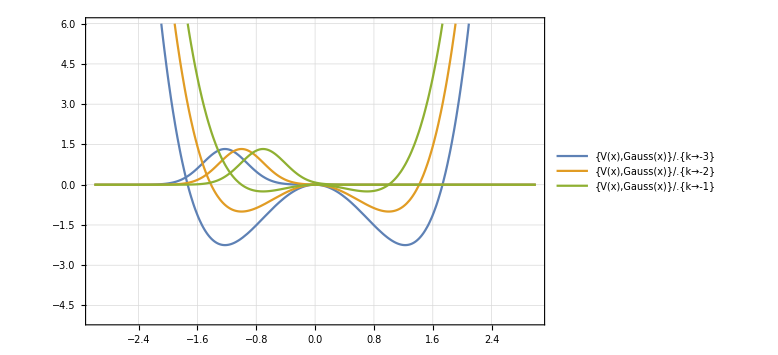

```mathematica
Plot[{{V[x], Gauss[x]}/.{k-> -3},{V[x], Gauss[x]}/.{k-> -2},{V[x], Gauss[x]}/.{k-> -1}},{x,-3,3},PlotTheme->"Detailed",ImageSize->Large, PlotRange->{-5,6}]
```

The optima of the potential are situated at,

```mathematica
Solve[V'[x]==0,x]
```

{{x→0},{x→-(ⅈ √k)/(√2)},{x→(ⅈ √k)/(√2)}}

Now we define a spatio temporal grid to solve the boundary value problem in;

```mathematica
h=0.25;
htime=0.05;

length = Floor[8/h];
time =Floor[10/htime];
xf= Array[(#-length/2 -1)*h&,{length+1}];
xi=xf
```

{-4.,-3.75,-3.5,-3.25,-3.,-2.75,-2.5,-2.25,-2.,-1.75,-1.5,-1.25,-1.,-0.75,-0.5,-0.25,0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.}

Once we have the grid, the following step numerically calculates the classical path as BVP  at each points.
This yields us  x^classical(x_initial, x_final, t), here denoted by the l x l Matrix of timeseries Pa.

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,


s=NDSolve[{Xcl''[u]+V'[Xcl[u]]==0,Xcl[0]== xi[[i]] ,Xcl[time*htime]== xf[[j]]},Xcl[u],{u,0,time*htime}];

Subscript[Pa, i,j]=(Flatten[Table[Xcl[u]/.s,{u,0,Floor[time*htime],htime}]]);
]
]
```

NDSolve::berr: The scaled boundary value residual error of 1.02888 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 1.39784 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 1.92699 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

General::stop: Further output of FindRoot::sszero will be suppressed during this calculation.

This step is rather technical, it converts the Matrix of time series into an array of dimension (l x l x t)

```mathematica
Apath=ConstantArray[0,{length+1, length+1,time+1}];

For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=1,t<time+1,t++,

Apath[[i,j,t]]= Subscript[Pa, i,j][[t]]; 
]
]
]
```

Following plot shows a few selected paths (as time series) for various initial and final conditions

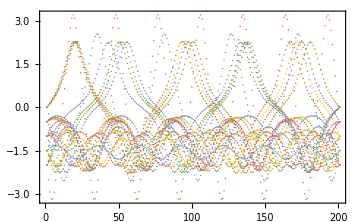

```mathematica
ListPlot[{
Subscript[Pa, 1,1],Subscript[Pa, 1,2],Subscript[Pa, 1,3],Subscript[Pa, 1,4],Subscript[Pa, 1,5],
Subscript[Pa, 2,1],Subscript[Pa, 2,2],Subscript[Pa, 2,3],Subscript[Pa, 2,4],Subscript[Pa, 2,5],
Subscript[Pa, 3,1],Subscript[Pa, 3,2],Subscript[Pa, 3,3],Subscript[Pa, 3,4],Subscript[Pa, 3,5],
Subscript[Pa, 4,1],Subscript[Pa, 4,2],Subscript[Pa, 4,3],Subscript[Pa, 4,4],Subscript[Pa, 4,5],
Subscript[Pa, 5,1],Subscript[Pa, 5,2],Subscript[Pa, 5,3],Subscript[Pa, 5,4],Subscript[Pa, 5,5]
},Frame->True,FrameStyle->Directive[GrayLevel[0],Thickness[Medium]],ImageSize->Medium, PlotStyle->Thick]
```

This plot kind of exhibits the classical density (we can attempt for a better plot at some point)


Now we wish to compute the Classical Action;

```mathematica
L=ConstantArray[0,{length+1, length+1,time}];
S=ConstantArray[0,{length+1, length+1,time}];
Psi=ConstantArray[0,{length+1, time}];



For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

L[[i,j,t]]= (A[[1,i,j, t]]-A[[1,i,j,t-1]])^2/(2*htime*htime)-V[A[[1,i,j,t]]]; 
]
]
]


For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

S[[i,j,t]]= htime*Sum[L[[i,j,u]],{u,t}]; 
]
]
]
```

And the other factors in the sum,

```mathematica
Phi=ConstantArray[0,{length+1, length+1,time-1}];
Phi2=ConstantArray[0,{length+1, length+1,time-1}];
```

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time+1,t++,

Phi[[i,j,t-1]]= htime*Sum[Sqrt[V''[Subscript[A, i,j][[u]]]],{u,t}]; 
]
]
]
```

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time+1,t++,

Phi2[[i,j,t-1]]= htime*Sum[1/V''[Subscript[A, i,j][[u]]],{u,t}]; 
]
]
]
```

```mathematica
Diff[y_,n_]:=D[Sqrt[x/Sin[x]],{x,n}]/.{x->y}
```

```mathematica
Q=Sum[1/(n!)((-I*l*Phi2)/4)^n*Diff[Phi,2n],{n,0,1}]
```

{{{1.03026-0.000138594 ⅈ,1.0644-0.000270303 ⅈ,1.10774-0.000493992 ⅈ,1.15731-0.000879894 ⅈ,1.2096-0.00155148 ⅈ,1.26044-0.00274433 ⅈ,1.30466-0.0050158 ⅈ,1.33503-0.010808 ⅈ,1.33417+0.0258597 ⅈ,1.32932+0.0644303 ⅈ,1.31849+0.108834 ⅈ,1.30081+0.155143 ⅈ,1.27655+0.200219 ⅈ,1.24678+0.241773 ⅈ,1.21314+0.278336 ⅈ,1.17756+0.309155 ⅈ,1.14208+0.33401 ⅈ,1.10892+0.353004 ⅈ,1.08064+0.366257 ⅈ,1.05877+0.37322 ⅈ,1.07078+0.394026 ⅈ,1.08658+0.43253 ⅈ,1.10651+0.490275 ⅈ,1.12887+0.572351 ⅈ,1.1492+0.686554 ⅈ,1.15773+0.843377 ⅈ,1.13229+1.05526 ⅈ,1.02263+1.31842 ⅈ,0.783472+1.55812 ⅈ,0.479054+1.68509 ⅈ,0.203591+1.72349 ⅈ,0.027527-1.73668 ⅈ,0.238353-1.75492 ⅈ,0.452745-1.78054 ⅈ,0.684104-1.80236 ⅈ,0.934028-1.80529 ⅈ,1.19531-1.77623 ⅈ,1.45295-1.70457 ⅈ,1.68128-1.58959 ⅈ,1.85617-1.45128 ⅈ,1.9718-1.32018 ⅈ,2.03596-1.21986 ⅈ,1.99022-1.42547 ⅈ,1.90248-1.35539 ⅈ,1.80191-1.26583 ⅈ,1.70162-1.17404 ⅈ,1.60653-1.08672 ⅈ,1.51843-1.00656 ⅈ,1.43793-0.934473 ⅈ,1.36534-0.870779 ⅈ,1.30107-0.815706 ⅈ,1.24598-0.769842 ⅈ,1.20185-0.734861 ⅈ,1.17277-0.717332 ⅈ,1.19778-0.686394 ⅈ,1.23751-0.63289 ⅈ,1.28651-0.555915 ⅈ,1.33895-0.453937 ⅈ,1.38812-0.326266 ⅈ,1.42713-0.174147 ⅈ,1.45016-0.000742944 ⅈ,1.45324+0.19003 ⅈ,1.43371+0.394979 ⅈ,1.38838+0.612231 ⅈ,1.31106+0.839734 ⅈ,1.19189+1.0702 ⅈ,1.0241+1.28559 ⅈ,0.815703+1.46249 ⅈ,0.589371+1.58745 ⅈ,0.368717+1.66343 ⅈ,0.168417+1.70247 ⅈ,0.0055819-1.71723 ⅈ,0.152067-1.71753 ⅈ,0.271412-1.71025 ⅈ,0.363829-1.70027 ⅈ,0.428105-1.69142 ⅈ,0.468414-1.68989 ⅈ,0.456585-1.64188 ⅈ,0.443429-1.57844 ⅈ,0.429149-1.50798 ⅈ,0.414263-1.43513 ⅈ,0.399217-1.36286 ⅈ,0.384385-1.2933 ⅈ,0.3701-1.22807 ⅈ,0.356676-1.16861 ⅈ,0.344446-1.11649 ⅈ,0.333779-1.074 ⅈ,0.324701-1.04604 ⅈ,0.350195-1.04057 ⅈ,0.395089-1.02877 ⅈ,0.457181-1.00902 ⅈ,0.534741-0.978561 ⅈ,0.625983-0.93374 ⅈ,0.728173-0.870293 ⅈ,0.836917-0.783844 ⅈ,0.945679-0.670863 ⅈ,1.04593-0.530067 ⅈ,1.12835-0.36373 ⅈ,1.18488-0.178035 ⅈ,1.21061+0.0180445 ⅈ,1.20456+0.214676 ⅈ,1.16915+0.402818 ⅈ,1.10935+0.57514 ⅈ,1.03178+0.726481 ⅈ,0.943928+0.854078 ⅈ,0.853177+0.957526 ⅈ,0.766064+1.03831 ⅈ,0.687866+1.09904 ⅈ,0.622722+1.1426 ⅈ,0.574303+1.17133 ⅈ,0.546356+1.18661 ⅈ,0.533209+1.15449 ⅈ,0.511736+1.11081 ⅈ,0.48702+1.06197 ⅈ,0.46124+1.01141 ⅈ,0.435667+0.961251 ⅈ,0.411131+0.912939 ⅈ,0.388225+0.86754 ⅈ,0.367447+0.825965 ⅈ,0.349326+0.78917 ⅈ,0.334645+0.758463 ⅈ,0.325242+0.736264 ⅈ,0.307315+0.745398 ⅈ,0.278253+0.75874 ⅈ,0.235551+0.775857 ⅈ,0.179175+0.794273 ⅈ,0.108687+0.811096 ⅈ,-0.0239014-0.822809 ⅈ,0.0745734-0.825283 ⅈ,0.18484-0.814061 ⅈ,0.30334-0.784928 ⅈ,0.424786-0.734729 ⅈ,0.542563-0.662286 ⅈ,0.649669-0.569079 ⅈ,0.740029-0.459339 ⅈ,0.809712-0.339365 ⅈ,0.857567-0.21627 ⅈ,0.885058-0.0966654 ⅈ,0.895514+0.0142458 ⅈ,0.893192+0.112985 ⅈ,0.882486+0.197646 ⅈ,0.867428+0.267465 ⅈ,0.851478+0.322285 ⅈ,0.837589+0.361895 ⅈ,0.828527+0.38516 ⅈ,0.810145+0.374254 ⅈ,0.780364+0.360849 ⅈ,0.745866+0.345925 ⅈ,0.709623+0.330409 ⅈ,0.6734+0.314923 ⅈ,0.63836+0.299899 ⅈ,0.605343+0.285659 ⅈ,0.575038+0.272476 ⅈ,0.548145+0.260621 ⅈ,0.525595+0.250424 ⅈ,0.509148+0.242339 ⅈ,0.512871+0.222418 ⅈ,0.505265+0.241322 ⅈ,0.492722+0.268884 ⅈ,0.474138+0.303786 ⅈ,0.447979+0.344802 ⅈ,0.4125+0.390323 ⅈ,0.366014+0.43808 ⅈ,0.307275+0.485019 ⅈ,0.23594+0.527381 ⅈ,0.153024+0.561078 ⅈ,0.0611324+0.582335 ⅈ,0.0356786-0.588479 ⅈ,0.132494-0.578575 ⅈ,0.224418-0.553668 ⅈ,0.307428-0.516514 ⅈ,0.378938-0.470931 ⅈ,0.437926-0.421048 ⅈ,0.484692-0.37067 ⅈ,0.520432-0.322932 ⅈ,0.546778-0.280214 ⅈ,0.565418-0.244279 ⅈ,0.577801-0.216589 ⅈ,0.584846-0.198884 ⅈ,0.572826-0.197654 ⅈ,0.552826-0.190867 ⅈ,0.529319-0.182371 ⅈ,0.504413-0.173217 ⅈ,0.479365-0.16397 ⅈ,0.455-0.154983 ⅈ,0.431908-0.146501 ⅈ,0.410566-0.138721 ⅈ,0.391433-0.131832 ⅈ,0.375079-0.126087 ⅈ,0.362458-0.121991 ⅈ,0.355983-0.122664 ⅈ,0.360257-0.110943 ⅈ,0.366137-0.0925634 ⅈ,0.372476-0.0677914 ⅈ,0.37799-0.0365813 ⅈ,0.381133+0.00106087 ⅈ,0.380088+0.0448131 ⅈ,0.372884+0.0938024 ⅈ,0.357641+0.146426 ⅈ},{1.03064-0.000137037 ⅈ,1.0661-0.00026476 ⅈ,1.11232-0.000480553 ⅈ,1.16701-0.000851861 ⅈ,1.2274-0.00149451 ⅈ,1.2901-0.00261232 ⅈ,1.35095-0.00458662 ⅈ,1.40473-0.00826085 ⅈ,1.44443-0.0165952 ⅈ,1.45091-0.325444 ⅈ,1.48248-0.277265 ⅈ,1.51664-0.215423 ⅈ,1.54421-0.14149 ⅈ,1.5596-0.0608099 ⅈ,1.56096+0.0194745 ⅈ,1.55013+0.0919136 ⅈ,1.53147+0.149489 ⅈ,1.4895+0.195237 ⅈ,1.54353+0.210385 ⅈ,1.63368+0.247106 ⅈ,1.77669+0.318172 ⅈ,2.00111+0.465038 ⅈ,2.33558+0.811512 ⅈ,2.63379+1.69512 ⅈ,1.75868+3.19863 ⅈ,-0.263292+2.52925 ⅈ,0.175496+1.45137 ⅈ,0.445359+1.66563 ⅈ,0.319226+1.8591 ⅈ,-0.161367-1.98113 ⅈ,-0.0207942-2.13473 ⅈ,0.136529-2.3937 ⅈ,0.41472-2.84207 ⅈ,1.14551-3.51992 ⅈ,2.98454-3.75825 ⅈ,4.68184-1.64534 ⅈ,3.34426+0.382376 ⅈ,2.0564+0.103966 ⅈ,1.85533-0.409337 ⅈ,1.95411-0.623564 ⅈ,2.05246-0.681069 ⅈ,2.08199-0.690336 ⅈ,2.15656-0.651048 ⅈ,2.17337-0.604307 ⅈ,2.17642-0.569026 ⅈ,2.16642-0.547575 ⅈ,2.144-0.536192 ⅈ,2.11296-0.53057 ⅈ,2.07999-0.528555 ⅈ,2.05675-0.533036 ⅈ,2.03508-0.484342 ⅈ,2.04168-0.440693 ⅈ,2.06035-0.380744 ⅈ,2.09255-0.300253 ⅈ,2.13886-0.194247 ⅈ,2.19966-0.0571087 ⅈ,2.27694+0.120045 ⅈ,2.37297+0.356389 ⅈ,2.47855+0.692276 ⅈ,2.53325+1.19159 ⅈ,2.35433+1.86282 ⅈ,1.7593+2.41723 ⅈ,1.08945+2.49342 ⅈ,0.741622+2.40106 ⅈ,0.531063+2.42515 ⅈ,0.310874+2.51273 ⅈ,0.0737663+2.61246 ⅈ,0.175003-2.71423 ⅈ,0.438746-2.81279 ⅈ,0.719594-2.89684 ⅈ,1.01029-2.95217 ⅈ,1.29221-2.96993 ⅈ,1.54025-2.9541 ⅈ,1.7307-2.92355 ⅈ,1.85961-2.9262 ⅈ,1.79893-2.79608 ⅈ,1.73334-2.6401 ⅈ,1.66353-2.48384 ⅈ,1.59375-2.33893 ⅈ,1.52764-2.21081 ⅈ,1.46814-2.10285 ⅈ,1.41779-2.0194 ⅈ,1.37448-1.97256 ⅈ,1.44306-1.94075 ⅈ,1.54579-1.87671 ⅈ,1.67581-1.7754 ⅈ,1.82051-1.62936 ⅈ,1.96194-1.43592 ⅈ,2.08183-1.20356 ⅈ,2.17276-0.950507 ⅈ,2.24387-0.691091 ⅈ,2.30959-0.422998 ⅈ,2.37435-0.131528 ⅈ,2.42949+0.19952 ⅈ,2.45417+0.583008 ⅈ,2.41162+1.02023 ⅈ,2.25639+1.47955 ⅈ,1.9742+1.8866 ⅈ,1.61998+2.17239 ⅈ,1.27796+2.33645 ⅈ,0.991176+2.42774 ⅈ,0.758209+2.48759 ⅈ,0.565859+2.53365 ⅈ,0.405462+2.57061 ⅈ,0.273979+2.5993 ⅈ,0.172003+2.61996 ⅈ,0.103108+2.63238 ⅈ,0.139087+2.61903 ⅈ,0.133651+2.55642 ⅈ,0.125191+2.47761 ⅈ,0.116124+2.39215 ⅈ,0.107529+2.30621 ⅈ,0.100135+2.2248 ⅈ,0.0947359+2.15299 ⅈ,0.0931882+2.09786 ⅈ,0.166875+2.07771 ⅈ,0.102459+2.08426 ⅈ,-0.00698427-2.09087 ⅈ,0.118177-2.09383 ⅈ,0.272898-2.08857 ⅈ,0.457415-2.06928 ⅈ,0.671513-2.02834 ⅈ,0.913221-1.95581 ⅈ,1.17655-1.83959 ⅈ,1.44868-1.6677 ⅈ,1.70892-1.43359 ⅈ,1.93297-1.14251 ⅈ,2.10242-0.812385 ⅈ,2.21161-0.466225 ⅈ,2.26566-0.122857 ⅈ,2.27349+0.206096 ⅈ,2.24337+0.513663 ⅈ,2.1825+0.794419 ⅈ,2.09843+1.04348 ⅈ,1.99982+1.25721 ⅈ,1.89604+1.43408 ⅈ,1.79609+1.57485 ⅈ,1.70781+1.68179 ⅈ,1.63776+1.75743 ⅈ,1.59089+1.80434 ⅈ,1.56946+1.75996 ⅈ,1.5217+1.70328 ⅈ,1.46536+1.64056 ⅈ,1.407+1.57676 ⅈ,1.35073+1.51533 ⅈ,1.29987+1.45917 ⅈ,1.25821+1.41127 ⅈ,1.23368+1.37548 ⅈ,1.20146+1.40682 ⅈ,1.14838+1.45462 ⅈ,1.0714+1.51737 ⅈ,0.968401+1.59089 ⅈ,0.836725+1.67009 ⅈ,0.674018+1.74852 ⅈ,0.479133+1.8184 ⅈ,0.252867+1.87096 ⅈ,0.00158648-1.89717 ⅈ,0.278446-1.88834 ⅈ,0.569109-1.83682 ⅈ,0.861772-1.73706 ⅈ,1.14164-1.58765 ⅈ,1.39297-1.39358 ⅈ,1.60292-1.16671 ⅈ,1.76517-0.923148 ⅈ,1.88065-0.678946 ⅈ,1.9555-0.446814 ⅈ,1.99815-0.235166 ⅈ,2.0172-0.0487862 ⅈ,2.02034+0.109997 ⅈ,2.01407+0.240225 ⅈ,2.00371+0.341378 ⅈ,1.99367+0.4124 ⅈ,1.9872+0.462523 ⅈ,1.93931+0.447529 ⅈ,1.87557+0.432518 ⅈ,1.8059+0.4171 ⅈ,1.73587+0.401783 ⅈ,1.66954+0.387073 ⅈ,1.61062+0.373406 ⅈ,1.56388+0.360962 ⅈ,1.54123+0.344154 ⅈ,1.53283+0.387864 ⅈ,1.5172+0.45496 ⅈ,1.49171+0.543604 ⅈ,1.45265+0.652226 ⅈ,1.39535+0.778788 ⅈ,1.31448+0.91998 ⅈ,1.20466+1.07052 ⅈ,1.06143+1.22273 ⅈ,0.882637+1.36664 ⅈ,0.669777+1.49108 ⅈ,0.428639+1.58545 ⅈ,0.168782+1.64179 ⅈ,0.0979612-1.65613 ⅈ,0.359303-1.62891 ⅈ,0.604125-1.56464 ⅈ,0.823765-1.47102 ⅈ,1.01287-1.35769 ⅈ,1.16959-1.23467 ⅈ},{1.031-0.000135594 ⅈ,1.06775-0.000259837 ⅈ,1.11681-0.00046938 ⅈ,1.17659-0.000831191 ⅈ,1.2451-0.00146136 ⅈ,1.31986-0.00256278 ⅈ,1.39766-0.00449388 ⅈ,1.4744-0.00790837 ⅈ,1.54495-0.0141128 ⅈ,1.60295-0.0264318 ⅈ,1.63972-0.0614584 ⅈ,1.6373+0.0560884 ⅈ,1.62607+0.123887 ⅈ,1.60617+0.187607 ⅈ,1.57903+0.248158 ⅈ,1.5293+0.346792 ⅈ,1.56841+0.344105 ⅈ,1.61995+0.383529 ⅈ,1.68776+0.46335 ⅈ,1.75922+0.61115 ⅈ,1.75155+0.889776 ⅈ,1.14537+1.26405 ⅈ,-0.484162-2.93322 ⅈ,6.83203+7.02451 ⅈ,0.0645637+3.9873 ⅈ,-0.0500077+2.66989 ⅈ,-0.0485269+2.28375 ⅈ,-0.0760178+2.15025 ⅈ,0.127459-2.14616 ⅈ,0.215659-2.24422 ⅈ,0.384647-2.44027 ⅈ,0.764947-2.68378 ⅈ,1.60569-2.2762 ⅈ,-5.38882-0.621463 ⅈ,10.1224-5.91814 ⅈ,5.42027-0.130376 ⅈ,3.91418+0.0333832 ⅈ,3.3818+0.0268687 ⅈ,3.13019+0.0264183 ⅈ,2.99446+0.0304264 ⅈ,2.91741+0.0329927 ⅈ,2.87325+0.0269369 ⅈ,2.84186-0.0316507 ⅈ,2.84712+0.00204448 ⅈ,2.84252+0.00263542 ⅈ,2.8349-0.00193258 ⅈ,2.83235+0.00404802 ⅈ,2.07695-1.56615 ⅈ,2.17782-1.50957 ⅈ,2.32423-1.41933 ⅈ,2.49866-1.32408 ⅈ,2.70465-1.24849 ⅈ,2.97144-1.2193 ⅈ,3.3735-1.2697 ⅈ,4.09428-1.44178 ⅈ,5.65649-1.7346 ⅈ,9.81019-1.41536 ⅈ,20.0121+8.68631 ⅈ,-17.3909+36.3671 ⅈ,-9.38114-12.2695 ⅈ,3.02854-2.39775 ⅈ,2.52161+1.47955 ⅈ,1.80535+2.6339 ⅈ,-1.501-3.23018 ⅈ,-1.50412-3.87729 ⅈ,-1.74301-4.9369 ⅈ,-2.07135-6.94238 ⅈ,-1.78486-10.8625 ⅈ,1.80182-17.6957 ⅈ,14.7779-24.3149 ⅈ,37.0167-16.1998 ⅈ,45.236+11.7879 ⅈ,30.9537+33.2275 ⅈ,15.4304+38.7924 ⅈ,13.4214+47.7357 ⅈ,13.4796+35.3667 ⅈ,12.6762+25.317 ⅈ,11.5746+18.6233 ⅈ,10.6564+14.7674 ⅈ,8.43027+15.7606 ⅈ,3.35867+15.2311 ⅈ,-1.92121+11.8663 ⅈ,-4.59244+6.40609 ⅈ,-3.98603+1.52412 ⅈ,-1.80248-1.18703 ⅈ,0.305327-2.08179 ⅈ,1.8026-2.09171 ⅈ,2.81862-1.84438 ⅈ,3.66544-1.61369 ⅈ,4.73266-1.45613 ⅈ,6.68067-1.13365 ⅈ,10.7602+1.02728 ⅈ,14.279+12.8299 ⅈ,-10.1247+22.3756 ⅈ,-11.7396-3.49825 ⅈ,0.104862-3.40942 ⅈ,2.33807+0.281931 ⅈ,2.31044+2.16471 ⅈ,2.04177+3.17249 ⅈ,-1.84044-3.87594 ⅈ,-1.71636-4.50707 ⅈ,-1.63296-5.15319 ⅈ,-1.55346-5.82954 ⅈ,-1.45632-6.50315 ⅈ,-1.34743-7.10509 ⅈ,-1.27545-7.54634 ⅈ,-0.973515-7.32542 ⅈ,-0.577921-7.13806 ⅈ,-0.187302-6.90984 ⅈ,0.129551-6.67206 ⅈ,0.313645-6.44654 ⅈ,0.509852-6.72886 ⅈ,0.947852-7.18755 ⅈ,1.76619-7.83334 ⅈ,3.27924-8.57903 ⅈ,6.02285-8.94436 ⅈ,10.2708-7.30065 ⅈ,13.3524-1.00381 ⅈ,8.75362+6.41626 ⅈ,1.20515+5.28667 ⅈ,-0.156236+0.763543 ⅈ,1.40092-1.21399 ⅈ,2.86919-1.49479 ⅈ,4.01172-1.2547 ⅈ,5.23147-0.79636 ⅈ,6.95767+0.225023 ⅈ,9.13652+3.11424 ⅈ,8.83623+9.63567 ⅈ,0.327692+14.4182 ⅈ,-7.4658+8.00608 ⅈ,-5.62557+1.15938 ⅈ,-1.93882-0.370169 ⅈ,0.154132+0.218541 ⅈ,1.07553+1.07155 ⅈ,1.44614+1.75404 ⅈ,1.58498+2.23141 ⅈ,1.63432+2.53073 ⅈ,1.67239+2.63177 ⅈ,1.50086+2.68397 ⅈ,1.29838+2.72291 ⅈ,1.10857+2.76522 ⅈ,0.961914+2.81111 ⅈ,0.794694+3.35088 ⅈ,0.781608+3.43168 ⅈ,0.741466+3.57553 ⅈ,0.660847+3.77081 ⅈ,0.524572+4.01695 ⅈ,-0.312289-4.32357 ⅈ,0.0162891-4.71408 ⅈ,0.557301-5.21999 ⅈ,1.53741-5.82398 ⅈ,3.3804-6.19376 ⅈ,6.14538-5.0269 ⅈ,7.21544-1.18123 ⅈ,4.47218+1.13518 ⅈ,2.7459+0.109327 ⅈ,3.01666-0.763459 ⅈ,3.68895-0.834635 ⅈ,4.31924-0.539955 ⅈ,4.94974-0.0521732 ⅈ,5.6302+0.682736 ⅈ,6.27475+1.81824 ⅈ,6.58838+3.44646 ⅈ,6.16302+5.35388 ⅈ,4.86228+6.96305 ⅈ,3.09405+7.76268 ⅈ,1.47706+7.75953 ⅈ,0.345281+7.34784 ⅈ,-0.317744+6.93664 ⅈ,-1.17168+7.24944 ⅈ,-0.650349+6.80027 ⅈ,-0.17956+6.34755 ⅈ,0.192648+5.95559 ⅈ,0.472277+5.65631 ⅈ,0.147186+5.63765 ⅈ,-0.195082+5.298 ⅈ,-0.49803+4.74424 ⅈ,-0.606882+4.06099 ⅈ,-0.432105+3.4327 ⅈ,-0.0434683+3.07138 ⅈ,0.356092+3.07388 ⅈ,0.576152+3.3747 ⅈ,0.537244+3.84499 ⅈ,-0.231399-4.40408 ⅈ,0.388782-5.03535 ⅈ,1.51861-5.67801 ⅈ,3.47865-5.90417 ⅈ,5.9552-4.55266 ⅈ,6.7018-1.36277 ⅈ,4.86157+0.599204 ⅈ,3.38083+0.295019 ⅈ,3.21799-0.369824 ⅈ,3.60644-0.623367 ⅈ,4.08446-0.555147 ⅈ,4.53277-0.317451 ⅈ,4.93403+0.0106472 ⅈ,5.28344+0.3903 ⅈ,5.57284+0.791399 ⅈ,5.79531+1.179 ⅈ},{1.04421-0.000108481 ⅈ,1.13394-0.000205031 ⅈ,1.32054-0.000483357 ⅈ,1.70155-0.00167429 ⅈ,2.63488-0.0132302 ⅈ,1070.96+25.9763 ⅈ,0.0352731+3.32918 ⅈ,0.0158762+2.71832 ⅈ,0.2093+2.65908 ⅈ,0.395398+2.49555 ⅈ,0.493572+2.30984 ⅈ,0.531325+2.19554 ⅈ,0.40234+2.15229 ⅈ,0.216252+2.08518 ⅈ,0.0418593+2.05283 ⅈ,0.135822-2.14477 ⅈ,0.43525-2.48966 ⅈ,1.55839-3.22922 ⅈ,3.14975-1.54352 ⅈ,2.91061-0.714049 ⅈ,2.74539-0.324265 ⅈ,2.68179-0.149087 ⅈ,2.67247-0.0761013 ⅈ,2.60809-0.0723048 ⅈ,2.50029-0.0648859 ⅈ,2.39042-0.0546222 ⅈ,2.38602-0.049864 ⅈ,2.42345+0.108062 ⅈ,2.51428+0.38172 ⅈ,2.67446+0.886117 ⅈ,2.60959+1.9016 ⅈ,1.59796+2.70271 ⅈ,0.812391+2.77189 ⅈ,0.293217+2.80185 ⅈ,0.0927876-2.8639 ⅈ,0.414203-2.96062 ⅈ,0.663979-3.04427 ⅈ,0.726371-2.08781 ⅈ,0.560886-2.10019 ⅈ,0.447541-2.09458 ⅈ,0.396186-2.07266 ⅈ,0.420685-2.03388 ⅈ,0.430276-2.06749 ⅈ,0.621292-2.43148 ⅈ,1.72256-2.71753 ⅈ,2.87961-1.68516 ⅈ,2.92267-0.462913 ⅈ,2.59095+0.199824 ⅈ,2.33284+0.439349 ⅈ,2.36744+0.466467 ⅈ,2.63655+0.585673 ⅈ,2.82172+0.763567 ⅈ,2.62972+0.88802 ⅈ,2.38829+0.976255 ⅈ,2.19549+1.00207 ⅈ,2.1892+1.0714 ⅈ,2.15738+1.37198 ⅈ,1.938+1.87274 ⅈ,1.36721+2.36163 ⅈ,0.603644+2.54245 ⅈ,0.0357471-2.45585 ⅈ,0.472403-2.35833 ⅈ,0.909253-2.40146 ⅈ,1.50957-2.37778 ⅈ,2.04135-2.13828 ⅈ,2.33173-1.87555 ⅈ,2.27781-1.8587 ⅈ,2.07979-1.68315 ⅈ,1.89868-1.52153 ⅈ,1.79046-1.42671 ⅈ,1.90641-1.28006 ⅈ,2.07143-0.981558 ⅈ,2.19268-0.552313 ⅈ,2.21614-0.0644967 ⅈ,2.17389+0.421331 ⅈ,2.09709+0.948302 ⅈ,1.87452+1.53341 ⅈ,1.46336+1.99874 ⅈ,1.03214+2.24386 ⅈ,0.716181+2.33839 ⅈ,0.563169+2.36464 ⅈ,0.543331+2.22719 ⅈ,0.511753+2.05556 ⅈ,0.482119+1.9155 ⅈ,0.426611+1.92681 ⅈ,-0.227369-1.95619 ⅈ,0.0712724-1.96635 ⅈ,0.450746-1.92981 ⅈ,0.902052-1.81292 ⅈ,1.38716-1.55166 ⅈ,1.7853-1.12761 ⅈ,2.00642-0.650675 ⅈ,2.08503-0.239737 ⅈ,2.09469+0.0620214 ⅈ,2.08397+0.246801 ⅈ,2.04236+0.235135 ⅈ,1.90582+0.222812 ⅈ,1.76909+0.210613 ⅈ,1.68486+0.202131 ⅈ,1.67076+0.321974 ⅈ,1.62547+0.538805 ⅈ,1.51795+0.83355 ⅈ,1.30685+1.17347 ⅈ,0.967388+1.4891 ⅈ,0.536864+1.70076 ⅈ,-0.0982497-1.78455 ⅈ,0.285887-1.7735 ⅈ,0.587887-1.71212 ⅈ,0.795153-1.64017 ⅈ,0.893258-1.59613 ⅈ,0.846264-1.50203 ⅈ,0.787674-1.38589 ⅈ,0.739102-1.29199 ⅈ,0.781802-1.26854 ⅈ,0.915864-1.18418 ⅈ,1.10203-1.02762 ⅈ,1.30131-0.779633 ⅈ,1.46027-0.440875 ⅈ,1.53269-0.0464497 ⅈ,1.5046+0.349276 ⅈ,1.39389+0.697545 ⅈ,1.23896+0.966731 ⅈ,1.08637+1.14766 ⅈ,0.977799+1.2474 ⅈ,0.954154+1.21268 ⅈ,0.883834+1.1276 ⅈ,0.815852+1.04509 ⅈ,0.776574+0.996044 ⅈ,0.700445+1.05416 ⅈ,0.55343+1.14325 ⅈ,0.333006+1.23164 ⅈ,-0.0455407-1.28196 ⅈ,0.282477-1.2603 ⅈ,0.607112-1.15195 ⅈ,0.882104-0.971873 ⅈ,1.07964-0.760533 ⅈ,1.20035-0.563807 ⅈ,1.26293-0.415904 ⅈ,1.28583-0.344207 ⅈ,1.21044-0.322991 ⅈ,1.11931-0.296908 ⅈ,1.04624-0.276205 ⅈ,1.05621-0.238171 ⅈ,1.07841-0.123603 ⅈ,1.08847+0.0524068 ⅈ,1.05942+0.278991 ⅈ,0.966166+0.531581 ⅈ,0.799249+0.771041 ⅈ,0.576413+0.95764 ⅈ,0.337059+1.07199 ⅈ,-0.121371-1.12202 ⅈ,0.0444352-1.13138 ⅈ,0.146062-1.12512 ⅈ,0.140288-1.0915 ⅈ,0.131692-1.01348 ⅈ,0.123367-0.938584 ⅈ,0.117981-0.896183 ⅈ,0.187438-0.885905 ⅈ,0.307535-0.854812 ⅈ,0.46395-0.785798 ⅈ,0.634559-0.662714 ⅈ,0.787331-0.481586 ⅈ,0.891254-0.259573 ⅈ,0.932778-0.0303685 ⅈ,0.921668+0.172587 ⅈ,0.88185+0.329111 ⅈ,0.838846+0.432424 ⅈ,0.815248+0.47745 ⅈ,0.765935+0.449481 ⅈ,0.707331+0.416455 ⅈ,0.661149+0.390196 ⅈ,0.645524+0.416442 ⅈ,0.597429+0.485791 ⅈ,0.511716+0.579007 ⅈ,0.380511+0.676496 ⅈ,0.204683+0.752788 ⅈ,-0.000721636-0.784327 ⅈ,0.202405-0.76209 ⅈ,0.376642-0.697089 ⅈ,0.506889-0.61309 ⅈ,0.592169-0.534657 ⅈ,0.637939-0.481387 ⅈ,0.616152-0.465847 ⅈ,0.572307-0.431671 ⅈ,0.530718-0.399313 ⅈ,0.507816-0.382156 ⅈ,0.537532-0.340899 ⅈ,0.581107-0.263936 ⅈ,0.622737-0.150163 ⅈ,0.643437-0.00326752 ⅈ,0.625976+0.162177 ⅈ,0.564397+0.322285 ⅈ,0.469253+0.454132 ⅈ,0.362171+0.546559 ⅈ,0.264951+0.601998 ⅈ,0.193311+0.630131 ⅈ,0.161028+0.639683 ⅈ,0.150778+0.600685 ⅈ,0.138718+0.555308 ⅈ},{1.02928-0.000143087 ⅈ,1.05996-0.000287699 ⅈ,1.09586-0.000542217 ⅈ,1.13239-0.00100657 ⅈ,1.16424-0.00193911 ⅈ,1.18394-0.00490151 ⅈ,1.1834+0.0167492 ⅈ,1.17944+0.0477165 ⅈ,1.16989+0.0836979 ⅈ,1.15357+0.121466 ⅈ,1.13027+0.158487 ⅈ,1.10047+0.192818 ⅈ,1.06521+0.22312 ⅈ,1.02571+0.248628 ⅈ,0.983255+0.269067 ⅈ,0.939026+0.284533 ⅈ,0.894019+0.29537 ⅈ,0.849035+0.302061 ⅈ,0.804695+0.305152 ⅈ,0.76146+0.305198 ⅈ,0.71967+0.302727 ⅈ,0.67957+0.298226 ⅈ,0.641338+0.292136 ⅈ,0.605112+0.28485 ⅈ,0.571014+0.276721 ⅈ,0.539162+0.268072 ⅈ,0.509703+0.259202 ⅈ,0.482839+0.250409 ⅈ,0.458876+0.242008 ⅈ,0.438323+0.23437 ⅈ,0.422152+0.228018 ⅈ,0.413016+0.223832 ⅈ,0.408415+0.235551 ⅈ,0.399626+0.2556 ⅈ,0.386208+0.282636 ⅈ,0.366973+0.315974 ⅈ,0.340288+0.354762 ⅈ,0.304278+0.397547 ⅈ,0.2572+0.441942 ⅈ,0.198059+0.484537 ⅈ,0.127311+0.521243 ⅈ,0.0472905+0.548142 ⅈ,0.0379982-0.562524 ⅈ,0.123702-0.563598 ⅈ,0.205153-0.552572 ⅈ,0.278667-0.532183 ⅈ,0.341905-0.50599 ⅈ,0.393809-0.477711 ⅈ,0.434227-0.450802 ⅈ,0.463333-0.428383 ⅈ,0.480617-0.413829 ⅈ,0.469492-0.403994 ⅈ,0.451739-0.384855 ⅈ,0.430847-0.36227 ⅈ,0.408557-0.338479 ⅈ,0.385874-0.314689 ⅈ,0.36341-0.291588 ⅈ,0.34154-0.26956 ⅈ,0.320492-0.248804 ⅈ,0.300394-0.229404 ⅈ,0.281311-0.211372 ⅈ,0.263269-0.194678 ⅈ,0.246265-0.179269 ⅈ,0.230281-0.165076 ⅈ,0.215289-0.152027 ⅈ,0.201256-0.14005 ⅈ,0.18815-0.129076 ⅈ,0.175938-0.119039 ⅈ,0.164593-0.109882 ⅈ,0.154094-0.101556 ⅈ,0.144429-0.0940208 ⅈ,0.1356-0.0872506 ⅈ,0.127626-0.0812349 ⅈ,0.12056-0.0759885 ⅈ,0.114504-0.0715687 ⅈ,0.109672-0.0681247 ⅈ,0.106596-0.0661416 ⅈ,0.108741-0.0631506 ⅈ,0.112397-0.0575279 ⅈ,0.116953-0.0494402 ⅈ,0.121852-0.0387682 ⅈ,0.126431-0.0253761 ⅈ,0.129882-0.00925843 ⅈ,0.131301+0.0093291 ⅈ,0.129818+0.029772 ⅈ,0.124789+0.0510835 ⅈ,0.116+0.0720185 ⅈ,0.103782+0.0913056 ⅈ,0.0889674+0.107917 ⅈ,0.0727008+0.121264 ⅈ,0.0561939+0.131247 ⅈ,0.040517+0.13817 ⅈ,0.0264961+0.142582 ⅈ,0.0147178+0.145121 ⅈ,0.00562846+0.146398 ⅈ,0.00022171-0.146922 ⅈ,-0.000279467-0.144124 ⅈ,3.27132×10^-6-0.138171 ⅈ,0.000403194-0.130983 ⅈ,0.000825737-0.123296 ⅈ,0.00122987-0.11551 ⅈ,0.00159578-0.107862 ⅈ,0.00191476-0.100487 ⅈ,0.00218438-0.0934652 ⅈ,0.00240572-0.0868339 ⅈ,0.00258183-0.0806085 ⅈ,0.00271669-0.0747889 ⅈ,0.00281466-0.0693657 ⅈ,0.00288014-0.0643242 ⅈ,0.00291736-0.059647 ⅈ,0.00293028-0.0553157 ⅈ,0.00292258-0.0513121 ⅈ,0.00289762-0.047619 ⅈ,0.00285847-0.0442212 ⅈ,0.00280797-0.0411055 ⅈ,0.00274876-0.0382621 ⅈ,0.00268332-0.035685 ⅈ,0.00261406-0.033374 ⅈ,0.00254335-0.0313372 ⅈ,0.00247344-0.0295966 ⅈ,0.00240577-0.0282035 ⅈ,0.00233146-0.0272943 ⅈ,0.0030604-0.0272612 ⅈ,0.00449099-0.0271351 ⅈ,0.00648769-0.0268315 ⅈ,0.00898531-0.0262362 ⅈ,0.0119099-0.0252143 ⅈ,0.0151464-0.0236254 ⅈ,0.0185219-0.0213497 ⅈ,0.0218073-0.0183236 ⅈ,0.0247426-0.0145748 ⅈ,0.0270841-0.0102407 ⅈ,0.0286607-0.00555499 ⅈ,0.0294138-0.000802563 ⅈ,0.0294041+0.00374046 ⅈ,0.028785+0.0078564 ⅈ,0.0277585+0.0114092 ⅈ,0.0265331+0.0143399 ⅈ,0.0252976+0.0166442 ⅈ,0.0242139+0.0183401 ⅈ,0.0234354+0.0194229 ⅈ,0.0233844+0.0188928 ⅈ,0.0224374+0.0181583 ⅈ,0.0212496+0.0172605 ⅈ,0.0199649+0.0162926 ⅈ,0.018659+0.0153064 ⅈ,0.0173752+0.0143325 ⅈ,0.0161387+0.0133893 ⅈ,0.0149634+0.0124874 ⅈ,0.0138564+0.0116323 ⅈ,0.0128201+0.0108265 ⅈ,0.0118544+0.0100706 ⅈ,0.0109575+0.00936367 ⅈ,0.0101265+0.00870429 ⅈ,0.00935824+0.00809053 ⅈ,0.00864925+0.00752031 ⅈ,0.00799615+0.00699152 ⅈ,0.00739575+0.00650218 ⅈ,0.00684515+0.00605048 ⅈ,0.00634185+0.0056349 ⅈ,0.00588386+0.00525428 ⅈ,0.00546982+0.00490795 ⅈ,0.00509926+0.00459593 ⅈ,0.00477298+0.00431925 ⅈ,0.00449391+0.00408057 ⅈ,0.00426924+0.00388577 ⅈ,0.0041187+0.00374868 ⅈ,0.00403325+0.00384731 ⅈ,0.00384291+0.00405158 ⅈ,0.00355235+0.00432763 ⅈ,0.00315247+0.00464977 ⅈ,0.00263122+0.0049891 ⅈ,0.00198039+0.0053096 ⅈ,0.00120192+0.00556853 ⅈ,0.000313586+0.00572088 ⅈ,0.000648281-0.00572768 ⅈ,0.00163153-0.00556593 ⅈ,0.00257706-0.00523619 ⅈ,0.00343113-0.00476379 ⅈ,0.00415612-0.00419268 ⅈ,0.00473561-0.00357489 ⅈ,0.00517278-0.00296029 ⅈ,0.00548453-0.00239008 ⅈ,0.00569436-0.0018951 ⅈ,0.00582636-0.00149842 ⅈ,0.00590046-0.00122289 ⅈ,0.00593882-0.0010594 ⅈ,0.00571329-0.00101828 ⅈ,0.00542454-0.000960467 ⅈ,0.0051093-0.000896402 ⅈ,0.00478682-0.000830886 ⅈ,0.00446829-0.000766554 ⅈ,0.00416025-0.000704884 ⅈ,0.00386643-0.000646667 ⅈ,0.00358875-0.000592273 ⅈ,0.00332803-0.000541813 ⅈ,0.00308435-0.000495241 ⅈ,0.00285738-0.000452419 ⅈ,0.00264652-0.000413157 ⅈ},{1.03002-0.000139197 ⅈ,1.06555-0.000265309 ⅈ,1.11293-0.000475796 ⅈ,1.17066-0.000835296 ⅈ,1.23696-0.00145441 ⅈ,1.30962-0.00252367 ⅈ,1.38594-0.00437321 ⅈ,1.46258-0.00758427 ⅈ,1.53557-0.0132263 ⅈ,1.6005-0.0234793 ⅈ,1.65284-0.0437964 ⅈ,1.68874-0.093898 ⅈ,1.70658-0.310916 ⅈ,1.72019-0.721249 ⅈ,1.75352-0.861836 ⅈ,1.81392-1.03013 ⅈ,1.911-1.31193 ⅈ,2.06305-1.84914 ⅈ,2.30861-3.05418 ⅈ,2.74547-6.67448 ⅈ,3.73664-27.8157 ⅈ,11.9537-8031.71 ⅈ,34.2822+4.16805 ⅈ,4.59207+2.91906 ⅈ,1.46464+2.44679 ⅈ,0.706835+2.22821 ⅈ,0.478617+2.14845 ⅈ,0.457032+2.17525 ⅈ,0.608762+2.31139 ⅈ,1.10376+2.59377 ⅈ,2.84366+3.133 ⅈ,13.8823+4.33646 ⅈ,1621.+11.4262 ⅈ,5.64229-42.2965 ⅈ,3.99556-6.57382 ⅈ,3.40848-2.58892 ⅈ,3.121-1.47185 ⅈ,2.96522-1.02911 ⅈ,2.87878-0.822743 ⅈ,2.83188-0.720454 ⅈ,2.80801-0.671662 ⅈ,2.79713-0.655264 ⅈ,2.79294-0.668426 ⅈ,2.79169-0.759807 ⅈ,2.79131-1.15842 ⅈ,2.79101-1.22233 ⅈ,2.79261-1.23539 ⅈ,2.7999-1.24772 ⅈ,2.81882-1.28551 ⅈ,2.8581-1.38049 ⅈ,2.93078-1.58557 ⅈ,3.05771-2.01059 ⅈ,3.276-2.93798 ⅈ,3.66337-5.31294 ⅈ,4.43016-13.9855 ⅈ,6.54779-97.1041 ⅈ,2207.02+12.388 ⅈ,27.6595+5.28603 ⅈ,6.08717+4.04112 ⅈ,2.59081+3.53834 ⅈ,1.65992+3.3373 ⅈ,1.52048+3.32223 ⅈ,1.90755+3.46142 ⅈ,3.09319+3.76549 ⅈ,6.30681+4.29147 ⅈ,16.971+5.19624 ⅈ,75.4264+6.99603 ⅈ,1936.66+13.4394 ⅈ,11.8304-989.746 ⅈ,7.55958-101.262 ⅈ,6.24491-37.4171 ⅈ,5.60771-21.0997 ⅈ,5.25407-14.8675 ⅈ,5.05431-12.1595 ⅈ,4.95331-11.3716 ⅈ,4.91359-13.7566 ⅈ,4.84411-13.4725 ⅈ,4.71894-11.7523 ⅈ,4.5526-9.56792 ⅈ,4.36559-7.43944 ⅈ,4.17817-5.64785 ⅈ,4.00817-4.28749 ⅈ,3.87099-3.34751 ⅈ,3.7814-2.78603 ⅈ,3.75646-2.58639 ⅈ,3.82085-2.82 ⅈ,4.01786-3.80206 ⅈ,4.43865-6.73761 ⅈ,5.32992-17.9888 ⅈ,7.80224-124.296 ⅈ,5220.75+16.5843 ⅈ,48.8068+6.64065 ⅈ,11.1881+5.09133 ⅈ,5.01418+4.47543 ⅈ,3.28353+4.21618 ⅈ,2.87286+4.15378 ⅈ,3.15019+4.22607 ⅈ,4.05341+4.40532 ⅈ,5.78923+4.6788 ⅈ,8.83153+5.04076 ⅈ,14.027+5.4874 ⅈ,22.7309+6.01159 ⅈ,36.7727+6.59531 ⅈ,57.708+7.19927 ⅈ,84.6535+7.75335 ⅈ,112.158+8.16233 ⅈ,141.694+8.36235 ⅈ,177.428+8.61378 ⅈ,257.663+9.25165 ⅈ,526.308+10.6613 ⅈ,2432.6+14.4839 ⅈ,47.7879-942234. ⅈ,12.1356-974.088 ⅈ,8.40244-149.14 ⅈ,6.70004-45.2321 ⅈ,5.71414-18.706 ⅈ,5.09917-9.47601 ⅈ,4.72542-5.74876 ⅈ,4.54138-4.28831 ⅈ,4.53794-4.14838 ⅈ,4.74593-5.4513 ⅈ,5.26604-10.074 ⅈ,6.40472-29.2247 ⅈ,9.62855-233.64 ⅈ,5432.8+18.1368 ⅈ,84.4264+8.00355 ⅈ,21.2884+6.21107 ⅈ,9.90585+5.45979 ⅈ,6.29421+5.09294 ⅈ,4.9115+4.91892 ⅈ,4.43141+4.85621 ⅈ,4.41177+4.86129 ⅈ,4.66189+4.90663 ⅈ,5.0709+4.97235 ⅈ,5.55118+5.04282 ⅈ,6.02471+5.10551 ⅈ,6.44568+5.15098 ⅈ,6.99796+5.17446 ⅈ,7.91333+5.19151 ⅈ,8.46089+5.23423 ⅈ,9.32189+5.31402 ⅈ,10.8105+5.44597 ⅈ,13.4867+5.65633 ⅈ,18.6938+5.99324 ⅈ,30.4292+6.55461 ⅈ,65.2609+7.58082 ⅈ,256.919+9.92575 ⅈ,24543.+24.7125 ⅈ,11.3517-483.514 ⅈ,7.59239-59.6511 ⅈ,6.18567-18.9245 ⅈ,5.50623-9.16889 ⅈ,5.20867-6.20169 ⅈ,5.18921-5.90274 ⅈ,5.43947-7.91759 ⅈ,6.03583-14.7099 ⅈ,7.2312-39.6115 ⅈ,10.008-210.849 ⅈ,30.9613-59896.1 ⅈ,497.984+11.9608 ⅈ,86.6946+8.53045 ⅈ,35.451+7.23243 ⅈ,20.3914+6.56461 ⅈ,14.1785+6.17914 ⅈ,11.1329+5.94537 ⅈ,9.50218+5.8015 ⅈ,8.60997+5.71421 ⅈ,8.17137+5.66433 ⅈ,8.16145+5.64043 ⅈ,9.05366+5.62969 ⅈ,8.97164+5.60623 ⅈ,8.59883+5.56844 ⅈ,8.12498+5.52361 ⅈ,7.68902+5.48306 ⅈ,7.43694+5.46189 ⅈ,7.54895+5.48003 ⅈ,8.31159+5.56519 ⅈ,10.3267+5.76006 ⅈ,15.2185+6.14055 ⅈ,28.8302+6.86987 ⅈ,85.2035+8.41943 ⅈ,905.687+13.4199 ⅈ,16.1659-2252.58 ⅈ,8.74916-96.5705 ⅈ,6.89091-25.6995 ⅈ,6.10226-12.0999 ⅈ,5.78483-8.33007 ⅈ,5.76491-7.98918 ⅈ,5.98917-10.1723 ⅈ,6.46419-16.2098 ⅈ,7.25443-31.2624 ⅈ,8.52742-74.3421 ⅈ,10.7358-242.923 ⅈ,15.6404-1612.43 ⅈ,81.6581-6.23483×10^6 ⅈ,3219.5+18.0133 ⅈ,707.913+13.3438 ⅈ,339.89+11.5522 ⅈ,228.177+10.682 ⅈ},{1.04278-0.000109986 ⅈ,1.12623-0.000205381 ⅈ,1.29442-0.000461856 ⅈ,1.62308-0.00143405 ⅈ,2.3488-0.00832179 ⅈ,5.69624-0.617669 ⅈ,0.0839576+3.87088 ⅈ,0.0213931+2.87368 ⅈ,0.0300174+2.65095 ⅈ,0.214971+2.60472 ⅈ,0.41627+2.4579 ⅈ,0.530879+2.27416 ⅈ,0.567946+2.17408 ⅈ,0.401109+2.12284 ⅈ,0.19944+2.05173 ⅈ,0.0112399+2.01716 ⅈ,0.190394-2.08371 ⅈ,0.513563-2.31469 ⅈ,1.2942-2.67256 ⅈ,2.72053-2.13535 ⅈ,2.92811-0.917294 ⅈ,2.73766-0.399358 ⅈ,2.64766-0.169221 ⅈ,2.62523-0.0551552 ⅈ,2.59927-0.0457138 ⅈ,2.49769-0.0511854 ⅈ,2.37145-0.0519999 ⅈ,2.26109-0.0486979 ⅈ,2.26304+0.00511566 ⅈ,2.2765+0.174067 ⅈ,2.30783+0.4418 ⅈ,2.3462+0.857605 ⅈ,2.27235+1.50768 ⅈ,1.78701+2.26353 ⅈ,0.99576+2.62857 ⅈ,0.378007+2.6756 ⅈ,0.0534743-2.68429 ⅈ,0.391559-2.71096 ⅈ,0.656168-2.73728 ⅈ,0.803783-2.7507 ⅈ,0.806865-2.60655 ⅈ,0.798103-2.41501 ⅈ,0.778473-2.23888 ⅈ,0.760993-2.13333 ⅈ,0.910301-2.10475 ⅈ,1.18827-2.02246 ⅈ,1.5739-1.8276 ⅈ,1.98904-1.44684 ⅈ,2.29151-0.898465 ⅈ,2.42887-0.312545 ⅈ,2.4614+0.237912 ⅈ,2.42484+0.753999 ⅈ,2.31663+1.21879 ⅈ,2.1587+1.5831 ⅈ,2.01493+1.80977 ⅈ,1.61272+2.53618 ⅈ,1.50745+2.28766 ⅈ,1.39304+2.05729 ⅈ,1.30105+1.89204 ⅈ,1.24636+1.92886 ⅈ,1.02659+2.02525 ⅈ,0.707706+2.10643 ⅈ,0.348334+2.15581 ⅈ,-0.049972+2.2131 ⅈ,0.561711-2.25524 ⅈ,1.19744-2.14599 ⅈ,1.79086-1.77963 ⅈ,2.14074-1.28158 ⅈ,2.27133-0.868956 ⅈ,2.31365-0.605355 ⅈ,2.3298-0.475725 ⅈ,2.22972-0.463905 ⅈ,2.08323-0.439829 ⅈ,1.94194-0.412638 ⅈ,1.84964-0.394274 ⅈ,1.8714-0.28491 ⅈ,1.89991-0.076817 ⅈ,1.91248+0.222168 ⅈ,1.87041+0.614182 ⅈ,1.70859+1.07488 ⅈ,1.38086+1.51092 ⅈ,0.945789+1.81061 ⅈ,0.521258+1.96377 ⅈ,0.164216+2.03001 ⅈ,-0.115009+2.05069 ⅈ,-0.303708+2.04863 ⅈ,0.357828-2.04624 ⅈ,0.346525-1.91621 ⅈ,0.331506-1.77263 ⅈ,0.317081-1.65474 ⅈ,0.289958-1.63514 ⅈ,0.437183-1.61223 ⅈ,0.666554-1.54888 ⅈ,0.956706-1.41136 ⅈ,1.26306-1.16838 ⅈ,1.52021-0.82257 ⅈ,1.68255-0.42137 ⅈ,1.7475-0.0196138 ⅈ,1.73331+0.343964 ⅈ,1.66717+0.64021 ⅈ,1.58537+0.850528 ⅈ,1.5268+0.964515 ⅈ,1.45454+0.9218 ⅈ,1.34485+0.858207 ⅈ,1.24143+0.797505 ⅈ,1.17241+0.755981 ⅈ,1.12973+0.824048 ⅈ,1.03135+0.952958 ⅈ,0.866076+1.1143 ⅈ,0.624195+1.27406 ⅈ,0.312581+1.39267 ⅈ,-0.0414085+1.43833 ⅈ,0.397003-1.39798 ⅈ,0.711082-1.28309 ⅈ,0.953788-1.12801 ⅈ,1.11853-0.974833 ⅈ,1.21463-0.858627 ⅈ,1.24617-0.815322 ⅈ,1.16867-0.762841 ⅈ,1.08119-0.70314 ⅈ,1.00785-0.65325 ⅈ,0.980349-0.638369 ⅈ,1.03382-0.553523 ⅈ,1.104-0.408248 ⅈ,1.16566-0.202247 ⅈ,1.18957+0.056957 ⅈ,1.14936+0.34642 ⅈ,1.03418+0.628733 ⅈ,0.858678+0.865162 ⅈ,0.657948+1.03423 ⅈ,0.469553+1.13799 ⅈ,0.320925+1.19258 ⅈ,0.231413+1.21562 ⅈ,0.222045+1.16635 ⅈ,0.204465+1.08352 ⅈ,0.187402+1.00283 ⅈ,0.175708+0.945718 ⅈ,0.127639+0.954868 ⅈ,0.0219249+0.966045 ⅈ,-0.131744+0.961598 ⅈ,0.323109-0.921061 ⅈ,0.531241-0.826411 ⅈ,0.725092-0.672527 ⅈ,0.874689-0.47461 ⅈ,0.96561-0.263015 ⅈ,1.00337-0.0687939 ⅈ,1.00597+0.0867971 ⅈ,0.994015+0.192594 ⅈ,0.986043+0.235803 ⅈ,0.926409+0.222645 ⅈ,0.856216+0.207321 ⅈ,0.795936+0.193981 ⅈ,0.769105+0.186852 ⅈ,0.753123+0.248716 ⅈ,0.715751+0.347843 ⅈ,0.645048+0.472076 ⅈ,0.530552+0.603498 ⅈ,0.371108+0.717933 ⅈ,0.180375+0.79268 ⅈ,-0.01636+0.817412 ⅈ,0.193268-0.798707 ⅈ,0.333771-0.754696 ⅈ,0.432235-0.705951 ⅈ,0.48828-0.670347 ⅈ,0.470871-0.647427 ⅈ,0.438561-0.601356 ⅈ,0.406311-0.555418 ⅈ,0.382422-0.521768 ⅈ,0.405586-0.504956 ⅈ,0.457811-0.46034 ⅈ,0.525284-0.385367 ⅈ,0.593445-0.275627 ⅈ,0.644113-0.132709 ⅈ,0.660486+0.0313547 ⅈ,0.635373+0.195719 ⅈ,0.575653+0.339229 ⅈ,0.498394+0.449299 ⅈ,0.422506+0.524169 ⅈ,0.36328+0.568665 ⅈ,0.33469+0.58686 ⅈ,0.315038+0.553281 ⅈ,0.290741+0.512151 ⅈ,0.269431+0.475922 ⅈ,0.25878+0.456798 ⅈ,0.223896+0.475808 ⅈ,0.161131+0.502033 ⅈ,0.0711327+0.524351 ⅈ,-0.0425314+0.529761 ⅈ,0.169308-0.506519 ⅈ,0.292375-0.450156 ⅈ,0.394919-0.367371 ⅈ,0.467673-0.273335 ⅈ,0.511349-0.184478 ⅈ,0.53318-0.113128 ⅈ,0.541771-0.0675243 ⅈ,0.527038-0.0668044 ⅈ,0.490804-0.061716 ⅈ,0.453718-0.0564997 ⅈ,0.425455-0.0526447 ⅈ},{1.04021-0.000113275 ⅈ,1.11267-0.000207997 ⅈ,1.25001-0.000432535 ⅈ,1.49797-0.00112559 ⅈ,1.96832-0.00427514 ⅈ,3.11019-0.039009 ⅈ,19.1766+10.88 ⅈ,0.0706118+3.52793 ⅈ,0.0326651+2.88099 ⅈ,0.107728+2.75512 ⅈ,0.314721+2.659 ⅈ,0.499545+2.47335 ⅈ,0.602454+2.26005 ⅈ,0.637419+2.07729 ⅈ,0.64407+1.97846 ⅈ,0.511991+1.97474 ⅈ,0.322043+1.95722 ⅈ,0.123828+1.93773 ⅈ,0.0753529-1.95432 ⅈ,0.315232-2.048 ⅈ,0.70649-2.23767 ⅈ,1.47778-2.36304 ⅈ,2.40257-1.80238 ⅈ,2.63644-0.986421 ⅈ,2.58452-0.506299 ⅈ,2.53638-0.243025 ⅈ,2.5224-0.0903104 ⅈ,2.52332-0.0205222 ⅈ,2.44968-0.0135762 ⅈ,2.33348-0.0039881 ⅈ,2.20069+0.00758479 ⅈ,2.0741+0.0189253 ⅈ,1.98159+0.0269811 ⅈ,1.98737+0.0940275 ⅈ,1.99798+0.249803 ⅈ,2.00457+0.485663 ⅈ,1.9844+0.817719 ⅈ,1.87314+1.25916 ⅈ,1.57003+1.74367 ⅈ,1.08378+2.10138 ⅈ,0.575558+2.27021 ⅈ,0.139322+2.33338 ⅈ,0.228791-2.35789 ⅈ,0.543078-2.36141 ⅈ,0.795107-2.34699 ⅈ,0.956-2.32725 ⅈ,0.937031-2.24052 ⅈ,0.90339-2.08484 ⅈ,0.860972-1.91985 ⅈ,0.817324-1.77139 ⅈ,0.780938-1.65926 ⅈ,0.69331-1.65135 ⅈ,0.820829-1.61125 ⅈ,1.01772-1.53035 ⅈ,1.27172-1.38256 ⅈ,1.55084-1.13288 ⅈ,1.78962-0.770154 ⅈ,1.92946-0.340027 ⅈ,1.96674+0.0927308 ⅈ,1.9293+0.492312 ⅈ,1.84144+0.84488 ⅈ,1.72173+1.13879 ⅈ,1.59378+1.36064 ⅈ,1.48999+1.50109 ⅈ,1.45322+1.54294 ⅈ,1.35661+1.45518 ⅈ,1.24644+1.35365 ⅈ,1.14392+1.25707 ⅈ,1.0619+1.17803 ⅈ,1.02066+1.13529 ⅈ,0.950761+1.20313 ⅈ,0.820611+1.30811 ⅈ,0.624957+1.42608 ⅈ,0.361899+1.52824 ⅈ,-0.0424811-1.58449 ⅈ,0.309017-1.57283 ⅈ,0.661343-1.48462 ⅈ,0.981495-1.32589 ⅈ,1.24105-1.11935 ⅈ,1.42681-0.900569 ⅈ,1.54452-0.704929 ⅈ,1.60998-0.558768 ⅈ,1.63574-0.4879 ⅈ,1.55237-0.460782 ⅈ,1.44361-0.424349 ⅈ,1.33553-0.388093 ⅈ,1.24283-0.357235 ⅈ,1.18142-0.337507 ⅈ,1.19833-0.283095 ⅈ,1.22501-0.169257 ⅈ,1.24422-0.00393383 ⅈ,1.23679+0.207188 ⅈ,1.18294+0.451318 ⅈ,1.06796+0.705659 ⅈ,0.89006+0.939927 ⅈ,0.665479+1.12581 ⅈ,0.424086+1.24907 ⅈ,0.196854+1.31374 ⅈ,-0.00614217-1.33591 ⅈ,0.135137-1.33473 ⅈ,0.2165-1.32736 ⅈ,0.20862-1.27552 ⅈ,0.197638-1.19018 ⅈ,0.186005-1.10036 ⅈ,0.175299-1.01974 ⅈ,0.166947-0.95994 ⅈ,0.191121-0.956487 ⅈ,0.269336-0.940899 ⅈ,0.384576-0.905385 ⅈ,0.527061-0.838251 ⅈ,0.682176-0.728366 ⅈ,0.829021-0.57075 ⅈ,0.944635-0.372097 ⅈ,1.01254-0.151521 ⅈ,1.02967+0.0659253 ⅈ,1.0062+0.258507 ⅈ,0.959619+0.413264 ⅈ,0.908253+0.525598 ⅈ,0.868266+0.594502 ⅈ,0.859441+0.578664 ⅈ,0.805679+0.544614 ⅈ,0.744899+0.506198 ⅈ,0.688052+0.470065 ⅈ,0.642745+0.440963 ⅈ,0.622839+0.426625 ⅈ,0.594014+0.468865 ⅈ,0.540446+0.533973 ⅈ,0.457434+0.611569 ⅈ,0.34087+0.688799 ⅈ,0.191811+0.749823 ⅈ,-0.019658-0.779523 ⅈ,0.158566-0.769471 ⅈ,0.323672-0.722017 ⅈ,0.461188-0.649136 ⅈ,0.565001-0.567104 ⅈ,0.636267-0.491195 ⅈ,0.679468-0.433645 ⅈ,0.696204-0.408084 ⅈ,0.658996-0.385304 ⅈ,0.612494-0.356513 ⅈ,0.566877-0.328353 ⅈ,0.528253-0.304686 ⅈ,0.503841-0.290186 ⅈ,0.519025-0.264106 ⅈ,0.544208-0.212216 ⅈ,0.570651-0.135774 ⅈ,0.588573-0.0355752 ⅈ,0.58726+0.0838026 ⅈ,0.558089+0.212286 ⅈ,0.498624+0.335708 ⅈ,0.414755+0.440422 ⅈ,0.31871+0.518351 ⅈ,0.224226+0.568909 ⅈ,0.142481+0.597141 ⅈ,0.0810519+0.610276 ⅈ,0.0467273+0.614806 ⅈ,0.0445551+0.588099 ⅈ,0.0406699+0.54808 ⅈ,0.0366665+0.506754 ⅈ,0.0332092+0.470161 ⅈ,0.0308982+0.443786 ⅈ,-0.0165846-0.444929 ⅈ,0.0217386-0.44575 ⅈ,0.0782256-0.44093 ⅈ,0.149499-0.424213 ⅈ,0.229782-0.389375 ⅈ,0.310032-0.332636 ⅈ,0.379549-0.255315 ⅈ,0.429644-0.164623 ⅈ,0.457043-0.0713584 ⅈ,0.46453+0.0141113 ⅈ,0.458759+0.0847148 ⅈ,0.447348+0.136956 ⅈ,0.43719+0.168865 ⅈ,0.426362+0.163589 ⅈ,0.39919+0.153697 ⅈ,0.369218+0.142831 ⅈ,0.341529+0.132741 ⅈ,0.319872+0.124745 ⅈ,0.312462+0.120912 ⅈ,0.303455+0.143401 ⅈ,0.285783+0.177798 ⅈ,0.256346+0.220031 ⅈ,0.212258+0.264763 ⅈ,0.152754+0.304937 ⅈ,0.0808242+0.333224 ⅈ,-0.00328809-0.344705 ⅈ,0.0713463-0.339029 ⅈ,0.135976-0.320333 ⅈ,0.186803-0.29514 ⅈ,0.223147-0.270012 ⅈ,0.245831-0.250477 ⅈ,0.253658-0.242873 ⅈ,0.239462-0.228942 ⅈ,0.222382-0.21204 ⅈ,0.205865-0.195724 ⅈ,0.192088-0.182194 ⅈ,0.183866-0.174407 ⅈ,0.193757-0.163844 ⅈ},{1.15913-0.000125953 ⅈ,2.25094-0.00245773 ⅈ,0.00406628+2.87798 ⅈ,0.00203028+2.37764 ⅈ,0.00160891+2.19791 ⅈ,0.00193472+2.39328 ⅈ,5.88094-0.141029 ⅈ,2.83708-0.00198135 ⅈ,2.79562-0.00202909 ⅈ,2.87711-0.00299724 ⅈ,4.83989-0.0461431 ⅈ,0.00639605+3.61325 ⅈ,0.00428672+3.48292 ⅈ,0.00960877+3.93224 ⅈ,0.0261626+4.56655 ⅈ,6.32777-0.120668 ⅈ,3.77267-0.00531818 ⅈ,5.77181-0.055431 ⅈ,12.2784-2.62519 ⅈ,2.01151+11.3194 ⅈ,0.0118888+4.39879 ⅈ,0.0237626+5.04742 ⅈ,8.68182-0.367497 ⅈ,5.68992-0.0400272 ⅈ,5.11571-0.0251491 ⅈ,4.58081-0.011487 ⅈ,16.8504-10.0517 ⅈ,0.0205773+5.25824 ⅈ,0.0125747+4.87559 ⅈ,0.014251+4.85429 ⅈ,0.0623851+6.24927 ⅈ,6.63499-0.0753389 ⅈ,5.20012-0.0159308 ⅈ,5.65848-0.0276206 ⅈ,6.01954-0.0475814 ⅈ,678.974+39.6589 ⅈ,0.0223664+5.52937 ⅈ,0.0708866+6.74177 ⅈ,0.679024+10.3386 ⅈ,3.79845+13.9805 ⅈ,7.06246-0.101759 ⅈ,6.05399-0.0373969 ⅈ,26.2496-73.7856 ⅈ,0.388276+9.32846 ⅈ,0.286167+8.40381 ⅈ,0.0396796+6.05845 ⅈ,0.353246+8.91762 ⅈ,8.10663-0.194782 ⅈ,6.59116-0.056475 ⅈ,6.49089-0.0763681 ⅈ,6.61195-0.0829224 ⅈ,10.8468+16.7018 ⅈ,0.0713883+6.6408 ⅈ,0.0667947+6.59256 ⅈ,0.1057-6.58964 ⅈ,0.723932-8.96461 ⅈ,8.25356+0.169106 ⅈ,6.90517+0.124323 ⅈ,8.13662+0.37337 ⅈ,8.01209+0.73175 ⅈ,53.8225+8.87413 ⅈ,-0.0208565+7.07812 ⅈ,0.921233-8.58724 ⅈ,5.96559-5.71602 ⅈ,2.82396-8.62389 ⅈ,9.3665-0.858767 ⅈ,7.29083+0.384505 ⅈ,10.6638+1.2666 ⅈ,1.49514+11.1837 ⅈ,2.68605+10.3055 ⅈ,0.280333+7.44868 ⅈ,1.93661-8.41529 ⅈ,10.2165-2.33648 ⅈ,7.88308-0.485356 ⅈ,7.64541-0.714276 ⅈ,7.30507+0.533879 ⅈ,9.04877+6.08816 ⅈ,0.654867+7.7904 ⅈ,0.345289-7.452 ⅈ,0.377087-7.19201 ⅈ,2.29975-7.68012 ⅈ,8.5666-3.24925 ⅈ,7.37806+0.434044 ⅈ,7.78266+2.00224 ⅈ,7.26316+2.10261 ⅈ,6.9414+5.47066 ⅈ,0.939752+7.41236 ⅈ,2.18433-7.4414 ⅈ,5.1183-7.2772 ⅈ,4.79776-6.44174 ⅈ,7.1643-3.49715 ⅈ,7.00726+0.550276 ⅈ,6.60088+4.87537 ⅈ,3.8753+7.25327 ⅈ,3.64382+6.51312 ⅈ,1.13675+6.81639 ⅈ,2.35257-6.67291 ⅈ,6.61384-3.82115 ⅈ,6.96475-1.28729 ⅈ,6.47377-1.28482 ⅈ,6.45384+0.563044 ⅈ,5.52938+4.41834 ⅈ,1.43745+6.59891 ⅈ,0.51029-6.58673 ⅈ,0.489906-6.15505 ⅈ,2.30675-5.91541 ⅈ,5.67285-3.41958 ⅈ,6.28186+0.337748 ⅈ,6.03432+2.33112 ⅈ,5.57928+2.21137 ⅈ,4.73578+3.98314 ⅈ,1.41593+5.88795 ⅈ,2.02999-5.74115 ⅈ,4.08147-4.80436 ⅈ,3.78389-4.41935 ⅈ,5.00609-2.98642 ⅈ,5.67825+0.25883 ⅈ,4.67698+3.60448 ⅈ,2.97337+5.12945 ⅈ,2.77398+4.75399 ⅈ,1.24109+5.29597 ⅈ,1.79161-5.16484 ⅈ,4.65777-3.11797 ⅈ,5.40363-1.16211 ⅈ,5.06224-1.10212 ⅈ,5.15469+0.319775 ⅈ,4.24876+3.14641 ⅈ,1.47497+5.06606 ⅈ,0.451826-5.23054 ⅈ,0.42819-4.9383 ⅈ,1.74226-4.68149 ⅈ,4.11735-2.97658 ⅈ,5.03179+0.0408348 ⅈ,4.70368+1.91825 ⅈ,4.4701+1.82915 ⅈ,3.85779+2.98104 ⅈ,1.57541+4.61949 ⅈ,1.43044-4.67414 ⅈ,3.17468-3.80306 ⅈ,3.05131-3.6595 ⅈ,3.91577-2.74245 ⅈ,4.75008-0.207292 ⅈ,4.00864+2.67739 ⅈ,2.60874+4.08846 ⅈ,2.6238+4.007 ⅈ,1.52944+4.52727 ⅈ,1.07014-4.6476 ⅈ,3.71319-3.12588 ⅈ,4.65523-1.3326 ⅈ,4.69755-1.16008 ⅈ,4.82668-0.0215596 ⅈ,4.1828+2.51488 ⅈ,1.78819+4.57788 ⅈ,0.22272-4.88728 ⅈ,0.478841-4.8702 ⅈ,1.56855-4.65642 ⅈ,3.83482-3.18666 ⅈ,4.95363-0.208212 ⅈ,4.63176+1.8456 ⅈ,4.50672+2.15738 ⅈ,3.94252+3.1256 ⅈ,1.71884+4.74031 ⅈ,1.44768-4.82568 ⅈ,3.4022-3.8033 ⅈ,3.70876-3.51664 ⅈ,4.38809-2.63171 ⅈ,5.08437-0.0264828 ⅈ,4.14105+3.069 ⅈ,2.3801+4.59821 ⅈ,1.93879+4.79441 ⅈ,0.923183+5.07168 ⅈ,1.71695-4.87671 ⅈ,4.40596-2.84214 ⅈ,5.17709-0.608063 ⅈ,5.20804-0.0810903 ⅈ,5.1343+0.907699 ⅈ,4.06225+3.38346 ⅈ,1.11694+5.16116 ⅈ,1.25305-5.12974 ⅈ,1.82347-4.97086 ⅈ,2.72063-4.57673 ⅈ,4.68235-2.61685 ⅈ,5.28062+0.743299 ⅈ,4.43963+3.06643 ⅈ,4.03119+3.61233 ⅈ,3.32621+4.28667 ⅈ,0.791539+5.3373 ⅈ,2.59047-4.78126 ⅈ,4.56047-3.04966 ⅈ,4.9293-2.39566 ⅈ,5.2467-1.53426 ⅈ,5.33851+1.12738 ⅈ,3.59479+4.2194 ⅈ,1.17831+5.39144 ⅈ,0.399779+5.49408 ⅈ,0.445929-5.4888 ⅈ,2.99831-4.69128 ⅈ,5.27675-1.83872 ⅈ,5.50562+0.828317 ⅈ}},{{1.0163-0.000238279 ⅈ,1.04206-0.000368473 ⅈ,1.08595-0.000554335 ⅈ,1.15533-0.0008664 ⅈ,1.26156-0.00146291 ⅈ,1.42417-0.00277255 ⅈ,1.6819-0.00625998 ⅈ,2.13056-0.019147 ⅈ,3.13052-0.118282 ⅈ,15.8387-344.898 ⅈ,0.215601+3.72088 ⅈ,0.0458169+2.79623 ⅈ,0.0219202+2.45378 ⅈ,0.0150888+2.29076 ⅈ,0.0130398+2.20846 ⅈ,0.0133127+2.16835 ⅈ,0.0156351+2.15125 ⅈ,0.0214205+2.14603 ⅈ,0.0410464+2.1456 ⅈ,-0.000901088-2.14514 ⅈ,0.0132569-2.14272 ⅈ,0.0238082-2.13714 ⅈ,0.0337194-2.12862 ⅈ,0.0458816-2.11926 ⅈ,0.0816497-2.11602 ⅈ,0.0755682-2.11357 ⅈ,0.0895204-2.11646 ⅈ,0.114738-2.12927 ⅈ,0.151955-2.15897 ⅈ,0.206034-2.21496 ⅈ,0.288434-2.30984 ⅈ,0.425281-2.45868 ⅈ,0.677145-2.66226 ⅈ,1.11076-2.77478 ⅈ,0.629832-3.27676 ⅈ,4.97967-3.09854 ⅈ,3.79563-0.581235 ⅈ,3.09422-0.19972 ⅈ,2.82314-0.047461 ⅈ,2.7452+0.0633323 ⅈ,2.79017+0.177047 ⅈ,2.93139+0.323224 ⅈ,3.14911+0.53817 ⅈ,3.39468+0.868771 ⅈ,3.52342+1.30403 ⅈ,3.45373+1.41445 ⅈ,4.62501+1.09507 ⅈ,5.98515+3.51446 ⅈ,4.41406+5.50309 ⅈ,2.9286+5.63032 ⅈ,2.09298+4.99861 ⅈ,2.60228+5.35268 ⅈ,2.78849+4.94567 ⅈ,2.81673+4.46481 ⅈ,2.77504+4.06654 ⅈ,2.75193+3.79464 ⅈ,3.06749+3.7647 ⅈ,2.65513+3.87702 ⅈ,2.1538+3.98218 ⅈ,1.5989+3.96491 ⅈ,1.09117+3.81656 ⅈ,0.689996+3.6016 ⅈ,0.391784+3.39054 ⅈ,0.162256+3.2246 ⅈ,-0.0357379+3.1203 ⅈ,0.236303-3.08242 ⅈ,0.475974-3.10747 ⅈ,0.795428-3.1699 ⅈ,1.18144-3.1987 ⅈ,1.42513-3.39634 ⅈ,2.86452-4.16627 ⅈ,4.50935-2.48712 ⅈ,4.25101-1.06995 ⅈ,3.86217-0.473254 ⅈ,3.63855-0.16275 ⅈ,3.53256+0.0501919 ⅈ,3.49713+0.225773 ⅈ,3.50161+0.384842 ⅈ,3.52574+0.532751 ⅈ,3.55666+0.666926 ⅈ,3.58841+0.780378 ⅈ,3.62355+0.862983 ⅈ,3.70337+0.888175 ⅈ,3.5843+0.921159 ⅈ,3.48474+0.93761 ⅈ,3.38752+0.946178 ⅈ,3.29557+0.948607 ⅈ,3.21139+0.945436 ⅈ,3.06829+0.922485 ⅈ,3.08461+0.973673 ⅈ,3.0843+1.05157 ⅈ,3.08522+1.15151 ⅈ,3.11039+1.27291 ⅈ,3.20802+1.44728 ⅈ,3.40707+1.81754 ⅈ,3.47304+2.60376 ⅈ,2.91319+3.55489 ⅈ,1.89113+4.00648 ⅈ,1.00463+3.95812 ⅈ,0.39878+3.76947 ⅈ,-0.0415939+3.61668 ⅈ,0.423936-3.526 ⅈ,0.801146-3.46971 ⅈ,1.16223-3.42325 ⅈ,1.48-3.47374 ⅈ,2.01741-3.74899 ⅈ,3.07189-3.74214 ⅈ,3.98856-3.04336 ⅈ,4.34433-2.18457 ⅈ,4.37224-1.52954 ⅈ,4.29903-1.08957 ⅈ,4.21569-0.798622 ⅈ,4.14756-0.607031 ⅈ,4.09746-0.488844 ⅈ,4.0469-0.447472 ⅈ,4.00876-0.457549 ⅈ,3.92916-0.479493 ⅈ,3.83625-0.501674 ⅈ,3.74531-0.520257 ⅈ,3.67354-0.534362 ⅈ,3.71102-0.5553 ⅈ,3.6842-0.460241 ⅈ,3.64937-0.320086 ⅈ,3.60364-0.146663 ⅈ,3.54744+0.0521764 ⅈ,3.48243+0.271336 ⅈ,3.41048+0.507373 ⅈ,3.33496+0.755523 ⅈ,3.2713+1.00798 ⅈ,3.2722+1.27896 ⅈ,3.39355+1.70952 ⅈ,3.39909+2.54333 ⅈ,2.80397+3.50418 ⅈ,1.81396+3.98654 ⅈ,0.942886+4.02466 ⅈ,0.307455+3.90807 ⅈ,0.167052-3.77683 ⅈ,0.545724-3.66235 ⅈ,0.855503-3.56923 ⅈ,1.10779-3.51114 ⅈ,1.32714-3.50891 ⅈ,1.55653-3.562 ⅈ,1.82534-3.63315 ⅈ,2.12036-3.67594 ⅈ,2.39863-3.67095 ⅈ,2.61977-3.62736 ⅈ,2.7987-3.50997 ⅈ,2.7167-3.44112 ⅈ,2.6442-3.31195 ⅈ,2.57195-3.17679 ⅈ,2.50232-3.0585 ⅈ,2.43752-2.97893 ⅈ,1.96718-3.44406 ⅈ,2.14457-3.40863 ⅈ,2.40809-3.33687 ⅈ,2.74782-3.18233 ⅈ,3.12748-2.90052 ⅈ,3.48071-2.46935 ⅈ,3.73195-1.9134 ⅈ,3.83572-1.30143 ⅈ,3.79859-0.710647 ⅈ,3.66324-0.192277 ⅈ,3.48068+0.230846 ⅈ,3.3091+0.5481 ⅈ,3.24415+0.779118 ⅈ,3.39062+1.0754 ⅈ,3.6169+1.72472 ⅈ,3.47484+2.70652 ⅈ,2.82066+3.54405 ⅈ,1.98538+3.9629 ⅈ,1.25306+4.06136 ⅈ,0.695882+4.00738 ⅈ,0.290256+3.90264 ⅈ,0.00170546-3.79313 ⅈ,0.21028-3.69758 ⅈ,0.357319-3.62296 ⅈ,0.458539-3.57094 ⅈ,0.525174-3.54182 ⅈ,0.582592-3.55973 ⅈ,0.552726-3.50816 ⅈ,0.523646-3.44633 ⅈ,0.496008-3.3798 ⅈ,0.470667-3.31537 ⅈ,0.446106-3.2621 ⅈ,0.657938-3.32695 ⅈ,0.741692-3.31451 ⅈ,0.861866-3.29244 ⅈ,1.01916-3.26152 ⅈ,1.21701-3.22076 ⅈ,1.46345-3.16614 ⅈ,1.77178-3.08487 ⅈ,2.15381-2.94531 ⅈ,2.59695-2.69354 ⅈ,3.03757-2.28277 ⅈ,3.38131-1.72775 ⅈ,3.574-1.10837 ⅈ,3.632-0.505377 ⅈ,3.60418+0.0443332 ⅈ,3.53298+0.539681 ⅈ},{1.01364-0.000277618 ⅈ,1.02967-0.000475776 ⅈ,1.05143-0.000740979 ⅈ,1.0791-0.00110153 ⅈ,1.11332-0.00159714 ⅈ,1.15536-0.00228793 ⅈ,1.20732-0.00327264 ⅈ,1.27254-0.00472743 ⅈ,1.35626-0.00699393 ⅈ,1.46708-0.010802 ⅈ,1.62005-0.0179223 ⅈ,1.84433-0.0335131 ⅈ,2.20712-0.0776713 ⅈ,2.91876-0.28579 ⅈ,5.47338-5.79712 ⅈ,2.55461+4.80965 ⅈ,0.206009+3.0302 ⅈ,0.0620985+2.49572 ⅈ,0.0301752+2.25895 ⅈ,0.0201731+2.16029 ⅈ,0.0178314+2.15135 ⅈ,0.0202931+2.21795 ⅈ,0.0287113+2.36419 ⅈ,0.0493946+2.61309 ⅈ,0.105546+3.02304 ⅈ,0.313954+3.7542 ⅈ,2.00812+5.46239 ⅈ,29.6486-9059.18 ⅈ,5.59591-2.03867 ⅈ,4.13948-0.418771 ⅈ,3.52916-0.17375 ⅈ,3.19698-0.0975954 ⅈ,2.99831-0.0656019 ⅈ,2.87836-0.0501772 ⅈ,2.8128-0.0427428 ⅈ,2.79102-0.0402512 ⅈ,2.81054-0.0419077 ⅈ,2.87543-0.0484527 ⅈ,2.99756-0.0627492 ⅈ,3.20148-0.0926086 ⅈ,3.53835-0.161754 ⅈ,4.13135-0.366072 ⅈ,5.38715-1.40113 ⅈ,10.7655-43.7304 ⅈ,7.14633+7.58804 ⅈ,0.718841+4.89444 ⅈ,0.226829+3.99453 ⅈ,0.111063+3.56811 ⅈ,0.0730567+3.36625 ⅈ,0.0624992+3.30912 ⅈ,0.068544+3.37066 ⅈ,0.0940735+3.55333 ⅈ,0.158588+3.88811 ⅈ,0.335056+4.45824 ⅈ,0.994606+5.49715 ⅈ,6.50954+7.98387 ⅈ,31.9069-6542.96 ⅈ,7.83409-5.62695 ⅈ,5.78543-1.17062 ⅈ,4.90564-0.480332 ⅈ,4.4162-0.264314 ⅈ,4.11519-0.172903 ⅈ,3.92537-0.128019 ⅈ,3.81213-0.105169 ⅈ,3.76011-0.0953886 ⅈ,3.76526-0.0958538 ⅈ,3.83261-0.107579 ⅈ,3.97785-0.136442 ⅈ,4.23412-0.199392 ⅈ,4.6717-0.349518 ⅈ,5.464-0.810317 ⅈ,7.21227-3.35392 ⅈ,16.4317-205.235 ⅈ,10.1446+9.08635 ⅈ,1.24304+6.07613 ⅈ,0.41455+4.99754 ⅈ,0.208941+4.47535 ⅈ,0.140154+4.22532 ⅈ,0.121598+4.15333 ⅈ,0.134617+4.22832 ⅈ,0.185803+4.45374 ⅈ,0.314324+4.86832 ⅈ,0.666215+5.57633 ⅈ,1.9893+6.87188 ⅈ,13.3051+10.0058 ⅈ,34.7159-6655.98 ⅈ,9.58736-10.3951 ⅈ,7.08612-2.18865 ⅈ,5.99671-0.894901 ⅈ,5.3835-0.487768 ⅈ,5.00113-0.314776 ⅈ,4.75536-0.229223 ⅈ,4.60388-0.184855 ⅈ,4.52797-0.164558 ⅈ,4.52272-0.162634 ⅈ,4.59442-0.180335 ⅈ,4.76257-0.22748 ⅈ,5.06872-0.333442 ⅈ,5.60225-0.59292 ⅈ,6.58924-1.42283 ⅈ,8.85755-6.49116 ⅈ,25.5654-1303.24 ⅈ,11.7641+10.0523 ⅈ,1.71459+6.95317 ⅈ,0.604599+5.77688 ⅈ,0.314951+5.19987 ⅈ,0.216839+4.92535 ⅈ,0.192328+4.85241 ⅈ,0.216572+4.94792 ⅈ,0.302302+5.21724 ⅈ,0.514834+5.70637 ⅈ,1.09573+6.53801 ⅈ,3.28514+8.05867 ⅈ,22.2257+11.7521 ⅈ,38.3305-8197.22 ⅈ,11.1197-16.4504 ⅈ,8.21792-3.47754 ⅈ,6.94306-1.4156 ⅈ,6.21969-0.765302 ⅈ,5.76437-0.488577 ⅈ,5.46809-0.351296 ⅈ,5.282-0.279468 ⅈ,5.1846-0.245558 ⅈ,5.17048-0.240146 ⅈ,5.24734-0.264709 ⅈ,5.43866-0.334062 ⅈ,5.79465-0.493824 ⅈ,6.42493-0.895488 ⅈ,7.61448-2.23976 ⅈ,10.4738-11.4905 ⅈ,60.7895-75942.6 ⅈ,12.4636+10.7236 ⅈ,2.11674+7.64741 ⅈ,0.788253+6.4211 ⅈ,0.424948+5.81408 ⅈ,0.300943+5.52945 ⅈ,0.273486+5.46383 ⅈ,0.313728+5.58373 ⅈ,0.443148+5.89686 ⅈ,0.759504+6.45594 ⅈ,1.62075+7.39979 ⅈ,4.86101+9.11984 ⅈ,32.8561+13.2925 ⅈ,43.2127-11951.3 ⅈ,12.5407-24.1028 ⅈ,9.25231-5.06793 ⅈ,7.80142-2.04815 ⅈ,6.97362-1.09743 ⅈ,6.44895-0.69334 ⅈ,6.10453-0.492829 ⅈ,5.88548-0.387512 ⅈ,5.76783-0.336947 ⅈ,5.74582-0.327079 ⅈ,5.82874-0.359625 ⅈ,6.04425-0.45564 ⅈ,6.45179-0.681655 ⅈ,7.18321-1.26555 ⅈ,8.59168-3.32053 ⅈ,12.1564-19.6277 ⅈ,9536.19+41.8682 ⅈ,12.6005+11.213 ⅈ,2.45063+8.2186 ⅈ,0.962101+6.97343 ⅈ,0.536955+6.35324 ⅈ,0.391419+6.06829 ⅈ,0.364548+6.0155 ⅈ,0.425857+6.16202 ⅈ,0.60815+6.51813 ⅈ,1.04743+7.14255 ⅈ,2.23608+8.18805 ⅈ,6.6802+10.0833 ⅈ,44.525+14.6531 ⅈ,50.3173-21334.7 ⅈ,13.9117-33.8475 ⅈ,10.2272-7.00828 ⅈ,8.60133-2.80232 ⅈ,7.67057-1.48599 ⅈ,7.07768-0.928666 ⅈ,6.68602-0.652757 ⅈ,6.43481-0.507792 ⅈ,6.29772-0.437613 ⅈ,6.26876-0.422522 ⅈ,6.35894-0.464531 ⅈ,6.60037-0.592465 ⅈ,7.06255-0.899598 ⅈ,7.90227-1.71604 ⅈ,9.55367-4.75527 ⅈ,13.9955-33.4173 ⅈ,1294.3+29.0787 ⅈ,12.4143+11.5836 ⅈ,2.72445+8.70198 ⅈ,1.12546+7.45922 ⅈ,0.650178+6.8379 ⅈ,0.487823+6.55963 ⅈ,0.465328+6.52338 ⅈ,0.552864+6.69765 ⅈ,0.796955+7.09524 ⅈ,1.37682+7.78018 ⅈ,2.93306+8.91679 ⅈ},{1.01648-0.00023483 ⅈ,1.04138-0.00036922 ⅈ,1.0825-0.000557941 ⅈ,1.14569-0.000863133 ⅈ,1.23976-0.0014166 ⅈ,1.37927-0.00254633 ⅈ,1.59125-0.00523917 ⅈ,1.93518-0.0134226 ⅈ,2.58591-0.0529595 ⅈ,4.56909-0.819294 ⅈ,1.56567+5.33293 ⅈ,0.102612+3.17221 ⅈ,0.0348499+2.6144 ⅈ,0.0195178+2.36649 ⅈ,0.0143123+2.24096 ⅈ,0.0125574+2.17776 ⅈ,0.0125381+2.15063 ⅈ,0.0137517+2.146 ⅈ,0.016107+2.15626 ⅈ,0.0196705+2.1773 ⅈ,0.0245557+2.20768 ⅈ,0.0309306+2.24837 ⅈ,0.0392359+2.30285 ⅈ,0.0506456+2.3776 ⅈ,0.0679009+2.48333 ⅈ,0.0974096+2.63815 ⅈ,0.156277+2.8757 ⅈ,0.303093+3.26869 ⅈ,0.850706+4.02072 ⅈ,6.81288+6.13968 ⅈ,9.63787-60.1573 ⅈ,4.58577-1.29859 ⅈ,3.51997-0.293418 ⅈ,3.05826-0.12014 ⅈ,2.84732-0.070556 ⅈ,2.79136-0.0573303 ⅈ,2.86428-0.0641066 ⅈ,3.07695-0.0960748 ⅈ,3.48436-0.189962 ⅈ,4.24787-0.531098 ⅈ,5.99374-2.97371 ⅈ,22.5645-2173.89 ⅈ,5.65248+6.94437 ⅈ,1.04005+5.02397 ⅈ,0.431002+4.27763 ⅈ,0.249243+3.88721 ⅈ,0.174209+3.65774 ⅈ,0.138+3.51523 ⅈ,0.119468+3.42451 ⅈ,0.110289+3.36664 ⅈ,0.10658+3.33108 ⅈ,0.106379+3.3126 ⅈ,0.108996+3.31007 ⅈ,0.114975+3.32606 ⅈ,0.126298+3.36695 ⅈ,0.147139+3.44392 ⅈ,0.186312+3.57564 ⅈ,0.265144+3.79507 ⅈ,0.447425+4.16753 ⅈ,0.999102+4.85072 ⅈ,4.05821+6.39452 ⅈ,318.579+15.3573 ⅈ,7.72544-9.61194 ⅈ,5.22388-1.21031 ⅈ,4.32958-0.405924 ⅈ,3.92164-0.21146 ⅈ,3.76575-0.154706 ⅈ,3.78961-0.15571 ⅈ,3.98054-0.209006 ⅈ,4.36949-0.360243 ⅈ,5.05604-0.800813 ⅈ,6.33304-2.57374 ⅈ,9.50004-19.7647 ⅈ,2436.43+24.9545 ⅈ,13.4533+8.87787 ⅈ,3.24996+6.73636 ⅈ,1.47402+5.79941 ⅈ,0.881448+5.27237 ⅈ,0.615976+4.93778 ⅈ,0.47447+4.70791 ⅈ,0.388943+4.53978 ⅈ,0.331543+4.41044 ⅈ,0.289981+4.30832 ⅈ,0.259412+4.22945 ⅈ,0.238944+4.17562 ⅈ,0.230131+4.15339 ⅈ,0.237074+4.17446 ⅈ,0.268757+4.25776 ⅈ,0.346718+4.43516 ⅈ,0.531928+4.76641 ⅈ,1.04931+5.38407 ⅈ,3.25402+6.68075 ⅈ,39.386+10.9644 ⅈ,12.2085-65.1513 ⅈ,6.85959-3.33681 ⅈ,5.4415-0.916464 ⅈ,4.82477-0.432804 ⅈ,4.56322-0.291847 ⅈ,4.52434-0.268252 ⅈ,4.66554-0.323451 ⅈ,4.9884-0.486853 ⅈ,5.53564-0.88616 ⅈ,6.42119-1.97918 ⅈ,7.95221-5.99044 ⅈ,11.2955-35.2255 ⅈ,40.0716-19807.5 ⅈ,76.8719+13.2266 ⅈ,14.121+9.45212 ⅈ,5.77278+7.9288 ⅈ,3.20292+7.06953 ⅈ,2.07022+6.49965 ⅈ,1.45283+6.07918 ⅈ,1.06664+5.74551 ⅈ,0.804926+5.47005 ⅈ,0.621968+5.24179 ⅈ,0.495573+5.05955 ⅈ,0.41407+4.9284 ⅈ,0.372518+4.85885 ⅈ,0.373616+4.86839 ⅈ,0.434526+4.98663 ⅈ,0.611333+5.26831 ⅈ,1.10438+5.83017 ⅈ,2.94818+6.98785 ⅈ,19.8951+10.1515 ⅈ,22.3102-1009.76 ⅈ,8.61059-8.07584 ⅈ,6.51996-1.7873 ⅈ,5.66647-0.770718 ⅈ,5.28469-0.482549 ⅈ,5.16653-0.405838 ⅈ,5.23586-0.438016 ⅈ,5.46661-0.57563 ⅈ,5.86143-0.87872 ⅈ,6.44974-1.51933 ⅈ,7.30123-2.98353 ⅈ,8.5707-6.91422 ⅈ,10.6556-21.0693 ⅈ,15.0272-119.422 ⅈ,45.986-32361.3 ⅈ,288.666+17.8741 ⅈ,46.5669+12.4063 ⅈ,16.7413+10.1201 ⅈ,7.99152+8.75235 ⅈ,4.37408+7.79745 ⅈ,2.595+7.07883 ⅈ,1.63321+6.52166 ⅈ,1.08649+6.09125 ⅈ,0.771315+5.77221 ⅈ,0.597844+5.56113 ⅈ,0.524758+5.46537 ⅈ,0.54589+5.50646 ⅈ,0.704002+5.73096 ⅈ,1.18053+6.24145 ⅈ,2.84235+7.30379 ⅈ,14.0604+9.93135 ⅈ,13667.4+39.2355 ⅈ,10.7022-19.6461 ⅈ,7.66113-3.34109 ⅈ,6.51771-1.31069 ⅈ,5.99081-0.762915 ⅈ,5.77388-0.587375 ⅈ,5.7535-0.566528 ⅈ,5.8796-0.651167 ⅈ,6.12969-0.849691 ⅈ,6.49668-1.21257 ⅈ,6.98508-1.85069 ⅈ,7.61225-2.99509 ⅈ,8.41608-5.16196 ⅈ,9.47665-9.67579 ⅈ,10.9798-20.7943 ⅈ,13.4464-58.6473 ⅈ,19.1027-345.327 ⅈ,286416.+73.1209 ⅈ,211.734+17.294 ⅈ,35.6448+12.1439 ⅈ,11.6132+9.76221 ⅈ,5.01334+8.3328 ⅈ,2.5589+7.38427 ⅈ,1.48444+6.73641 ⅈ,0.97596+6.30917 ⅈ,0.745376+6.06926 ⅈ,0.691419+6.0142 ⅈ,0.816767+6.17384 ⅈ,1.27747+6.633 ⅈ,2.82517+7.61523 ⅈ,11.2614+9.8861 ⅈ,427.891+20.3509 ⅈ,13.6471-56.2858 ⅈ,8.998-6.46808 ⅈ,7.45718-2.26174 ⅈ,6.74185-1.21848 ⅈ,6.40047-0.859919 ⅈ,6.27385-0.743556 ⅈ,6.28939-0.751598 ⅈ,6.40852-0.850979 ⅈ,6.60878-1.04075 ⅈ,6.87679-1.33899 ⅈ,7.20608-1.78322 ⅈ,7.59814-2.44198 ⅈ},{1.01198-0.000320416 ⅈ,1.02226-0.000661496 ⅈ,1.03155-0.00137314 ⅈ,1.03634-0.00480697 ⅈ,1.03607+0.00393532 ⅈ,1.03427+0.0150073 ⅈ,1.03003+0.0275635 ⅈ,1.02283+0.0408452 ⅈ,1.01242+0.0542337 ⅈ,0.998792+0.0672208 ⅈ,0.982143+0.0794013 ⅈ,0.962828+0.0904718 ⅈ,0.941317+0.100229 ⅈ,0.918173+0.108561 ⅈ,0.894036+0.11544 ⅈ,0.869628+0.120907 ⅈ,0.84578+0.125058 ⅈ,0.823511+0.128033 ⅈ,0.804219+0.13 ⅈ,0.790321+0.131138 ⅈ,0.792131+0.138949 ⅈ,0.793915+0.159053 ⅈ,0.796432+0.188931 ⅈ,0.799617+0.229193 ⅈ,0.802957+0.281587 ⅈ,0.804996+0.348788 ⅈ,0.802468+0.434113 ⅈ,0.789134+0.540484 ⅈ,0.755072+0.667865 ⅈ,0.688581+0.809273 ⅈ,0.582772+0.948869 ⅈ,0.442888+1.06791 ⅈ,0.284602+1.15565 ⅈ,0.123917+1.21286 ⅈ,0.0293591-1.24622 ⅈ,0.170787-1.26234 ⅈ,0.298118-1.26603 ⅈ,0.409341-1.26094 ⅈ,0.502134-1.25051 ⅈ,0.573724-1.23851 ⅈ,0.619884-1.22954 ⅈ,0.606994-1.20356 ⅈ,0.593289-1.15499 ⅈ,0.576753-1.09713 ⅈ,0.558156-1.03557 ⅈ,0.538194-0.97343 ⅈ,0.517446-0.912566 ⅈ,0.496389-0.85411 ⅈ,0.475403-0.798739 ⅈ,0.4548-0.746856 ⅈ,0.434836-0.698698 ⅈ,0.415737-0.654426 ⅈ,0.397721-0.614183 ⅈ,0.381025-0.578167 ⅈ,0.365944-0.546713 ⅈ,0.352893-0.520459 ⅈ,0.342551-0.500826 ⅈ,0.334887-0.493551 ⅈ,0.353412-0.484284 ⅈ,0.381629-0.468358 ⅈ,0.417831-0.444715 ⅈ,0.460512-0.411577 ⅈ,0.507658-0.366868 ⅈ,0.556368-0.308632 ⅈ,0.602722-0.235607 ⅈ,0.642001-0.147885 ⅈ,0.669346-0.047445 ⅈ,0.680726+0.061752 ⅈ,0.673871+0.174239 ⅈ,0.648839+0.283981 ⅈ,0.608001+0.38546 ⅈ,0.5555+0.474577 ⅈ,0.496379+0.54912 ⅈ,0.435679+0.608719 ⅈ,0.377798+0.654397 ⅈ,0.326249+0.687945 ⅈ,0.283809+0.711333 ⅈ,0.253118+0.726157 ⅈ,0.237163+0.733687 ⅈ,0.228798+0.710654 ⅈ,0.21668+0.680284 ⅈ,0.203102+0.646597 ⅈ,0.189116+0.611727 ⅈ,0.175316+0.576948 ⅈ,0.162049+0.543051 ⅈ,0.149517+0.510532 ⅈ,0.137835+0.479705 ⅈ,0.127061+0.450771 ⅈ,0.117225+0.42387 ⅈ,0.108346+0.399121 ⅈ,0.100443+0.376655 ⅈ,0.0935562+0.356658 ⅈ,0.0877774+0.339442 ⅈ,0.0833245+0.325594 ⅈ,0.0809586+0.316533 ⅈ,0.072854+0.31929 ⅈ,0.0577725+0.323663 ⅈ,0.0364418+0.32852 ⅈ,0.0089581+0.332618 ⅈ,0.0246273-0.334466 ⅈ,0.0639784-0.33231 ⅈ,0.108214-0.324247 ⅈ,0.155718-0.308492 ⅈ,0.204111-0.283765 ⅈ,0.250462-0.249718 ⅈ,0.291753-0.207216 ⅈ,0.325486-0.158322 ⅈ,0.350196-0.105926 ⅈ,0.365669-0.0531692 ⅈ,0.372818-0.00287049 ⅈ,0.373319+0.0428366 ⅈ,0.36918+0.0826026 ⅈ,0.3624+0.115746 ⅈ,0.354777+0.142009 ⅈ,0.347874+0.16122 ⅈ,0.343213+0.172721 ⅈ,0.33565+0.168064 ⅈ,0.322108+0.161836 ⅈ,0.306134+0.154693 ⅈ,0.289183+0.147142 ⅈ,0.272072+0.139492 ⅈ,0.255295+0.131942 ⅈ,0.239156+0.12462 ⅈ,0.223843+0.117609 ⅈ,0.20947+0.110964 ⅈ,0.196109+0.104724 ⅈ,0.183813+0.0989216 ⅈ,0.172632+0.0935882 ⅈ,0.162633+0.0887628 ⅈ,0.153926+0.0845028 ⅈ,0.146719+0.0809033 ⅈ,0.141482+0.0781381 ⅈ,0.141426+0.0744749 ⅈ,0.13869+0.0801838 ⅈ,0.134152+0.0885467 ⅈ,0.127481+0.0990523 ⅈ,0.118195+0.111214 ⅈ,0.105778+0.124399 ⅈ,0.0897903+0.137748 ⅈ,0.0700168+0.150167 ⅈ,0.0466248+0.160408 ⅈ,0.0202727+0.167251 ⅈ,0.00789063-0.169754 ⅈ,0.036379-0.167488 ⅈ,0.0636426-0.160658 ⅈ,0.0883655-0.15005 ⅈ,0.109675-0.136833 ⅈ,0.127203-0.122303 ⅈ,0.141017-0.107671 ⅈ,0.151474-0.0939433 ⅈ,0.159067-0.081895 ⅈ,0.164289-0.0721373 ⅈ,0.167512-0.0652824 ⅈ,0.170422-0.0588061 ⅈ,0.164602-0.0567847 ⅈ,0.157196-0.0540034 ⅈ,0.149085-0.0509143 ⅈ,0.14075-0.0477346 ⅈ,0.132478-0.044589 ⅈ,0.124447-0.0415517 ⅈ,0.116768-0.0386674 ⅈ,0.109511-0.0359624 ⅈ,0.102721-0.0334522 ⅈ,0.0964262-0.0311461 ⅈ,0.0906545-0.0290516 ⅈ,0.0854354-0.0271777 ⅈ,0.0808134-0.025539 ⅈ,0.0768647-0.0241643 ⅈ,0.0737392-0.023119 ⅈ,0.0718222-0.0226479 ⅈ,0.0725666-0.0205201 ⅈ,0.0736901-0.0168041 ⅈ,0.0749115-0.011645 ⅈ,0.0759283-0.0050649 ⅈ,0.076382+0.00290954 ⅈ,0.0758587+0.0121746 ⅈ,0.0739229+0.0224921 ⅈ,0.0701838+0.0334536 ⅈ,0.0643879+0.0444838 ⅈ,0.0565103+0.0549032 ⅈ,0.0468055+0.0640428 ⅈ,0.0357849+0.0713803 ⅈ,0.0241203+0.0766434 ⅈ,0.0125092+0.0798421 ⅈ,0.0015537+0.081225 ⅈ,0.00830836-0.0811912 ⅈ,0.0168141-0.080195 ⅈ,0.0238421-0.0786756 ⅈ,0.0293537-0.0770204 ⅈ,0.0333161-0.0755644 ⅈ,0.0355645-0.0746396 ⅈ,0.0345087-0.0727369 ⅈ,0.0331156-0.0697067 ⅈ,0.031545-0.0662013 ⅈ,0.0299018-0.062511 ⅈ,0.0282505-0.0588015 ⅈ,0.0266314-0.0551736 ⅈ,0.0250702-0.0516894 ⅈ,0.0235835-0.048387 ⅈ},{1.01721-0.000229475 ⅈ,1.04644-0.000349915 ⅈ,1.09874-0.000533279 ⅈ,1.1852-0.000871541 ⅈ,1.324-0.00160101 ⅈ,1.54963-0.00350012 ⅈ,1.94294-0.010194 ⅈ,2.78085-0.0548636 ⅈ,7.41626-6.44109 ⅈ,0.223918+3.89691 ⅈ,0.0404316+2.83056 ⅈ,0.0195892+2.47453 ⅈ,0.0146024+2.31475 ⅈ,0.014803+2.23892 ⅈ,0.02344+2.20787 ⅈ,0.0312803+2.20462 ⅈ,0.0632209+2.18969 ⅈ,0.100838+2.1552 ⅈ,0.135596+2.09832 ⅈ,0.161567+2.02096 ⅈ,0.175815+1.92818 ⅈ,0.178313+1.82602 ⅈ,0.171014+1.71986 ⅈ,0.156682+1.61373 ⅈ,0.138036+1.5103 ⅈ,0.117323+1.41118 ⅈ,0.0962019+1.31723 ⅈ,0.075796+1.22888 ⅈ,0.0568026+1.14626 ⅈ,0.0396073+1.06936 ⅈ,0.0243799+0.998087 ⅈ,0.0111488+0.932338 ⅈ,0.000145251-0.872031 ⅈ,0.00961066-0.817149 ⅈ,0.0173772-0.767787 ⅈ,0.0235722-0.724225 ⅈ,0.0282891-0.687076 ⅈ,0.0315082-0.657662 ⅈ,0.0325375-0.639547 ⅈ,0.0512075-0.641654 ⅈ,0.0852273-0.643701 ⅈ,0.132649-0.643483 ⅈ,0.192933-0.638169 ⅈ,0.265366-0.624261 ⅈ,0.348253-0.597739 ⅈ,0.438293-0.554566 ⅈ,0.530233-0.491624 ⅈ,0.617179-0.407985 ⅈ,0.691856-0.305937 ⅈ,0.748487-0.191009 ⅈ,0.784314-0.0707012 ⅈ,0.799941+0.0473564 ⅈ,0.798598+0.156851 ⅈ,0.784979+0.253411 ⅈ,0.764217+0.334535 ⅈ,0.74121+0.399083 ⅈ,0.720394+0.446448 ⅈ,0.706233+0.474988 ⅈ,0.689491+0.46324 ⅈ,0.65768+0.445607 ⅈ,0.620119+0.424961 ⅈ,0.58047+0.402961 ⅈ,0.540727+0.380583 ⅈ,0.502035+0.358427 ⅈ,0.465045+0.336864 ⅈ,0.430101+0.316119 ⅈ,0.397361+0.296319 ⅈ,0.366861+0.277533 ⅈ,0.338569+0.259785 ⅈ,0.312408+0.243076 ⅈ,0.288283+0.227393 ⅈ,0.266089+0.212712 ⅈ,0.245721+0.199007 ⅈ,0.227082+0.186254 ⅈ,0.210084+0.174433 ⅈ,0.194657+0.163534 ⅈ,0.180756+0.153559 ⅈ,0.168362+0.144531 ⅈ,0.157506+0.136502 ⅈ,0.148296+0.129581 ⅈ,0.141007+0.123983 ⅈ,0.136446+0.120205 ⅈ,0.133389+0.124222 ⅈ,0.127145+0.131673 ⅈ,0.117736+0.141532 ⅈ,0.104753+0.153015 ⅈ,0.0877075+0.165195 ⅈ,0.0662422+0.17688 ⅈ,0.0403469+0.186623 ⅈ,0.0105594+0.192876 ⅈ,0.0219315-0.194275 ⅈ,0.0553742-0.189993 ⅈ,0.0877581-0.180004 ⅈ,0.117237-0.165132 ⅈ,0.142497-0.14684 ⅈ,0.162933-0.126881 ⅈ,0.178594-0.106946 ⅈ,0.189988-0.0884562 ⅈ,0.197844-0.0725042 ⅈ,0.202899-0.0599605 ⅈ,0.205709-0.0518047 ⅈ,0.201474-0.0514682 ⅈ,0.193032-0.0489463 ⅈ,0.18289-0.0458243 ⅈ,0.172067-0.0424949 ⅈ,0.16112-0.039158 ⅈ,0.150378-0.0359246 ⅈ,0.140031-0.032856 ⅈ,0.130188-0.0299829 ⅈ,0.120903-0.0273178 ⅈ,0.112195-0.0248619 ⅈ,0.104065-0.0226096 ⅈ,0.0964999-0.0205518 ⅈ,0.0894798-0.0186774 ⅈ,0.0829818-0.0169746 ⅈ,0.0769821-0.015432 ⅈ,0.0714582-0.0140386 ⅈ,0.0663903-0.0127846 ⅈ,0.0617629-0.0116616 ⅈ,0.0575662-0.0106629 ⅈ,0.0537992-0.00978434 ⅈ,0.0504732-0.00902493 ⅈ,0.0476214-0.00838962 ⅈ,0.0453193-0.00789585 ⅈ,0.0437619-0.00760635 ⅈ,0.0439991-0.00652685 ⅈ,0.0443943-0.00426397 ⅈ,0.0447537-0.00101308 ⅈ,0.0448652+0.00316525 ⅈ,0.04448+0.00820893 ⅈ,0.0433219+0.013993 ⅈ,0.0411227+0.0202906 ⅈ,0.0376806+0.0267594 ⅈ,0.0329288+0.0329672 ⅈ,0.026986+0.0384618 ⅈ,0.0201584+0.0428678 ⅈ,0.0128832+0.0459719 ⅈ,0.00563315+0.0477595 ⅈ,0.0011763-0.0483914 ⅈ,0.00724352-0.0481412 ⅈ,0.0123904-0.0473243 ⅈ,0.0165355-0.0462452 ⅈ,0.0196445-0.0451738 ⅈ,0.0216488-0.0443573 ⅈ,0.0209407-0.0439278 ⅈ,0.0201199-0.0421164 ⅈ,0.0191336-0.0398696 ⅈ,0.0180751-0.0374487 ⅈ,0.0169982-0.0349923 ⅈ,0.0159349-0.0325805 ⅈ,0.0149046-0.0302595 ⅈ,0.0139186-0.0280551 ⅈ,0.012983-0.02598 ⅈ,0.0121005-0.0240389 ⅈ,0.0112719-0.0222314 ⅈ,0.0104966-0.0205543 ⅈ,0.00977319-0.0190025 ⅈ,0.00909992-0.0175703 ⅈ,0.00847491-0.0162518 ⅈ,0.00789636-0.0150413 ⅈ,0.00736268-0.0139337 ⅈ,0.00687266-0.0129249 ⅈ,0.00642565-0.0120122 ⅈ,0.00602178-0.0111943 ⅈ,0.00566243-0.0104729 ⅈ,0.00535091-0.00985395 ⅈ,0.00509427-0.00935217 ⅈ,0.00490799-0.00900634 ⅈ,0.00511687-0.00890033 ⅈ,0.00555984-0.0086535 ⅈ,0.00617999-0.00825689 ⅈ,0.00693381-0.007683 ⅈ,0.00777389-0.00689696 ⅈ,0.00863826-0.00586748 ⅈ,0.00944804-0.00457871 ⅈ,0.010113-0.0030427 ⅈ,0.0105454-0.00130829 ⅈ,0.01068+0.000539406 ⅈ,0.0104915+0.00239194 ⅈ,0.0100029+0.00413976 ⅈ,0.00927827+0.00569484 ⅈ,0.0084061+0.00700471 ⅈ,0.00747916+0.00805394 ⅈ,0.00658017+0.00885603 ⅈ,0.00577559+0.009441 ⅈ,0.00511801+0.00984308 ⅈ,0.00465841+0.0100886 ⅈ,0.00384588+0.0105038 ⅈ,0.00369246+0.0100922 ⅈ,0.00349006+0.00957365 ⅈ,0.00326864+0.00901065 ⅈ,0.00304291+0.00843649 ⅈ,0.00282117+0.00787054 ⅈ,0.00260815+0.00732411 ⅈ,0.00240641+0.00680361 ⅈ,0.00221721+0.00631233 ⅈ,0.00204097+0.00585161 ⅈ,0.00187761+0.00542159 ⅈ,0.00172675+0.00502164 ⅈ},{1.01816-0.000221758 ⅈ,1.05118-0.000335236 ⅈ,1.11293-0.000521315 ⅈ,1.2193-0.000899847 ⅈ,1.39833-0.00182822 ⅈ,1.70981-0.00478086 ⅈ,2.32879-0.0201504 ⅈ,4.34063-0.390809 ⅈ,0.483213+4.6738 ⅈ,0.0438968+2.96597 ⅈ,0.0188642+2.52828 ⅈ,0.0143147+2.35094 ⅈ,0.0178043+2.27835 ⅈ,0.0322382+2.27571 ⅈ,0.0954374+2.25455 ⅈ,0.166517+2.20005 ⅈ,0.225984+2.11148 ⅈ,0.263226+1.99959 ⅈ,0.277527+1.87878 ⅈ,0.27446+1.76106 ⅈ,0.261419+1.65489 ⅈ,0.245286+1.56712 ⅈ,0.232824+1.50764 ⅈ,0.193734+1.515 ⅈ,0.107409+1.53212 ⅈ,0.0138114-1.55188 ⅈ,0.167999-1.57194 ⅈ,0.360797-1.59011 ⅈ,0.606257-1.59655 ⅈ,0.919308-1.56028 ⅈ,1.28517-1.42333 ⅈ,1.62296-1.14769 ⅈ,1.84322-0.791169 ⅈ,1.94919-0.449986 ⅈ,1.99531-0.162441 ⅈ,2.01819+0.0758541 ⅈ,2.03084+0.274069 ⅈ,2.0365+0.433204 ⅈ,2.03767+0.544703 ⅈ,2.06187+0.585105 ⅈ,1.96289+0.583035 ⅈ,1.83947+0.575499 ⅈ,1.70861+0.561815 ⅈ,1.57964+0.543306 ⅈ,1.4581+0.521861 ⅈ,1.34752+0.499332 ⅈ,1.25057+0.477387 ⅈ,1.17011+0.457622 ⅈ,1.11126+0.441955 ⅈ,1.09741+0.425636 ⅈ,1.08013+0.488012 ⅈ,1.04658+0.582437 ⅈ,0.989606+0.703062 ⅈ,0.900144+0.842681 ⅈ,0.769866+0.98951 ⅈ,0.595426+1.1269 ⅈ,0.382165+1.23709 ⅈ,0.143544+1.30715 ⅈ,0.103526-1.33215 ⅈ,0.34286-1.31419 ⅈ,0.560655-1.26062 ⅈ,0.746607-1.18296 ⅈ,0.895187-1.09526 ⅈ,1.00555-1.0116 ⅈ,1.07922-0.944782 ⅈ,1.11433-0.909477 ⅈ,1.07085-0.870597 ⅈ,1.01126-0.815407 ⅈ,0.946238-0.755282 ⅈ,0.881036-0.695471 ⅈ,0.818672-0.638855 ⅈ,0.761043-0.587144 ⅈ,0.709553-0.54151 ⅈ,0.665596-0.503075 ⅈ,0.63128-0.473614 ⅈ,0.611934-0.458656 ⅈ,0.634024-0.432242 ⅈ,0.668805-0.384915 ⅈ,0.710078-0.316495 ⅈ,0.751349-0.225547 ⅈ,0.784759-0.111809 ⅈ,0.801579+0.0221659 ⅈ,0.793843+0.170002 ⅈ,0.756644+0.321732 ⅈ,0.690132+0.465624 ⅈ,0.600024+0.591139 ⅈ,0.496089+0.691662 ⅈ,0.389358+0.765593 ⅈ,0.289607+0.815517 ⅈ,0.204225+0.846334 ⅈ,0.138652+0.863429 ⅈ,0.098832+0.871243 ⅈ,0.0961458+0.84511 ⅈ,0.0889343+0.799728 ⅈ,0.0805746+0.747752 ⅈ,0.0721404+0.694558 ⅈ,0.0641707+0.643121 ⅈ,0.0569549+0.595239 ⅈ,0.0506583+0.552137 ⅈ,0.0454048+0.514882 ⅈ,0.0413709+0.484876 ⅈ,0.0391125+0.465172 ⅈ,0.0239587+0.467093 ⅈ,0.00761769-0.469394 ⅈ,0.052522-0.468976 ⅈ,0.109334-0.462242 ⅈ,0.17593-0.445157 ⅈ,0.248598-0.413894 ⅈ,0.321826-0.365951 ⅈ,0.38897-0.301361 ⅈ,0.443756-0.223341 ⅈ,0.482054-0.137793 ⅈ,0.50295-0.0517597 ⅈ,0.50861+0.0283803 ⅈ,0.503195+0.0980743 ⅈ,0.491543+0.154788 ⅈ,0.47825+0.197399 ⅈ,0.467452+0.224913 ⅈ,0.467152+0.212174 ⅈ,0.444078+0.202507 ⅈ,0.41578+0.190853 ⅈ,0.386084+0.178596 ⅈ,0.35699+0.166505 ⅈ,0.329668+0.155049 ⅈ,0.304868+0.144547 ⅈ,0.283178+0.135262 ⅈ,0.265269+0.12749 ⅈ,0.252399+0.12174 ⅈ,0.244354+0.141255 ⅈ,0.236345+0.155616 ⅈ,0.222724+0.176301 ⅈ,0.202325+0.201361 ⅈ,0.173818+0.22854 ⅈ,0.136334+0.25489 ⅈ,0.0900989+0.2769 ⅈ,0.0369101+0.291117 ⅈ,0.0198725-0.295079 ⅈ,0.0760004-0.288146 ⅈ,0.127435-0.271723 ⅈ,0.171323-0.248753 ⅈ,0.206396-0.22281 ⅈ,0.232753-0.197278 ⅈ,0.251302-0.174958 ⅈ,0.263084-0.158196 ⅈ,0.268244-0.150135 ⅈ,0.25705-0.143675 ⅈ,0.242024-0.134714 ⅈ,0.225739-0.124984 ⅈ,0.209483-0.115303 ⅈ,0.193999-0.10613 ⅈ,0.179755-0.0977447 ⅈ,0.167097-0.0903458 ⅈ,0.156369-0.0841307 ⅈ,0.148109-0.0794219 ⅈ,0.143803-0.0773417 ⅈ,0.1476-0.0705105 ⅈ,0.153137-0.0588306 ⅈ,0.159097-0.0424992 ⅈ,0.164039-0.0215247 ⅈ,0.166301+0.00375295 ⅈ,0.16419+0.0323507 ⅈ,0.15639+0.0625232 ⅈ,0.142434+0.091956 ⅈ,0.122997+0.118283 ⅈ,0.0997902+0.139721 ⅈ,0.075079+0.155487 ⅈ,0.051087+0.165827 ⅈ,0.0295835+0.17171 ⅈ,0.0117767+0.174424 ⅈ,-0.0015037+0.175244 ⅈ,0.009218-0.175267 ⅈ,0.00880407-0.169533 ⅈ,0.00851273-0.160147 ⅈ,0.0082132-0.149521 ⅈ,0.00790195-0.138708 ⅈ,0.00758475-0.128291 ⅈ,0.00726928-0.118626 ⅈ,0.00696398-0.109955 ⅈ,0.00667789-0.102494 ⅈ,0.00641963-0.096537 ⅈ,0.00617386-0.0927572 ⅈ,0.00950719-0.0925902 ⅈ,0.0159971-0.0919001 ⅈ,0.0249703-0.0901717 ⅈ,0.0360029-0.0867457 ⅈ,0.0485021-0.0809179 ⅈ,0.0615722-0.0721047 ⅈ,0.074031-0.060068 ⅈ,0.0845997-0.0451142 ⅈ,0.0922242-0.0281406 ⅈ,0.0963835-0.0104527 ⅈ,0.0972156+0.00658016 ⅈ,0.0954046+0.0218537 ⅈ,0.0919221+0.0346932 ⅈ,0.0877748+0.0448264 ⅈ,0.0838616+0.0522247 ⅈ,0.0809944+0.0568401 ⅈ,0.0799563+0.0553584 ⅈ,0.0759022+0.0526316 ⅈ},{1.01938-0.000213807 ⅈ,1.05733-0.000321883 ⅈ,1.13179-0.000517011 ⅈ,1.2662-0.000964349 ⅈ,1.50603-0.00226239 ⅈ,1.96682-0.0078298 ⅈ,3.14929-0.0705549 ⅈ,3.84191+7.26152 ⅈ,0.0517161+3.16139 ⅈ,0.0179304+2.5873 ⅈ,0.0134546+2.38421 ⅈ,0.0241369+2.32038 ⅈ,0.0902471+2.3053 ⅈ,0.179102+2.2525 ⅈ,0.254887+2.1593 ⅈ,0.301808+2.04333 ⅈ,0.321175+1.92849 ⅈ,0.323838+1.83872 ⅈ,0.296509+1.78872 ⅈ,0.207381+1.80188 ⅈ,0.0792968+1.82644 ⅈ,0.0834933-1.87243 ⅈ,0.299866-1.95992 ⅈ,0.64092-2.10157 ⅈ,1.26858-2.19089 ⅈ,2.07391-1.75171 ⅈ,2.30049-1.04154 ⅈ,2.3311-0.615109 ⅈ,2.35716-0.306616 ⅈ,2.3895-0.0749195 ⅈ,2.43287+0.102848 ⅈ,2.47529+0.23141 ⅈ,2.49836+0.280239 ⅈ,2.40025+0.313476 ⅈ,2.26516+0.346082 ⅈ,2.11598+0.368911 ⅈ,1.97007+0.380793 ⅈ,1.84214+0.384224 ⅈ,1.74912+0.382863 ⅈ,1.74972+0.427266 ⅈ,1.74107+0.557729 ⅈ,1.70967+0.758958 ⅈ,1.62629+1.0282 ⅈ,1.44849+1.34171 ⅈ,1.1542+1.63557 ⅈ,0.783584+1.84773 ⅈ,0.396169+1.9753 ⅈ,0.0170903+2.04272 ⅈ,0.349708-2.06328 ⅈ,0.697087-2.03689 ⅈ,1.00398-1.96568 ⅈ,1.24453-1.86907 ⅈ,1.40191-1.78134 ⅈ,1.45817-1.75036 ⅈ,1.38001-1.64171 ⅈ,1.28753-1.51292 ⅈ,1.19552-1.38646 ⅈ,1.11167-1.27303 ⅈ,1.04164-1.1799 ⅈ,0.993113-1.11725 ⅈ,1.03446-1.08543 ⅈ,1.12457-1.00527 ⅈ,1.24196-0.876087 ⅈ,1.36756-0.692154 ⅈ,1.47958-0.452712 ⅈ,1.55676-0.16501 ⅈ,1.58156+0.156704 ⅈ,1.54131+0.49161 ⅈ,1.43252+0.811371 ⅈ,1.26849+1.08575 ⅈ,1.0785+1.29611 ⅈ,0.894725+1.4421 ⅈ,0.741679+1.53474 ⅈ,0.637155+1.58613 ⅈ,0.66571+1.55494 ⅈ,0.625304+1.46909 ⅈ,0.57706+1.36805 ⅈ,0.528923+1.26727 ⅈ,0.485333+1.17553 ⅈ,0.449693+1.0997 ⅈ,0.427121+1.04988 ⅈ,0.385104+1.06885 ⅈ,0.296648+1.10219 ⅈ,0.166927+1.13672 ⅈ,-0.00243715+1.15849 ⅈ,0.2061-1.15182 ⅈ,0.431783-1.10188 ⅈ,0.659676-0.999675 ⅈ,0.866105-0.847374 ⅈ,1.03132-0.659956 ⅈ,1.1466-0.460188 ⅈ,1.21526-0.270415 ⅈ,1.24824-0.107258 ⅈ,1.25875+0.018698 ⅈ,1.25893+0.0989156 ⅈ,1.23026+0.0936466 ⅈ,1.15852+0.0909535 ⅈ,1.07617+0.0879462 ⅈ,0.994942+0.084761 ⅈ,0.92173+0.0816061 ⅈ,0.86222+0.0787246 ⅈ,0.825708+0.0762571 ⅈ,0.823129+0.11479 ⅈ,0.813365+0.186828 ⅈ,0.789313+0.285413 ⅈ,0.742277+0.40443 ⅈ,0.664032+0.534248 ⅈ,0.550093+0.660946 ⅈ,0.403139+0.768554 ⅈ,0.234118+0.843884 ⅈ,0.0594235+0.881256 ⅈ,0.104453-0.883933 ⅈ,0.245376-0.861739 ⅈ,0.356971-0.827054 ⅈ,0.43714-0.791721 ⅈ,0.484241-0.766413 ⅈ,0.468906-0.743404 ⅈ,0.441991-0.697614 ⅈ,0.411926-0.646367 ⅈ,0.382516-0.596492 ⅈ,0.356127-0.552081 ⅈ,0.334851-0.516686 ⅈ,0.32228-0.497013 ⅈ,0.348414-0.480583 ⅈ,0.392273-0.448355 ⅈ,0.44732-0.397846 ⅈ,0.506538-0.325743 ⅈ,0.560871-0.230526 ⅈ,0.600114-0.114682 ⅈ,0.615599+0.0141876 ⅈ,0.603452+0.144589 ⅈ,0.566295+0.264563 ⅈ,0.512128+0.365378 ⅈ,0.451258+0.443295 ⅈ,0.393399+0.498905 ⅈ,0.346421+0.535028 ⅈ,0.31763+0.553978 ⅈ,0.306216+0.533871 ⅈ,0.286274+0.501106 ⅈ,0.264426+0.465266 ⅈ,0.243431+0.430682 ⅈ,0.224976+0.400082 ⅈ,0.210615+0.375994 ⅈ,0.203968+0.363596 ⅈ,0.183196+0.375396 ⅈ,0.146997+0.392428 ⅈ,0.0957685+0.409818 ⅈ,0.0299124+0.422012 ⅈ,0.0482215-0.422884 ⅈ,0.133374-0.407132 ⅈ,0.21776-0.372329 ⅈ,0.293064-0.320396 ⅈ,0.353131-0.257289 ⅈ,0.395688-0.19092 ⅈ,0.422209-0.128719 ⅈ,0.436426-0.0762254 ⅈ,0.442658-0.0371956 ⅈ,0.444599-0.0156314 ⅈ,0.426411-0.0149319 ⅈ,0.399129-0.0133657 ⅈ,0.369857-0.0116698 ⅈ,0.341937-0.0100984 ⅈ,0.317527-0.00879133 ⅈ,0.298762-0.00788748 ⅈ,0.291013-0.00827691 ⅈ,0.291502+0.00983764 ⅈ,0.289925+0.0389033 ⅈ,0.283334+0.0771725 ⅈ,0.26842+0.122461 ⅈ,0.242272+0.171135 ⅈ,0.203587+0.218086 ⅈ,0.153744+0.257761 ⅈ,0.0969142+0.285909 ⅈ,0.0388474+0.301036 ⅈ,0.0149759-0.304627 ⅈ,0.0606938-0.300156 ⅈ,0.0963129-0.29172 ⅈ,0.121002-0.283131 ⅈ,0.133212-0.277992 ⅈ,0.127307-0.265463 ⅈ,0.119296-0.247884 ⅈ,0.110858-0.229352 ⅈ,0.102866-0.211869 ⅈ,0.0959153-0.19677 ⅈ,0.0906337-0.185473 ⅈ,0.0878446-0.183182 ⅈ,0.100073-0.177209 ⅈ,0.118188-0.166354 ⅈ,0.140171-0.149296 ⅈ,0.163523-0.124723 ⅈ,0.184983-0.0921291 ⅈ,0.20098-0.0525438 ⅈ,0.208662-0.00878841 ⅈ,0.206977+0.0351203 ⅈ,0.19708+0.0752274 ⅈ,0.181773+0.1088 ⅈ,0.164446+0.134743 ⅈ,0.148205+0.153248 ⅈ,0.135612+0.165029 ⅈ},{1.0205-0.00020784 ⅈ,1.06317-0.000313285 ⅈ,1.15018-0.000521155 ⅈ,1.31361-0.0010518 ⅈ,1.62192-0.00287006 ⅈ,2.28608-0.0139321 ⅈ,5.04897-0.604342 ⅈ,0.131316+3.86435 ⅈ,0.0214364+2.7505 ⅈ,0.012627+2.44516 ⅈ,0.0180445+2.3497 ⅈ,0.0948676+2.33414 ⅈ,0.199601+2.27331 ⅈ,0.283738+2.16911 ⅈ,0.330714+2.05293 ⅈ,0.347842+1.96806 ⅈ,0.275404+1.9549 ⅈ,0.144349+1.94 ⅈ,0.0129128-1.94169 ⅈ,0.202117-1.99162 ⅈ,0.478072-2.12246 ⅈ,0.993633-2.3163 ⅈ,1.9398-2.2078 ⅈ,2.5993-1.35342 ⅈ,2.61411-0.646325 ⅈ,2.54239-0.268048 ⅈ,2.52191-0.0414197 ⅈ,2.53815+0.109702 ⅈ,2.56014+0.194609 ⅈ,2.49237+0.21445 ⅈ,2.37507+0.237973 ⅈ,2.2377+0.256582 ⅈ,2.1043+0.268114 ⅈ,2.00257+0.273337 ⅈ,2.00621+0.330205 ⅈ,2.0091+0.488582 ⅈ,1.99784+0.739719 ⅈ,1.93333+1.09818 ⅈ,1.73148+1.54873 ⅈ,1.32338+1.97113 ⅈ,0.799114+2.22245 ⅈ,0.305315+2.32264 ⅈ,0.123481-2.35907 ⅈ,0.508973-2.36755 ⅈ,0.855465-2.34593 ⅈ,1.13808-2.29628 ⅈ,1.31911-2.24508 ⅈ,1.28253-2.16084 ⅈ,1.21998-1.99969 ⅈ,1.14823-1.8315 ⅈ,1.0793-1.68275 ⅈ,1.02462-1.57231 ⅈ,1.10767-1.54873 ⅈ,1.24131-1.46339 ⅈ,1.42925-1.3058 ⅈ,1.63404-1.06172 ⅈ,1.81357-0.735351 ⅈ,1.93977-0.349228 ⅈ,2.00069+0.0754317 ⅈ,1.98369+0.521252 ⅈ,1.87384+0.95636 ⅈ,1.68036+1.3291 ⅈ,1.45189+1.60148 ⅈ,1.24629+1.77447 ⅈ,1.10403+1.86856 ⅈ,1.1145+1.82856 ⅈ,1.04319+1.71572 ⅈ,0.961474+1.58962 ⅈ,0.884856+1.47264 ⅈ,0.824321+1.38013 ⅈ,0.802297+1.34004 ⅈ,0.70844+1.3981 ⅈ,0.548555+1.47735 ⅈ,0.323172+1.55428 ⅈ,0.0359064+1.6028 ⅈ,0.300196-1.59602 ⅈ,0.658979-1.51135 ⅈ,1.0007-1.3409 ⅈ,1.28385-1.10332 ⅈ,1.48654-0.839321 ⅈ,1.61324-0.590497 ⅈ,1.68282-0.385758 ⅈ,1.71545-0.243732 ⅈ,1.72432-0.193092 ⅈ,1.62728-0.178685 ⅈ,1.51058-0.161035 ⅈ,1.39813-0.144292 ⅈ,1.30538-0.13091 ⅈ,1.25422-0.124836 ⅈ,1.26322-0.0484037 ⅈ,1.26781+0.0857823 ⅈ,1.2512+0.269541 ⅈ,1.19386+0.492593 ⅈ,1.07787+0.735179 ⅈ,0.895623+0.96735 ⅈ,0.657951+1.15718 ⅈ,0.392555+1.28435 ⅈ,0.132236+1.34744 ⅈ,0.0965519-1.36021 ⅈ,0.277717-1.34318 ⅈ,0.40282-1.31705 ⅈ,0.459956-1.30111 ⅈ,0.438113-1.23271 ⅈ,0.410255-1.14404 ⅈ,0.382461-1.05643 ⅈ,0.358515-0.982137 ⅈ,0.34269-0.935284 ⅈ,0.391012-0.918491 ⅈ,0.481683-0.879015 ⅈ,0.601834-0.808611 ⅈ,0.737698-0.697095 ⅈ,0.86981-0.538273 ⅈ,0.975223-0.33584 ⅈ,1.03481-0.106018 ⅈ,1.04122+0.126482 ⅈ,1.00158+0.337315 ⅈ,0.933366+0.510197 ⅈ,0.857107+0.63906 ⅈ,0.791175+0.724782 ⅈ,0.752355+0.767903 ⅈ,0.717488+0.733397 ⅈ,0.666542+0.684206 ⅈ,0.614596+0.633953 ⅈ,0.569331+0.589889 ⅈ,0.538213+0.559067 ⅈ,0.51616+0.581004 ⅈ,0.462599+0.627541 ⅈ,0.377881+0.685932 ⅈ,0.259467+0.74361 ⅈ,0.108658+0.785324 ⅈ,0.0657108-0.795887 ⅈ,0.24692-0.765807 ⅈ,0.414935-0.696265 ⅈ,0.553754-0.599241 ⅈ,0.656433-0.492359 ⅈ,0.724816-0.392555 ⅈ,0.765581-0.312837 ⅈ,0.785472-0.264003 ⅈ,0.756267-0.254358 ⅈ,0.706457-0.236288 ⅈ,0.653744-0.21716 ⅈ,0.606353-0.200092 ⅈ,0.571234-0.187686 ⅈ,0.576577-0.172655 ⅈ,0.590412-0.124494 ⅈ,0.603575-0.0502663 ⅈ,0.606716+0.0477851 ⅈ,0.589584+0.164435 ⅈ,0.543816+0.289303 ⅈ,0.467039+0.407862 ⅈ,0.365416+0.505914 ⅈ,0.251961+0.575032 ⅈ,0.14146+0.615013 ⅈ,0.0457727+0.632092 ⅈ,0.0276813-0.635158 ⅈ,0.0738777-0.632733 ⅈ,0.0705176-0.617407 ⅈ,0.0668218-0.578261 ⅈ,0.0627921-0.535036 ⅈ,0.0590013-0.495171 ⅈ,0.0559151-0.464223 ⅈ,0.0527968-0.455252 ⅈ,0.0868489-0.450949 ⅈ,0.139608-0.439028 ⅈ,0.206724-0.413845 ⅈ,0.281912-0.369686 ⅈ,0.355823-0.303245 ⅈ,0.41757-0.21631 ⅈ,0.458418-0.116646 ⅈ,0.475358-0.0156626 ⅈ,0.471854+0.0758299 ⅈ,0.455512+0.150765 ⅈ,0.434871+0.206183 ⅈ,0.417551+0.241254 ⅈ,0.412086+0.251279 ⅈ,0.38735+0.236719 ⅈ,0.358543+0.219869 ⅈ,0.33127+0.203869 ⅈ,0.309272+0.190859 ⅈ,0.298731+0.184059 ⅈ,0.286404+0.203691 ⅈ,0.262933+0.234618 ⅈ,0.226027+0.272 ⅈ,0.173571+0.309904 ⅈ,0.105776+0.340932 ⅈ,0.0267394+0.35786 ⅈ,0.0557513-0.356437 ⅈ,0.132699-0.337435 ⅈ,0.197183-0.306226 ⅈ,0.246159-0.270297 ⅈ,0.279989-0.236734 ⅈ,0.300593-0.211231 ⅈ,0.308468-0.200154 ⅈ,0.29168-0.188995 ⅈ,0.270894-0.175022 ⅈ,0.250631-0.161423 ⅈ,0.233655-0.150099 ⅈ,0.223439-0.143529 ⅈ,0.231485-0.130843 ⅈ},{1.00857-0.000552876 ⅈ,1.0079+0.00489382 ⅈ,1.00399+0.0127027 ⅈ,0.995614+0.021039 ⅈ,0.983794+0.0285996 ⅈ,0.972215+0.0342297 ⅈ,0.975272+0.0391035 ⅈ,0.986442+0.058021 ⅈ,1.01117+0.0891057 ⅈ,1.05906+0.137521 ⅈ,1.14398+0.216806 ⅈ,1.28283+0.36044 ⅈ,1.47398+0.652944 ⅈ,1.55332+1.23857 ⅈ,1.13255+1.83577 ⅈ,0.617813+1.97576 ⅈ,0.319438+1.95719 ⅈ,0.155839+1.93936 ⅈ,0.0695233+1.93604 ⅈ,0.0641947+1.91113 ⅈ,0.0605527+1.83079 ⅈ,0.0516145+1.73077 ⅈ,0.0389919+1.6294 ⅈ,0.0267677+1.54477 ⅈ,0.0231786+1.51188 ⅈ,0.0674251-1.52426 ⅈ,0.213898-1.53957 ⅈ,0.418441-1.5512 ⅈ,0.696613-1.54133 ⅈ,1.06065-1.45939 ⅈ,1.462-1.22496 ⅈ,1.76376-0.837423 ⅈ,1.90628-0.430312 ⅈ,1.95851-0.0879477 ⅈ,1.97793+0.189301 ⅈ,1.98273+0.410194 ⅈ,1.97923+0.56755 ⅈ,1.97888+0.627919 ⅈ,1.86906+0.617877 ⅈ,1.7347+0.60072 ⅈ,1.60352+0.579077 ⅈ,1.49356+0.557491 ⅈ,1.42801+0.542314 ⅈ,1.40849+0.623418 ⅈ,1.36036+0.771313 ⅈ,1.26531+0.97297 ⅈ,1.0978+1.20836 ⅈ,0.840619+1.43746 ⅈ,0.507595+1.61189 ⅈ,0.139828+1.70704 ⅈ,0.225616-1.72772 ⅈ,0.56541-1.68707 ⅈ,0.859392-1.60013 ⅈ,1.08977-1.49023 ⅈ,1.24739-1.38779 ⅈ,1.32643-1.32612 ⅈ,1.26721-1.25841 ⅈ,1.18505-1.1629 ⅈ,1.1015-1.06708 ⅈ,1.02812-0.984393 ⅈ,0.976166-0.927352 ⅈ,1.01376-0.8926 ⅈ,1.09683-0.804232 ⅈ,1.20267-0.661864 ⅈ,1.30918-0.460256 ⅈ,1.39024-0.201421 ⅈ,1.4211+0.100729 ⅈ,1.3852+0.421545 ⅈ,1.27916+0.729677 ⅈ,1.11692+0.994085 ⅈ,0.927838+1.19531 ⅈ,0.745287+1.33183 ⅈ,0.59609+1.41462 ⅈ,0.500938+1.45656 ⅈ,0.485574+1.41062 ⅈ,0.450297+1.3211 ⅈ,0.412056+1.22429 ⅈ,0.377328+1.13569 ⅈ,0.351018+1.06739 ⅈ,0.353233+1.04799 ⅈ,0.274524+1.07617 ⅈ,0.147753+1.10809 ⅈ,0.0243021-1.12724 ⅈ,0.235008-1.11483 ⅈ,0.469007-1.05342 ⅈ,0.701738-0.933618 ⅈ,0.905086-0.760912 ⅈ,1.05808-0.556353 ⅈ,1.15508-0.348341 ⅈ,1.20468-0.161824 ⅈ,1.22243-0.013374 ⅈ,1.22419+0.0863539 ⅈ,1.22333+0.116964 ⅈ,1.15186+0.112863 ⅈ,1.06777+0.108159 ⅈ,0.98743+0.103419 ⅈ,0.921504+0.0991969 ⅈ,0.885505+0.0959426 ⅈ,0.880601+0.149964 ⅈ,0.864246+0.243001 ⅈ,0.826061+0.366894 ⅈ,0.754295+0.511577 ⅈ,0.639956+0.660972 ⅈ,0.482399+0.794125 ⅈ,0.292938+0.891404 ⅈ,0.0923952+0.942469 ⅈ,0.0967162-0.949946 ⅈ,0.257576-0.926458 ⅈ,0.381545-0.888499 ⅈ,0.465748-0.851713 ⅈ,0.505645-0.830841 ⅈ,0.481493-0.788758 ⅈ,0.449623-0.73229 ⅈ,0.417595-0.675792 ⅈ,0.389768-0.627139 ⅈ,0.370688-0.594576 ⅈ,0.397111-0.57878 ⅈ,0.450865-0.541352 ⅈ,0.521386-0.479281 ⅈ,0.598289-0.387544 ⅈ,0.667954-0.264015 ⅈ,0.715242-0.113253 ⅈ,0.728413+0.0520876 ⅈ,0.704371+0.214313 ⅈ,0.650172+0.357036 ⅈ,0.579583+0.47048 ⅈ,0.507653+0.552525 ⅈ,0.447138+0.606032 ⅈ,0.408977+0.634368 ⅈ,0.393828+0.610801 ⅈ,0.366672+0.571107 ⅈ,0.337892+0.529019 ⅈ,0.312027+0.490975 ⅈ,0.292786+0.462308 ⅈ,0.282142+0.469538 ⅈ,0.244399+0.491912 ⅈ,0.183708+0.520042 ⅈ,0.0998841+0.545391 ⅈ,0.00511261-0.557935 ⅈ,0.124545-0.547898 ⅈ,0.246616-0.509454 ⅈ,0.357509-0.444077 ⅈ,0.446431-0.36068 ⅈ,0.509178-0.272019 ⅈ,0.548009-0.190129 ⅈ,0.568832-0.123859 ⅈ,0.578075-0.0795834 ⅈ,0.569277-0.104463 ⅈ,0.534924-0.0973901 ⅈ,0.495692-0.0892348 ⅈ,0.458718-0.0816184 ⅈ,0.428901-0.0756017 ⅈ,0.414307-0.0732752 ⅈ,0.419048-0.0459898 ⅈ,0.422944+0.000142664 ⅈ,0.420145+0.0627145 ⅈ,0.404074+0.138245 ⅈ,0.368985+0.22013 ⅈ,0.312616+0.298793 ⅈ,0.238282+0.364233 ⅈ,0.154425+0.409794 ⅈ,0.0714566+0.434482 ⅈ,0.00182741-0.442333 ⅈ,0.0599297-0.439851 ⅈ,0.0999159-0.433643 ⅈ,0.11751-0.429701 ⅈ,0.111623-0.406882 ⅈ,0.104288-0.377728 ⅈ,0.097026-0.348978 ⅈ,0.0907799-0.324547 ⅈ,0.0865836-0.308925 ⅈ,0.101934-0.304648 ⅈ,0.131381-0.294066 ⅈ,0.170877-0.27439 ⅈ,0.216291-0.242185 ⅈ,0.261692-0.195092 ⅈ,0.299825-0.133666 ⅈ,0.324229-0.0624457 ⅈ,0.331864+0.0109872 ⅈ,0.324323+0.0787346 ⅈ,0.306718+0.135221 ⅈ,0.285371+0.178073 ⅈ,0.266055+0.207202 ⅈ,0.253892+0.222655 ⅈ,0.243302+0.213356 ⅈ,0.226591+0.199223 ⅈ,0.209203+0.184521 ⅈ,0.193749+0.171401 ⅈ,0.182533+0.16176 ⅈ,0.177833+0.16714 ⅈ,0.163459+0.181885 ⅈ,0.139847+0.201501 ⅈ,0.105931+0.222265 ⅈ,0.0615473+0.239559 ⅈ,-0.0087051-0.248436 ⅈ,0.0479845-0.24525 ⅈ,0.102387-0.229382 ⅈ,0.149044-0.203697 ⅈ,0.184987-0.173264 ⅈ}},{{1.00151-0.00234317 ⅈ,1.00327-0.00368435 ⅈ,1.006-0.00484231 ⅈ,1.01026-0.00577921 ⅈ,1.01686-0.0065857 ⅈ,1.02694-0.00738642 ⅈ,1.04206-0.0083193 ⅈ,1.06441-0.00955723 ⅈ,1.09705-0.011359 ⅈ,1.14449-0.0141744 ⅈ,1.21362-0.0188919 ⅈ,1.31569-0.0275144 ⅈ,1.47096-0.0453687 ⅈ,1.72143-0.0904641 ⅈ,2.17752-0.254207 ⅈ,3.31482-1.71497 ⅈ,142.219+8.4151 ⅈ,0.839818+3.1864 ⅈ,0.189579+2.50572 ⅈ,0.0860946+2.25346 ⅈ,0.0573936+2.1592 ⅈ,0.0503944+2.14948 ⅈ,0.0540013+2.19518 ⅈ,0.0660769+2.28209 ⅈ,0.0877904+2.40199 ⅈ,0.12254+2.54918 ⅈ,0.176135+2.71881 ⅈ,0.257684+2.90604 ⅈ,0.381549+3.10631 ⅈ,0.57166+3.31705 ⅈ,0.870864+3.54237 ⅈ,1.36331+3.80159 ⅈ,2.25953+4.14185 ⅈ,4.29312+4.66462 ⅈ,11.2854+5.63715 ⅈ,78.7299+8.32204 ⅈ,13.8926-991.446 ⅈ,6.07735-15.036 ⅈ,4.45082-2.91464 ⅈ,3.67357-0.996278 ⅈ,3.22623-0.451671 ⅈ,2.96102-0.25146 ⅈ,2.8229-0.171724 ⅈ,2.79397-0.149306 ⅈ,2.88056-0.172005 ⅈ,3.11884-0.268066 ⅈ,3.61043-0.589157 ⅈ,4.69421-2.23975 ⅈ,8.9125-53.6043 ⅈ,19.8227+7.42909 ⅈ,1.88521+4.7587 ⅈ,0.639922+3.9464 ⅈ,0.341638+3.57815 ⅈ,0.237309+3.39994 ⅈ,0.197926+3.32408 ⅈ,0.188186+3.30992 ⅈ,0.195711+3.33468 ⅈ,0.215497+3.38371 ⅈ,0.245459+3.44673 ⅈ,0.285157+3.51656 ⅈ,0.335696+3.5892 ⅈ,0.399697+3.6649 ⅈ,0.48102+3.74946 ⅈ,0.588033+3.85461 ⅈ,0.743136+3.99791 ⅈ,0.999433+4.20575 ⅈ,1.4917+4.52389 ⅈ,2.65177+5.04724 ⅈ,6.55194+6.02844 ⅈ,37.8441+8.56396 ⅈ,21.7738-3910.95 ⅈ,7.24903-15.0357 ⅈ,5.27313-2.76685 ⅈ,4.41505-0.992063 ⅈ,3.97818-0.505766 ⅈ,3.78264-0.347301 ⅈ,3.77268-0.327156 ⅈ,3.94947-0.427866 ⅈ,4.37145-0.772124 ⅈ,5.22312-2.02363 ⅈ,7.21735-10.5414 ⅈ,22.7607-3242.05 ⅈ,23.0008+8.55318 ⅈ,3.9546+6.11358 ⅈ,1.5967+5.19497 ⅈ,0.913144+4.72966 ⅈ,0.637354+4.46868 ⅈ,0.507465+4.31773 ⅈ,0.44308+4.23142 ⅈ,0.413139+4.18451 ⅈ,0.40383+4.16174 ⅈ,0.408374+4.15369 ⅈ,0.422508+4.15527 ⅈ,0.442686+4.16524 ⅈ,0.468274+4.18613 ⅈ,0.504161+4.22417 ⅈ,0.561387+4.28966 ⅈ,0.660484+4.39883 ⅈ,0.843953+4.57806 ⅈ,1.21704+4.87426 ⅈ,2.11075+5.38329 ⅈ,5.04424+6.35044 ⅈ,25.6713+8.75284 ⅈ,62.8102-481982. ⅈ,8.39096-19.2986 ⅈ,6.03325-3.31904 ⅈ,5.09404-1.2292 ⅈ,4.66226-0.68312 ⅈ,4.51809-0.535615 ⅈ,4.59619-0.586173 ⅈ,4.89971-0.867395 ⅈ,5.49908-1.68822 ⅈ,6.60727-4.5263 ⅈ,8.98726-21.7917 ⅈ,20.3779-1305.55 ⅈ,108.442+12.4542 ⅈ,15.1458+8.47195 ⅈ,5.8274+7.067 ⅈ,3.24427+6.34571 ⅈ,2.19802+5.91826 ⅈ,1.68328+5.64472 ⅈ,1.39957+5.45958 ⅈ,1.22882+5.32605 ⅈ,1.11142+5.22053 ⅈ,1.01301+5.12801 ⅈ,0.919942+5.04183 ⅈ,0.83379+4.96288 ⅈ,0.762899+4.8978 ⅈ,0.718193+4.85777 ⅈ,0.713974+4.85863 ⅈ,0.774267+4.92307 ⅈ,0.95142+5.08657 ⅈ,1.38748+5.41234 ⅈ,2.5831+6.03481 ⅈ,7.29778+7.33063 ⅈ,62.8642+11.2045 ⅈ,16.522-429.872 ⅈ,8.13382-11.4943 ⅈ,6.3127-2.84679 ⅈ,5.54877-1.28931 ⅈ,5.22701-0.85213 ⅈ,5.17314-0.776964 ⅈ,5.32954-0.934482 ⅈ,5.69125-1.40058 ⅈ,6.29655-2.51384 ⅈ,7.24949-5.41233 ⅈ,8.81065-14.9265 ⅈ,11.8028-65.62 ⅈ,21.66-1371.34 ⅈ,1290.78+21.4195 ⅈ,112.34+13.1652 ⅈ,39.7813+10.7107 ⅈ,21.455+9.47024 ⅈ,13.9853+8.68934 ⅈ,9.91037+8.10806 ⅈ,7.19034+7.61303 ⅈ,5.19773+7.15999 ⅈ,3.72492+6.74022 ⅈ,2.66465+6.36001 ⅈ,1.9286+6.0302 ⅈ,1.44015+5.76264 ⅈ,1.14075+5.57042 ⅈ,0.996148+5.47044 ⅈ,1.00616+5.48853 ⅈ,1.23663+5.67014 ⅈ,1.94895+6.107 ⅈ,4.30765+7.02286 ⅈ,17.7662+9.19372 ⅈ,1182.88+21.2063 ⅈ,11.5365-54.0079 ⅈ,7.83431-7.06125 ⅈ,6.56097-2.54698 ⅈ,5.99401-1.42729 ⅈ,5.76959-1.0872 ⅈ,5.75971-1.05974 ⅈ,5.90951-1.24814 ⅈ,6.19455-1.67893 ⅈ,6.60601-2.47008 ⅈ,7.14457-3.86753 ⅈ,7.81775-6.34644 ⅈ,8.63931-10.829 ⅈ,9.63168-19.1707 ⅈ,10.8385-35.4285 ⅈ,12.3698-70.2219 ⅈ,14.5608-162.43 ⅈ,18.6566-572.224 ⅈ,34.933-13341.2 ⅈ,2580.91+25.1312 ⅈ,197.432+15.0498 ⅈ,48.2492+11.399 ⅈ,17.501+9.3742 ⅈ,7.8469+8.07465 ⅈ,4.07126+7.1914 ⅈ,2.39658+6.5903 ⅈ,1.61885+6.20935 ⅈ,1.30414+6.02629 ⅈ,1.32331+6.05112 ⅈ,1.77555+6.33655 ⅈ,3.29717+7.02442 ⅈ},{1.0012-0.00319766 ⅈ,1.00185-0.00955284 ⅈ,1.0021-0.0647722 ⅈ,1.0025-0.0910525 ⅈ,1.00358-0.0961826 ⅈ,1.00573-0.099088 ⅈ,1.00959-0.102082 ⅈ,1.01611-0.106211 ⅈ,1.02661-0.11251 ⅈ,1.04296-0.122408 ⅈ,1.0678-0.138169 ⅈ,1.10488-0.163741 ⅈ,1.1598-0.206677 ⅈ,1.24133-0.283056 ⅈ,1.36439-0.432176 ⅈ,1.55745-0.770543 ⅈ,1.88569-1.76623 ⅈ,2.55618-6.77611 ⅈ,5.20485-188.926 ⅈ,43.3328+4.09281 ⅈ,4.39717+2.74677 ⅈ,1.51821+2.35013 ⅈ,0.85215+2.19392 ⅈ,0.653452+2.14655 ⅈ,0.625785+2.16245 ⅈ,0.695118+2.22034 ⅈ,0.843179+2.30768 ⅈ,1.0691+2.41509 ⅈ,1.37468+2.5339 ⅈ,1.75388+2.65488 ⅈ,2.18395+2.76779 ⅈ,2.62537+2.86173 ⅈ,3.06146+2.92656 ⅈ,3.95508+2.95561 ⅈ,5.85608+2.97527 ⅈ,6.70109+3.0369 ⅈ,8.16745+3.15418 ⅈ,11.0699+3.35225 ⅈ,17.6371+3.68584 ⅈ,37.1429+4.29457 ⅈ,146.549+5.69135 ⅈ,22977.4+15.8236 ⅈ,6.27267-206.053 ⅈ,4.24011-25.7002 ⅈ,3.448-7.78488 ⅈ,3.04603-3.48107 ⅈ,2.84685-2.08159 ⅈ,2.79139-1.67977 ⅈ,2.86932-1.88101 ⅈ,3.10799-2.92826 ⅈ,3.60018-6.44643 ⅈ,4.65465-23.7805 ⅈ,8.30225-416.744 ⅈ,383.302+8.2923 ⅈ,29.1789+5.06615 ⅈ,9.52632+4.15395 ⅈ,4.95089+3.73516 ⅈ,3.29595+3.51641 ⅈ,2.57115+3.39978 ⅈ,2.23267+3.34091 ⅈ,2.08187+3.31563 ⅈ,2.02985+3.30909 ⅈ,2.03168+3.31152 ⅈ,2.07058+3.31641 ⅈ,2.21216+3.31979 ⅈ,3.49109+3.32102 ⅈ,3.61159+3.32606 ⅈ,3.70187+3.33794 ⅈ,3.85554+3.36156 ⅈ,4.15057+3.40477 ⅈ,4.71442+3.47985 ⅈ,5.80208+3.60642 ⅈ,8.02331+3.8185 ⅈ,13.2026+4.1832 ⅈ,29.0234+4.86326 ⅈ,119.409+6.43739 ⅈ,14782.+16.9613 ⅈ,7.41988-219.534 ⅈ,5.08802-29.2438 ⅈ,4.2451-9.99398 ⅈ,3.8736-5.36366 ⅈ,3.75609-4.15502 ⅈ,3.82903-4.54566 ⅈ,4.09065-6.72618 ⅈ,4.59373-12.9637 ⅈ,5.49723-33.6095 ⅈ,7.33335-145.054 ⅈ,13.9724-3606.8 ⅈ,1831.62+12.2811 ⅈ,182.072+7.81042 ⅈ,65.5154+6.43028 ⅈ,35.8968+5.75584 ⅈ,24.4421+5.3735 ⅈ,19.0888+5.14551 ⅈ,16.469+5.01258 ⅈ,15.5452+4.9461 ⅈ,19.2429+4.92781 ⅈ,18.8506+4.88392 ⅈ,17.0128+4.79704 ⅈ,14.5845+4.67793 ⅈ,12.0761+4.54155 ⅈ,9.84141+4.40426 ⅈ,8.07877+4.2825 ⅈ,6.88119+4.19284 ⅈ,6.31732+4.1536 ⅈ,6.54436+4.18847 ⅈ,8.03973+4.33423 ⅈ,12.3685+4.6597 ⅈ,26.0583+5.32478 ⅈ,97.4093+6.85473 ⅈ,3304.64+13.8519 ⅈ,9.42973-456.684 ⅈ,6.18053-49.17 ⅈ,5.13399-16.6945 ⅈ,4.6858-9.14764 ⅈ,4.52575-7.02779 ⅈ,4.55017-7.11037 ⅈ,4.71846-8.87928 ⅈ,5.01728-12.8517 ⅈ,5.44914-20.6239 ⅈ,6.02874-35.8166 ⅈ,6.78217-66.5787 ⅈ,7.74566-131.747 ⅈ,8.95821-275.19 ⅈ,10.4322-592.044 ⅈ,12.0694-1231.63 ⅈ,13.5123-2187.92 ⅈ,14.1842-3015.39 ⅈ,15.0952-4349.56 ⅈ,18.5298-12198.2 ⅈ,45.0041-1.02877×10^6 ⅈ,12363.7+18.62 ⅈ,1228.29+11.7751 ⅈ,305.527+8.97026 ⅈ,109.458+7.37678 ⅈ,48.3869+6.35425 ⅈ,24.9129+5.66828 ⅈ,14.7434+5.21492 ⅈ,10.2358+4.9472 ⅈ,8.75315+4.85197 ⅈ,9.76867+4.94692 ⅈ,14.8688+5.29694 ⅈ,32.7726+6.08156 ⅈ,132.422+7.92451 ⅈ,5393.39+16.5743 ⅈ,10.9456-648.102 ⅈ,7.29215-77.3652 ⅈ,6.08826-27.7907 ⅈ,5.53617-15.338 ⅈ,5.27529-11.0027 ⅈ,5.17572-9.51232 ⅈ,5.17523-9.38605 ⅈ,5.23731-10.086 ⅈ,5.33652-11.3537 ⅈ,5.45255-12.9954 ⅈ,5.56779-14.7964 ⅈ,5.66679-16.5028 ⅈ,5.73691-17.8781 ⅈ,5.77014-19.1183 ⅈ,5.78797-21.7881 ⅈ,5.84789-23.3846 ⅈ,5.96336-26.2855 ⅈ,6.15555-31.5606 ⅈ,6.4641-41.5151 ⅈ,6.96744-62.4284 ⅈ,7.84394-116.613 ⅈ,9.62512-332.658 ⅈ,15.3929-3510.49 ⅈ,6352.72+17.3945 ⅈ,272.954+9.37155 ⅈ,65.7477+7.18727 ⅈ,26.7593+6.163 ⅈ,15.1959+5.65123 ⅈ,11.8572+5.46548 ⅈ,13.0172+5.55666 ⅈ,20.0928+5.9583 ⅈ,43.8717+6.82303 ⅈ,156.074+8.66314 ⅈ,2106.78+14.4974 ⅈ,17.3021-5011.06 ⅈ,9.8075-278.278 ⅈ,7.86945-86.1163 ⅈ,6.97118-43.4677 ⅈ,6.47906-28.0446 ⅈ,6.19094-21.0374 ⅈ,6.01851-17.4541 ⅈ,5.91583-15.5187 ⅈ,5.85639-14.4721 ⅈ,5.82423-13.9633 ⅈ,5.80993-13.9314 ⅈ,5.80607-16.478 ⅈ,5.79345-16.421 ⅈ,5.77299-16.0375 ⅈ,5.75207-15.601 ⅈ,5.74209-15.3462 ⅈ,5.75909-15.573 ⅈ,5.82559-16.7323 ⅈ,5.97513-19.6633 ⅈ,6.26315-26.3224 ⅈ},{1.00102-0.00437616 ⅈ,1.00094+0.00242488 ⅈ,1.00048+0.00553983 ⅈ,0.999473+0.00824152 ⅈ,0.997967+0.0109381 ⅈ,0.996298+0.0141781 ⅈ,0.995169+0.0295 ⅈ,0.996021+0.0294173 ⅈ,0.998141+0.0321108 ⅈ,1.00254+0.0366795 ⅈ,1.01064+0.0432151 ⅈ,1.02433+0.0521934 ⅈ,1.04621+0.0645309 ⅈ,1.07976+0.0818778 ⅈ,1.12979+0.107283 ⅈ,1.20286+0.146743 ⅈ,1.30709+0.213128 ⅈ,1.44674+0.337108 ⅈ,1.57449+0.594693 ⅈ,1.19195+0.951152 ⅈ,3.05905-2.60162 ⅈ,2.05939+4.98187 ⅈ,0.113962+3.0291 ⅈ,-0.016558+2.41402 ⅈ,-0.0623709+2.2049 ⅈ,-0.105544+2.132 ⅈ,0.15251-2.12208 ⅈ,0.20407-2.14552 ⅈ,0.259314-2.18599 ⅈ,0.315307-2.23258 ⅈ,0.366293-2.27773 ⅈ,0.40169-2.3176 ⅈ,0.384722-2.3619 ⅈ,0.450501-2.30721 ⅈ,0.490284-2.25274 ⅈ,0.520465-2.19509 ⅈ,0.543361-2.13816 ⅈ,0.563386-2.08298 ⅈ,0.993429-1.39728 ⅈ,1.01623-1.31315 ⅈ,1.04424-1.13401 ⅈ,1.01908-0.814198 ⅈ,0.766664-0.278366 ⅈ,-0.237614+0.402938 ⅈ,-2.91698-0.137708 ⅈ,-4.04565-5.75658 ⅈ,3.51599-7.9628 ⅈ,5.95835-2.63429 ⅈ,4.442-0.248723 ⅈ,3.3521+0.338041 ⅈ,2.80046+0.554633 ⅈ,2.47399+0.765366 ⅈ,2.1237+1.04336 ⅈ,1.41206+1.25457 ⅈ,-0.0071861+0.436539 ⅈ,0.432782-3.75158 ⅈ,8.74816-3.72749 ⅈ,9.10144+5.2108 ⅈ,3.99601+7.36455 ⅈ,1.39266+6.41247 ⅈ,0.379761+5.42986 ⅈ,-0.0349793+4.78172 ⅈ,-0.222866+4.3824 ⅈ,-0.308951+4.14507 ⅈ,-0.30687+4.00599 ⅈ,-0.227462+3.99039 ⅈ,-0.0979004+3.92613 ⅈ,0.0345564+3.83678 ⅈ,0.147522+3.74177 ⅈ,0.224436+3.67126 ⅈ,0.233187+3.51201 ⅈ,0.134361+3.41775 ⅈ,0.00333541+3.29673 ⅈ,-0.142315+3.15757 ⅈ,-0.2946+3.00896 ⅈ,0.452262-2.85433 ⅈ,0.614966-2.68566 ⅈ,0.766617-2.47654 ⅈ,0.824864-2.18912 ⅈ,0.529278-1.90947 ⅈ,-0.308782-2.4731 ⅈ,0.484431-4.73651 ⅈ,3.79231-4.4231 ⅈ,4.70837-1.97975 ⅈ,4.19302-0.579095 ⅈ,3.67292+0.0558078 ⅈ,3.31599+0.419614 ⅈ,3.03878+0.685027 ⅈ,2.7621+0.868332 ⅈ,2.46131+0.902574 ⅈ,2.21649+0.694504 ⅈ,2.22265+0.246248 ⅈ,2.64152-0.233214 ⅈ,3.38194-0.449452 ⅈ,4.13867-0.308527 ⅈ,4.65252+0.0280805 ⅈ,4.66972+0.500484 ⅈ,4.47465+0.64232 ⅈ,4.19809+0.857159 ⅈ,3.93423+1.03426 ⅈ,3.72108+1.14955 ⅈ,3.59749+1.1837 ⅈ,3.53917+1.42494 ⅈ,3.59351+1.70176 ⅈ,3.60425+2.12576 ⅈ,3.45842+2.68377 ⅈ,3.05695+3.27091 ⅈ,2.40534+3.71445 ⅈ,1.64397+3.89615 ⅈ,0.940216+3.84038 ⅈ,0.372294+3.65711 ⅈ,-0.0713571+3.43891 ⅈ,0.427444-3.22162 ⅈ,0.698173-3.00688 ⅈ,0.819537-2.84914 ⅈ,0.814216-3.02453 ⅈ,1.31783-3.70848 ⅈ,2.77382-3.84503 ⅈ,3.93987-2.8603 ⅈ,4.25066-1.71792 ⅈ,4.1524-0.90965 ⅈ,3.96835-0.388033 ⅈ,3.79881-0.0391143 ⅈ,3.66049+0.206746 ⅈ,3.55077+0.384526 ⅈ,3.46598+0.511928 ⅈ,3.40518+0.599144 ⅈ,3.37198+0.652263 ⅈ,3.4728+0.662624 ⅈ,3.41235+0.643682 ⅈ,3.34644+0.619034 ⅈ,3.27926+0.593697 ⅈ,3.21668+0.570285 ⅈ,3.16474+0.549079 ⅈ,3.17311+0.592781 ⅈ,3.15629+0.664401 ⅈ,3.13115+0.762134 ⅈ,3.10391+0.883506 ⅈ,3.08445+1.03001 ⅈ,3.08883+1.2157 ⅈ,3.12815+1.48608 ⅈ,3.15713+1.92556 ⅈ,3.00792+2.56789 ⅈ,2.50722+3.23077 ⅈ,1.74624+3.63825 ⅈ,0.98222+3.74246 ⅈ,0.347894+3.67769 ⅈ,0.161007-3.55875 ⅈ,0.579476-3.43622 ⅈ,0.930097-3.3406 ⅈ,1.25155-3.31408 ⅈ,1.6402-3.36259 ⅈ,2.1727-3.37292 ⅈ,2.76908-3.20509 ⅈ,3.27134-2.8632 ⅈ,3.60762-2.45705 ⅈ,3.79988-2.08011 ⅈ,3.89774-1.77404 ⅈ,3.94136-1.54812 ⅈ,3.95298-1.40037 ⅈ,4.28509-1.8885 ⅈ,4.13462-1.8863 ⅈ,3.95418-1.86893 ⅈ,3.77979-1.84465 ⅈ,3.63417-1.82226 ⅈ,3.54796-1.82374 ⅈ,3.56471-1.70511 ⅈ,3.59478-1.51735 ⅈ,3.61417-1.26889 ⅈ,3.60517-0.974791 ⅈ,3.55553-0.655081 ⅈ,3.46154-0.333802 ⅈ,3.33081-0.036736 ⅈ,3.18687+0.21122 ⅈ,3.08014+0.395274 ⅈ,3.09731+0.548077 ⅈ,3.30601+0.824843 ⅈ,3.55599+1.47217 ⅈ,3.42717+2.46402 ⅈ,2.74529+3.33792 ⅈ,1.82836+3.76313 ⅈ,1.01352+3.81275 ⅈ,0.410108+3.68111 ⅈ,-0.00177502-3.50209 ⅈ,0.25641-3.34852 ⅈ,0.413772-3.26029 ⅈ,0.521982-3.25153 ⅈ,0.625582-3.30948 ⅈ,0.748065-3.40253 ⅈ,0.887477-3.49693 ⅈ,1.02487-3.56942 ⅈ,1.13957-3.60597 ⅈ,1.01782-3.62411 ⅈ,1.03782-3.5405 ⅈ,1.06369-3.43913 ⅈ,1.08187-3.33934 ⅈ,1.08698-3.25679 ⅈ,1.05647-3.22439 ⅈ,1.15093-3.22529 ⅈ},{1.00028+0.00280296 ⅈ,0.999184+0.00453143 ⅈ,0.996255+0.00615986 ⅈ,0.990909+0.00774133 ⅈ,0.982812+0.00924006 ⅈ,0.971835+0.0106128 ⅈ,0.958018+0.011824 ⅈ,0.941537+0.0128495 ⅈ,0.922673+0.0136778 ⅈ,0.901792+0.0143082 ⅈ,0.879323+0.0147499 ⅈ,0.855756+0.0150192 ⅈ,0.831638+0.0151383 ⅈ,0.80759+0.0151329 ⅈ,0.784341+0.0150325 ⅈ,0.762808+0.0148696 ⅈ,0.744298+0.0146845 ⅈ,0.7312+0.0145462 ⅈ,0.731234+0.0220316 ⅈ,0.73115+0.0408736 ⅈ,0.731119+0.0681133 ⅈ,0.731175+0.103507 ⅈ,0.731201+0.147619 ⅈ,0.730722+0.20162 ⅈ,0.72853+0.267187 ⅈ,0.722144+0.346215 ⅈ,0.70725+0.440013 ⅈ,0.677627+0.54779 ⅈ,0.626462+0.66476 ⅈ,0.549583+0.781425 ⅈ,0.449023+0.886082 ⅈ,0.333346+0.969913 ⅈ,0.213675+1.03034 ⅈ,0.0992834+1.07001 ⅈ,0.00391762-1.0937 ⅈ,0.0925646-1.10618 ⅈ,0.164493-1.11146 ⅈ,0.217466-1.1128 ⅈ,0.246977-1.11326 ⅈ,0.244223-1.08341 ⅈ,0.241934-1.03918 ⅈ,0.23912-0.988413 ⅈ,0.23562-0.934946 ⅈ,0.231429-0.881057 ⅈ,0.226609-0.828157 ⅈ,0.221247-0.77713 ⅈ,0.21545-0.728516 ⅈ,0.209324-0.682638 ⅈ,0.202979-0.639682 ⅈ,0.196522-0.599757 ⅈ,0.19006-0.562941 ⅈ,0.183705-0.529318 ⅈ,0.17758-0.499019 ⅈ,0.171826-0.47228 ⅈ,0.166622-0.449546 ⅈ,0.16221-0.431742 ⅈ,0.158724-0.421511 ⅈ,0.171394-0.418553 ⅈ,0.192859-0.412434 ⅈ,0.221738-0.402301 ⅈ,0.25721-0.386721 ⅈ,0.298259-0.363916 ⅈ,0.343289-0.331974 ⅈ,0.389886-0.289196 ⅈ,0.434776-0.234583 ⅈ,0.474105-0.168379 ⅈ,0.504068-0.0924304 ⅈ,0.521735-0.0101458 ⅈ,0.525768+0.0740551 ⅈ,0.5167+0.155605 ⅈ,0.496706+0.230634 ⅈ,0.469005+0.296496 ⅈ,0.437171+0.351893 ⅈ,0.404594+0.396654 ⅈ,0.374193+0.431333 ⅈ,0.348413+0.456749 ⅈ,0.329575+0.473456 ⅈ,0.319547+0.482525 ⅈ,0.308169+0.466973 ⅈ,0.292794+0.446991 ⅈ,0.275783+0.424969 ⅈ,0.258299+0.402209 ⅈ,0.241011+0.379497 ⅈ,0.224315+0.357319 ⅈ,0.208441+0.335978 ⅈ,0.193517+0.315661 ⅈ,0.179609+0.296478 ⅈ,0.166745+0.278499 ⅈ,0.154934+0.26177 ⅈ,0.144178+0.24633 ⅈ,0.134487+0.232229 ⅈ,0.125888+0.219542 ⅈ,0.11845+0.208401 ⅈ,0.112325+0.199043 ⅈ,0.107892+0.191968 ⅈ,0.107643+0.188295 ⅈ,0.100773+0.192807 ⅈ,0.0898821+0.199205 ⅈ,0.0749705+0.206656 ⅈ,0.0558116+0.214265 ⅈ,0.0322215+0.220935 ⅈ,0.00425893+0.225348 ⅈ,0.0275879-0.226059 ⅈ,0.0622661-0.221692 ⅈ,0.0981481-0.211248 ⅈ,0.133206-0.194399 ⅈ,0.165365-0.171677 ⅈ,0.192917-0.144417 ⅈ,0.214844-0.11449 ⅈ,0.230931-0.0839106 ⅈ,0.241652-0.0544883 ⅈ,0.247938-0.0276272 ⅈ,0.250916-0.00428686 ⅈ,0.251711+0.0149254 ⅈ,0.251332+0.0295643 ⅈ,0.250651+0.038985 ⅈ,0.24645+0.0370507 ⅈ,0.237018+0.0359225 ⅈ,0.225554+0.0347089 ⅈ,0.213233+0.033427 ⅈ,0.2007+0.0321071 ⅈ,0.188343+0.0307742 ⅈ,0.176397+0.0294472 ⅈ,0.165004+0.0281407 ⅈ,0.154246+0.026866 ⅈ,0.14417+0.025632 ⅈ,0.1348+0.0244464 ⅈ,0.126152+0.0233161 ⅈ,0.118239+0.0222484 ⅈ,0.111082+0.0212513 ⅈ,0.104722+0.0203348 ⅈ,0.0992332+0.0195121 ⅈ,0.0947691+0.018801 ⅈ,0.0917037+0.0182102 ⅈ,0.0914022+0.0203234 ⅈ,0.090617+0.0244977 ⅈ,0.0891583+0.0304153 ⅈ,0.0867269+0.0378538 ⅈ,0.0829518+0.0465906 ⅈ,0.0774301+0.0563028 ⅈ,0.0697924+0.0665118 ⅈ,0.0597946+0.0765685 ⅈ,0.0474232+0.0856967 ⅈ,0.0329744+0.0931035 ⅈ,0.0170644+0.0981365 ⅈ,-0.000543497-0.100435 ⅈ,0.0156661-0.10001 ⅈ,0.0307476-0.0972254 ⅈ,0.0441167-0.0926822 ⅈ,0.0554631-0.0870826 ⅈ,0.0647173-0.0811058 ⅈ,0.0719736-0.0753394 ⅈ,0.077401-0.0702651 ⅈ,0.0811502-0.0663001 ⅈ,0.0832161-0.0639376 ⅈ,0.0809232-0.0623448 ⅈ,0.0775768-0.0596462 ⅈ,0.0737468-0.0565037 ⅈ,0.0697229-0.0531923 ⅈ,0.0656748-0.0498658 ⅈ,0.0617062-0.0466158 ⅈ,0.0578808-0.0434969 ⅈ,0.0542372-0.0405413 ⅈ,0.0507983-0.0377671 ⅈ,0.047577-0.0351833 ⅈ,0.0445811-0.0327946 ⅈ,0.0418159-0.0306036 ⅈ,0.0392873-0.0286129 ⅈ,0.0370046-0.0268283 ⅈ,0.0349842-0.0252616 ⅈ,0.0332566-0.023937 ⅈ,0.0318829-0.0229083 ⅈ,0.0310126-0.0223505 ⅈ,0.0317098-0.0214391 ⅈ,0.0328551-0.0198027 ⅈ,0.034281-0.0174706 ⅈ,0.0358317-0.0144058 ⅈ,0.037323-0.0105654 ⅈ,0.0385313-0.00593746 ⅈ,0.0392021-0.000575366 ⅈ,0.0390788+0.00537396 ⅈ,0.0379514+0.0116593 ⅈ,0.0357111+0.0179446 ⅈ,0.0323922+0.023861 ⅈ,0.0281776+0.0290793 ⅈ,0.0233633+0.0333743 ⅈ,0.018294+0.0366575 ⅈ,0.0132983+0.0389696 ⅈ,0.00864348+0.0404453 ⅈ,0.00452025+0.0412678 ⅈ,0.00105104+0.0416302 ⅈ,0.00168338-0.0417102 ⅈ,0.00359791-0.0416597 ⅈ,0.00456688-0.0416062 ⅈ,0.00439905-0.0402398 ⅈ,0.0042314-0.0384099 ⅈ,0.00405678-0.0363776 ⅈ,0.00387864-0.0342764 ⅈ,0.00370033-0.0321847 ⅈ},{1.00314-0.00140898 ⅈ,1.01094-0.00166716 ⅈ,1.02756-0.00195644 ⅈ,1.05815-0.00238983 ⅈ,1.1101-0.00314062 ⅈ,1.1948-0.00457387 ⅈ,1.33158-0.00764498 ⅈ,1.55844-0.0155403 ⅈ,1.96925-0.0437677 ⅈ,2.92441-0.261112 ⅈ,2.55793×10^6+76.692 ⅈ,0.320094+3.36157 ⅈ,0.0682974+2.59179 ⅈ,0.0321684+2.31914 ⅈ,0.0220328+2.20415 ⅈ,0.0191125+2.15883 ⅈ,0.0198199+2.14627 ⅈ,0.0273595+2.14593 ⅈ,-0.0162954-2.14365 ⅈ,-0.00920607-2.13212 ⅈ,-0.00145879-2.10565 ⅈ,0.007857-2.06157 ⅈ,0.0190485-2.00005 ⅈ,0.0319846-1.92341 ⅈ,0.0461801-1.83525 ⅈ,0.0609442-1.73955 ⅈ,0.0755453-1.64003 ⅈ,0.0893405-1.53981 ⅈ,0.101846-1.44125 ⅈ,0.112753-1.34606 ⅈ,0.121912-1.25534 ⅈ,0.129297-1.1698 ⅈ,0.134975-1.08984 ⅈ,0.139072-1.01564 ⅈ,0.141754-0.947319 ⅈ,0.143209-0.88495 ⅈ,0.143639-0.828655 ⅈ,0.143253-0.778692 ⅈ,0.142271-0.73559 ⅈ,0.140908-0.700455 ⅈ,0.139265-0.675979 ⅈ,0.153791-0.676147 ⅈ,0.186057-0.673557 ⅈ,0.232953-0.666964 ⅈ,0.293239-0.653602 ⅈ,0.365718-0.629909 ⅈ,0.448203-0.591776 ⅈ,0.536782-0.535141 ⅈ,0.62549-0.457094 ⅈ,0.706791-0.357268 ⅈ,0.773104-0.238799 ⅈ,0.81879-0.108063 ⅈ,0.841524+0.0268118 ⅈ,0.842439+0.157787 ⅈ,0.825356+0.278265 ⅈ,0.795675+0.383723 ⅈ,0.759333+0.471748 ⅈ,0.722012+0.541596 ⅈ,0.68881+0.59339 ⅈ,0.664634+0.626812 ⅈ,0.66794+0.604694 ⅈ,0.639451+0.582663 ⅈ,0.603653+0.555529 ⅈ,0.565054+0.526109 ⅈ,0.525987+0.495977 ⅈ,0.487774+0.46608 ⅈ,0.451164+0.436991 ⅈ,0.416559+0.409052 ⅈ,0.384147+0.382453 ⅈ,0.353983+0.35729 ⅈ,0.326042+0.333598 ⅈ,0.300253+0.311373 ⅈ,0.27652+0.290589 ⅈ,0.254737+0.271207 ⅈ,0.234798+0.253187 ⅈ,0.216605+0.236488 ⅈ,0.20007+0.221082 ⅈ,0.185124+0.206948 ⅈ,0.171724+0.194091 ⅈ,0.15986+0.182544 ⅈ,0.149578+0.172389 ⅈ,0.141022+0.1638 ⅈ,0.134567+0.157145 ⅈ,0.13169+0.153383 ⅈ,0.126261+0.158668 ⅈ,0.116966+0.166835 ⅈ,0.103715+0.17689 ⅈ,0.0861172+0.187861 ⅈ,0.0638045+0.198552 ⅈ,0.0366793+0.207491 ⅈ,-0.00514747-0.213026 ⅈ,0.0297139-0.213581 ⅈ,0.0661566-0.208021 ⅈ,0.101999-0.196003 ⅈ,0.135061-0.178147 ⅈ,0.163632-0.155916 ⅈ,0.186772-0.131261 ⅈ,0.204355-0.106196 ⅈ,0.216896-0.0824708 ⅈ,0.225276-0.0614338 ⅈ,0.230483-0.0440719 ⅈ,0.233418-0.0312246 ⅈ,0.234726-0.024201 ⅈ,0.227417-0.0234008 ⅈ,0.216708-0.0218006 ⅈ,0.204565-0.0199431 ⅈ,0.191923-0.0180271 ⅈ,0.179315-0.0161545 ⅈ,0.167054-0.0143802 ⅈ,0.155319-0.0127317 ⅈ,0.144207-0.0112205 ⅈ,0.133763-0.00984827 ⅈ,0.123999-0.00861122 ⅈ,0.114908-0.00750236 ⅈ,0.106471-0.00651313 ⅈ,0.0986622-0.00563444 ⅈ,0.0914555-0.00485722 ⅈ,0.084824-0.00417286 ⅈ,0.0787439-0.00357338 ⅈ,0.0731961-0.0030517 ⅈ,0.0681685-0.00260171 ⅈ,0.0636589-0.00221862 ⅈ,0.0596802-0.0018994 ⅈ,0.056271-0.00164408 ⅈ,0.0535211-0.00145989 ⅈ,0.0516646-0.00138581 ⅈ,0.0517548-0.000108471 ⅈ,0.0518305+0.00256676 ⅈ,0.0516984+0.00637975 ⅈ,0.0511227+0.011224 ⅈ,0.0498251+0.0169851 ⅈ,0.0475065+0.0234708 ⅈ,0.0438946+0.0303718 ⅈ,0.0388146+0.0372562 ⅈ,0.0322641+0.0436111 ⅈ,0.02446+0.0489333 ⅈ,0.0158231+0.0528417 ⅈ,0.0068973+0.0551669 ⅈ,0.00176758-0.0559758 ⅈ,0.00971976-0.0555284 ⅈ,0.0166591-0.0541943 ⅈ,0.0224353-0.0523694 ⅈ,0.0270078-0.0504198 ⅈ,0.0303827-0.0486634 ⅈ,0.0325182-0.0473994 ⅈ,0.0316875-0.0468607 ⅈ,0.0304122-0.0448884 ⅈ,0.0288769-0.042456 ⅈ,0.027232-0.0398425 ⅈ,0.0255622-0.0371958 ⅈ,0.0239177-0.0346012 ⅈ,0.0223284-0.0321079 ⅈ,0.0208114-0.029743 ⅈ,0.0193758-0.0275196 ⅈ,0.0180254-0.0254426 ⅈ,0.016761-0.0235112 ⅈ,0.0155812-0.0217216 ⅈ,0.0144837-0.0200684 ⅈ,0.0134654-0.0185454 ⅈ,0.0125235-0.0171463 ⅈ,0.011655-0.0158653 ⅈ,0.0108577-0.0146972 ⅈ,0.0101298-0.0136383 ⅈ,0.00947096-0.0126865 ⅈ,0.00888229-0.0118423 ⅈ,0.00836758-0.0111101 ⅈ,0.00793534-0.0105021 ⅈ,0.0076044-0.0100484 ⅈ,0.00741714-0.00987732 ⅈ,0.00782537-0.00958208 ⅈ,0.00844543-0.00908207 ⅈ,0.00921635-0.00835895 ⅈ,0.0100795-0.00737946 ⅈ,0.0109617-0.00611217 ⅈ,0.0117713-0.00454186 ⅈ,0.0124035-0.00268427 ⅈ,0.0127553-0.000597167 ⅈ,0.0127485+0.00161881 ⅈ,0.0123519+0.00383381 ⅈ,0.0115916+0.00591474 ⅈ,0.0105461+0.00775338 ⅈ,0.00932488+0.00928521 ⅈ,0.00804438+0.0104929 ⅈ,0.00680818+0.0113969 ⅈ,0.00569836+0.01204 ⅈ,0.00477703+0.0124723 ⅈ,0.00409848+0.012738 ⅈ,0.00374584+0.0128594 ⅈ,0.00362608+0.0124291 ⅈ,0.00343771+0.011827 ⅈ,0.00322328+0.0111523 ⅈ,0.00300097+0.0104537 ⅈ,0.00278071+0.00975918 ⅈ,0.00256815+0.00908524 ⅈ,0.0023664+0.00844122 ⅈ,0.00217702+0.00783212 ⅈ,0.00200063+0.00726022 ⅈ,0.00183723+0.00672604 ⅈ,0.00168652+0.00622907 ⅈ},{1.00029+0.00303983 ⅈ,0.999232+0.00477867 ⅈ,0.996376+0.00640693 ⅈ,0.991149+0.00798375 ⅈ,0.983216+0.00947479 ⅈ,0.972452+0.0108376 ⅈ,0.958899+0.0120374 ⅈ,0.942734+0.0130508 ⅈ,0.924244+0.0138669 ⅈ,0.903802+0.014486 ⅈ,0.881854+0.0149182 ⅈ,0.858913+0.0151807 ⅈ,0.835563+0.015297 ⅈ,0.812482+0.0152947 ⅈ,0.790498+0.0152058 ⅈ,0.770709+0.0150689 ⅈ,0.754837+0.0149411 ⅈ,0.747207+0.015103 ⅈ,0.746969+0.0291734 ⅈ,0.746703+0.0522059 ⅈ,0.746573+0.0832385 ⅈ,0.746657+0.122487 ⅈ,0.74682+0.170842 ⅈ,0.746444+0.229785 ⅈ,0.743972+0.301272 ⅈ,0.736325+0.387291 ⅈ,0.718409+0.488845 ⅈ,0.683331+0.604245 ⅈ,0.62417+0.727254 ⅈ,0.537667+0.846789 ⅈ,0.427879+0.950313 ⅈ,0.305587+1.02977 ⅈ,0.182966+1.08447 ⅈ,0.0689832+1.11875 ⅈ,0.0312903-1.13826 ⅈ,0.115194-1.14795 ⅈ,0.180856-1.15172 ⅈ,0.225605-1.15266 ⅈ,1.07843-1.4329 ⅈ,1.07753-1.37198 ⅈ,1.06931-1.29527 ⅈ,1.05146-1.21233 ⅈ,1.02458-1.1283 ⅈ,0.990532-1.04619 ⅈ,0.951489-0.967745 ⅈ,0.909463-0.893935 ⅈ,0.866134-0.825244 ⅈ,0.822823-0.761866 ⅈ,0.780534-0.703835 ⅈ,0.740035-0.651113 ⅈ,0.701936-0.603654 ⅈ,0.666775-0.561473 ⅈ,0.635116-0.524715 ⅈ,0.607688-0.49379 ⅈ,0.585682-0.469714 ⅈ,0.571687-0.455601 ⅈ,0.587646-0.441512 ⅈ,0.614575-0.414342 ⅈ,0.649301-0.374316 ⅈ,0.689062-0.319797 ⅈ,0.73031-0.248751 ⅈ,0.768213-0.159646 ⅈ,0.796718-0.0525075 ⅈ,0.809411+0.0701009 ⅈ,0.80107+0.202841 ⅈ,0.769119+0.338563 ⅈ,0.714003+0.46993 ⅈ,0.63854+0.590583 ⅈ,0.547217+0.695478 ⅈ,0.445894+0.781145 ⅈ,0.341333+0.846222 ⅈ,0.240221+0.89174 ⅈ,0.14814+0.920685 ⅈ,0.0691125+0.937058 ⅈ,0.00588597+0.944964 ⅈ,-0.0390053+0.948078 ⅈ,-0.0598206+0.950743 ⅈ,-0.0594254+0.919868 ⅈ,-0.0595443+0.878178 ⅈ,-0.0597284+0.831761 ⅈ,-0.0598327+0.78375 ⅈ,-0.0597872+0.735974 ⅈ,-0.0595594+0.689538 ⅈ,-0.0591404+0.645108 ⅈ,-0.058537+0.603076 ⅈ,-0.0577658+0.563667 ⅈ,-0.0568503+0.527006 ⅈ,-0.0558185+0.49317 ⅈ,-0.0547019+0.462225 ⅈ,-0.0535356+0.434262 ⅈ,-0.0523591+0.409446 ⅈ,-0.0512174+0.388081 ⅈ,-0.0501607+0.370785 ⅈ,-0.049193+0.359046 ⅈ,-0.0572315+0.359256 ⅈ,-0.0742147+0.357675 ⅈ,-0.0982172+0.353921 ⅈ,-0.128493+0.346747 ⅈ,-0.164304+0.33459 ⅈ,-0.204512+0.315722 ⅈ,0.247335-0.288494 ⅈ,0.290256-0.251701 ⅈ,0.330167-0.205024 ⅈ,0.363778-0.149389 ⅈ,0.388253-0.0870711 ⅈ,0.401862-0.0213987 ⅈ,0.404372+0.0438795 ⅈ,0.397011+0.105337 ⅈ,0.382061+0.160423 ⅈ,0.362284+0.207676 ⅈ,0.34042+0.246618 ⅈ,0.318887+0.277463 ⅈ,0.299707+0.300757 ⅈ,0.284673+0.316996 ⅈ,0.276166+0.326029 ⅈ,0.268507+0.317217 ⅈ,0.256522+0.304339 ⅈ,0.242719+0.289576 ⅈ,0.22824+0.274049 ⅈ,0.213737+0.258413 ⅈ,0.1996+0.243072 ⅈ,0.186062+0.228277 ⅈ,0.173262+0.214181 ⅈ,0.161275+0.200877 ⅈ,0.150142+0.188423 ⅈ,0.139885+0.176856 ⅈ,0.130517+0.166207 ⅈ,0.122057+0.156511 ⅈ,0.114541+0.147825 ⅈ,0.10804+0.140244 ⅈ,0.102701+0.133946 ⅈ,0.0988788+0.129314 ⅈ,0.0973036+0.138229 ⅈ,0.0917404+0.142556 ⅈ,0.0830609+0.148502 ⅈ,0.0712186+0.155395 ⅈ,0.0560002+0.162501 ⅈ,0.0372414+0.168916 ⅈ,0.0149881+0.173561 ⅈ,-0.0103563+0.175259 ⅈ,-0.0379284+0.17291 ⅈ,-0.0664107+0.16573 ⅈ,-0.0941863+0.153493 ⅈ,-0.119627+0.136651 ⅈ,0.141421-0.116281 ⅈ,0.15881-0.0938534 ⅈ,0.171658-0.0709254 ⅈ,0.180356-0.0488808 ⅈ,0.185627-0.0287825 ⅈ,0.188339-0.0113542 ⅈ,0.189345+0.00294206 ⅈ,0.189414+0.0137506 ⅈ,0.189252+0.0204903 ⅈ,0.185215+0.0197995 ⅈ,0.177871+0.0192447 ⅈ,0.169108+0.0186266 ⅈ,0.159753+0.0179656 ⅈ,0.150273+0.0172807 ⅈ,0.140951+0.0165866 ⅈ,0.131958+0.0158939 ⅈ,0.123398+0.0152108 ⅈ,0.115332+0.0145439 ⅈ,0.107794+0.0138983 ⅈ,0.100807+0.0132788 ⅈ,0.0943838+0.0126896 ⅈ,0.0885403+0.0121355 ⅈ,0.0833014+0.011622 ⅈ,0.0787119+0.0111563 ⅈ,0.0748578+0.0107485 ⅈ,0.0719234+0.0104121 ⅈ,0.0704552+0.0100727 ⅈ,0.0702052+0.0126284 ⅈ,0.0695562+0.0166744 ⅈ,0.0683202+0.0219856 ⅈ,0.0662281+0.0284093 ⅈ,0.0629684+0.0357461 ⅈ,0.0582274+0.0436919 ⅈ,0.0517512+0.0518103 ⅈ,0.0434248+0.059543 ⅈ,0.0333476+0.0662699 ⅈ,0.0218701+0.0714177 ⅈ,0.00956445+0.0745833 ⅈ,-0.00287672+0.0756276 ⅈ,-0.0147764+0.0746966 ⅈ,-0.0255936+0.0721659 ⅈ,-0.0349872+0.0685397 ⅈ,-0.042816+0.064347 ⅈ,-0.0490932+0.0600693 ⅈ,0.0539221-0.0561096 ⅈ,0.0574282-0.0528042 ⅈ,0.0596796-0.0504936 ⅈ,0.0539143-0.0504888 ⅈ,0.0519875-0.0486265 ⅈ,0.0495955-0.0462662 ⅈ,0.0469963-0.0436943 ⅈ,0.044334-0.0410631 ⅈ,0.0416958-0.038463 ⅈ,0.0391353-0.0359487 ⅈ,0.0366856-0.0335528 ⅈ},{0.99897+0.00377293 ⅈ,0.997031+0.00458068 ⅈ,0.993864+0.00523162 ⅈ,0.989529+0.00580435 ⅈ,0.98431+0.00636872 ⅈ,0.978761+0.00704748 ⅈ,0.973867+0.00824063 ⅈ,0.972337+0.0240378 ⅈ,0.971854+0.0285489 ⅈ,0.972198+0.0370567 ⅈ,0.974618+0.0490518 ⅈ,0.980675+0.0648905 ⅈ,0.992315+0.0855068 ⅈ,1.01192+0.11261 ⅈ,1.04226+0.149151 ⅈ,1.08617+0.200165 ⅈ,1.1451+0.274056 ⅈ,1.21454+0.383255 ⅈ,1.27248+0.534895 ⅈ,1.29242+0.669221 ⅈ,1.55281+0.705898 ⅈ,1.95848+1.60155 ⅈ,1.13804+2.35413 ⅈ,0.484478+2.28371 ⅈ,0.185258+2.13322 ⅈ,0.0238794+2.04339 ⅈ,0.08555-2.00086 ⅈ,0.171137-1.98596 ⅈ,0.241565-1.98556 ⅈ,0.297837-1.99176 ⅈ,0.336247-2.00073 ⅈ,0.33013-2.0248 ⅈ,0.344829-1.98748 ⅈ,0.355833-1.94063 ⅈ,0.364153-1.88741 ⅈ,0.369899-1.83091 ⅈ,0.373367-1.77395 ⅈ,0.374958-1.71943 ⅈ,0.375073-1.67073 ⅈ,0.373906-1.63247 ⅈ,0.394194-1.66523 ⅈ,0.442889-1.67076 ⅈ,0.517585-1.67602 ⅈ,0.620238-1.67974 ⅈ,0.755883-1.67777 ⅈ,0.931486-1.66119 ⅈ,1.15321-1.61254 ⅈ,1.41783-1.50208 ⅈ,1.69419-1.295 ⅈ,1.91777-0.9897 ⅈ,2.04524-0.643614 ⅈ,2.0973-0.316264 ⅈ,2.11737-0.0213296 ⅈ,2.13087+0.257315 ⅈ,2.14051+0.540459 ⅈ,2.13363+0.840771 ⅈ,2.09089+1.15686 ⅈ,1.99628+1.47194 ⅈ,1.84724+1.75813 ⅈ,1.66117+1.98892 ⅈ,1.46816+2.15418 ⅈ,1.29477+2.26168 ⅈ,1.15609+2.32624 ⅈ,1.05838+2.35978 ⅈ,0.854407+2.32321 ⅈ,0.8537+2.26895 ⅈ,0.840831+2.19543 ⅈ,0.821095+2.11375 ⅈ,0.797233+2.03045 ⅈ,0.771684+1.95026 ⅈ,0.746953+1.8771 ⅈ,0.726117+1.81521 ⅈ,0.715598+1.77119 ⅈ,0.67179+1.78676 ⅈ,0.606375+1.811 ⅈ,0.515217+1.84146 ⅈ,0.39893+1.87499 ⅈ,0.257057+1.90859 ⅈ,0.0880273+1.93899 ⅈ,0.111043-1.96177 ⅈ,0.344274-1.96976 ⅈ,0.615507-1.95036 ⅈ,0.923019-1.88312 ⅈ,1.24946-1.74325 ⅈ,1.55628-1.5189 ⅈ,1.80212-1.23082 ⅈ,1.97397-0.920894 ⅈ,2.0869-0.619196 ⅈ,2.15978-0.335402 ⅈ,2.20408-0.0702103 ⅈ,2.2255+0.176543 ⅈ,2.22728+0.403453 ⅈ,2.2125+0.607415 ⅈ,2.18548+0.784484 ⅈ,2.152+0.930951 ⅈ,2.1189+1.04379 ⅈ,2.094+1.12011 ⅈ,2.06938+1.06223 ⅈ,2.00537+1.03288 ⅈ,1.92797+1.00011 ⅈ,1.84641+0.965564 ⅈ,1.76607+0.93088 ⅈ,1.69075+0.897484 ⅈ,1.6238+0.866722 ⅈ,1.56932+0.839992 ⅈ,1.53593+0.817733 ⅈ,1.5197+0.858036 ⅈ,1.48882+0.922617 ⅈ,1.44123+1.00948 ⅈ,1.373+1.11569 ⅈ,1.27908+1.23735 ⅈ,1.15426+1.36859 ⅈ,0.994509+1.50115 ⅈ,0.798427+1.62493 ⅈ,0.568155+1.72947 ⅈ,0.308981+1.80565 ⅈ,0.0280908+1.84644 ⅈ,0.266223-1.84647 ⅈ,0.564009-1.80159 ⅈ,0.852654-1.71017 ⅈ,1.11769-1.57578 ⅈ,1.34641-1.40874 ⅈ,1.53199-1.22399 ⅈ,1.67459-1.03675 ⅈ,1.77943-0.859068 ⅈ,1.85373-0.698935 ⅈ,1.90465-0.561056 ⅈ,1.93828-0.448187 ⅈ,1.95931-0.362469 ⅈ,1.97094-0.306738 ⅈ,1.93879-0.315393 ⅈ,1.8813-0.307546 ⅈ,1.81337-0.296138 ⅈ,1.74187-0.283472 ⅈ,1.67119-0.270768 ⅈ,1.60469-0.258921 ⅈ,1.54548-0.248813 ⅈ,1.49752-0.241838 ⅈ,1.46864-0.24425 ⅈ,1.47661-0.204823 ⅈ,1.48696-0.141671 ⅈ,1.49668-0.0557867 ⅈ,1.50197+0.0526036 ⅈ,1.49816+0.183358 ⅈ,1.47956+0.335645 ⅈ,1.43966+0.507183 ⅈ,1.37154+0.693436 ⅈ,1.26898+0.886924 ⅈ,1.12811+1.07712 ⅈ,0.949328+1.25156 ⅈ,0.738374+1.39825 ⅈ,0.505539+1.50852 ⅈ,0.263312+1.57868 ⅈ,0.0237938+1.60991 ⅈ,0.202973-1.60699 ⅈ,0.409645-1.57687 ⅈ,0.591628-1.52746 ⅈ,0.746809-1.46668 ⅈ,0.875065-1.40182 ⅈ,0.977589-1.33907 ⅈ,1.05613-1.28354 ⅈ,1.11218-1.23947 ⅈ,1.14655-1.21079 ⅈ,1.11855-1.19205 ⅈ,1.08235-1.15493 ⅈ,1.04189-1.1113 ⅈ,1.00026-1.06579 ⅈ,0.959634-1.02128 ⅈ,0.921705-0.979978 ⅈ,0.888102-0.944084 ⅈ,0.860807-0.916791 ⅈ,0.839937-0.910514 ⅈ,0.867948-0.886098 ⅈ,0.909294-0.847025 ⅈ,0.961354-0.792189 ⅈ,1.02131-0.719621 ⅈ,1.0856-0.627009 ⅈ,1.14956-0.512276 ⅈ,1.20732-0.37424 ⅈ,1.25195-0.213367 ⅈ,1.27619-0.0324274 ⅈ,1.27338+0.163137 ⅈ,1.23871+0.365363 ⅈ,1.17042+0.564542 ⅈ,1.07048+0.750602 ⅈ,0.944624+0.91484 ⅈ,0.801328+1.05145 ⅈ,0.65013+1.15829 ⅈ,0.499965+1.23658 ⅈ,0.358034+1.28995 ⅈ,0.229435+1.32323 ⅈ,0.117362+1.34151 ⅈ,0.0236112+1.34949 ⅈ,0.0507775-1.3512 ⅈ,0.10476-1.34993 ⅈ,0.137518-1.34832 ⅈ,0.130372-1.31875 ⅈ,0.125307-1.27566 ⅈ,0.120555-1.22714 ⅈ},{1.00452-0.00127117 ⅈ,1.01828-0.00147308 ⅈ,1.0503-0.00180663 ⅈ,1.11339-0.00248527 ⅈ,1.22834-0.0040295 ⅈ,1.43445-0.00819407 ⅈ,1.82658-0.0238177 ⅈ,2.76918-0.153583 ⅈ,1001.2+16.924 ⅈ,0.188879+3.21808 ⅈ,0.0468145+2.5491 ⅈ,0.025778+2.32398 ⅈ,0.021962+2.2384 ⅈ,-0.0159475+2.23957 ⅈ,0.0418701+2.22955 ⅈ,0.111478+2.1846 ⅈ,0.170654+2.1029 ⅈ,0.207469+2.00077 ⅈ,0.222997+1.90179 ⅈ,0.226051+1.83423 ⅈ,0.16472+1.83189 ⅈ,0.0507025+1.83326 ⅈ,0.0979518-1.84554 ⅈ,0.287688-1.88195 ⅈ,0.553028-1.94925 ⅈ,0.962313-2.01486 ⅈ,1.57488-1.93329 ⅈ,2.1961-1.44968 ⅈ,2.4074-0.798571 ⅈ,2.40013-0.350422 ⅈ,2.38526-0.0568587 ⅈ,2.39624+0.159943 ⅈ,2.42069+0.32731 ⅈ,2.443+0.43841 ⅈ,2.38669+0.449059 ⅈ,2.2706+0.462431 ⅈ,2.13065+0.469617 ⅈ,1.98578+0.469129 ⅈ,1.85044+0.46281 ⅈ,1.73805+0.453814 ⅈ,1.6695+0.445884 ⅈ,1.66061+0.524228 ⅈ,1.63517+0.670588 ⅈ,1.57868+0.877778 ⅈ,1.46504+1.13954 ⅈ,1.26031+1.43072 ⅈ,0.948658+1.69503 ⅈ,0.565202+1.87538 ⅈ,0.1696+1.96358 ⅈ,0.205663-1.98507 ⅈ,0.552127-1.9591 ⅈ,0.860972-1.89474 ⅈ,1.11707-1.80451 ⅈ,1.30623-1.71055 ⅈ,1.41727-1.64214 ⅈ,1.3711-1.58291 ⅈ,1.29448-1.47396 ⅈ,1.20929-1.35564 ⅈ,1.12598-1.24318 ⅈ,1.05125-1.14496 ⅈ,0.991239-1.0681 ⅈ,0.957017-1.02759 ⅈ,1.0159-0.979036 ⅈ,1.11119-0.886907 ⅈ,1.22626-0.746059 ⅈ,1.3419-0.550825 ⅈ,1.43519-0.302456 ⅈ,1.48463-0.012522 ⅈ,1.47579+0.299063 ⅈ,1.40376+0.607971 ⅈ,1.2747+0.888657 ⅈ,1.10713+1.11998 ⅈ,0.927827+1.29232 ⅈ,0.763045+1.40894 ⅈ,0.633135+1.48013 ⅈ,0.55636+1.51502 ⅈ,0.534359+1.45781 ⅈ,0.496849+1.36751 ⅈ,0.455992+1.26956 ⅈ,0.416949+1.17552 ⅈ,0.38289+1.09269 ⅈ,0.356748+1.02802 ⅈ,0.346169+0.996715 ⅈ,0.288036+1.01873 ⅈ,0.189536+1.04742 ⅈ,0.0532269+1.07081 ⅈ,0.117893-1.07522 ⅈ,0.315854-1.04628 ⅈ,0.525811-0.972452 ⅈ,0.727264-0.849961 ⅈ,0.899254-0.686428 ⅈ,1.02767-0.499728 ⅈ,1.10967-0.311688 ⅈ,1.15228-0.141141 ⅈ,1.16754-0.000838778 ⅈ,1.16801+0.101253 ⅈ,1.16466+0.155734 ⅈ,1.11531+0.150328 ⅈ,1.04318+0.143524 ⅈ,0.966261+0.136192 ⅈ,0.893155+0.128992 ⅈ,0.8295+0.122454 ⅈ,0.780999+0.117136 ⅈ,0.763418+0.112531 ⅈ,0.757+0.161311 ⅈ,0.740456+0.237677 ⅈ,0.706682+0.336059 ⅈ,0.647776+0.449424 ⅈ,0.557485+0.566976 ⅈ,0.434465+0.674596 ⅈ,0.28479+0.758077 ⅈ,0.121469+0.807947 ⅈ,0.0395233-0.822814 ⅈ,0.184285-0.809044 ⅈ,0.304043-0.777514 ⅈ,0.395176-0.739954 ⅈ,0.456924-0.706886 ⅈ,0.48615-0.688837 ⅈ,0.464396-0.656567 ⅈ,0.435173-0.612234 ⅈ,0.404512-0.565806 ⅈ,0.375552-0.522211 ⅈ,0.350468-0.484757 ⅈ,0.331626-0.457056 ⅈ,0.31823-0.459438 ⅈ,0.349818-0.437803 ⅈ,0.395296-0.400471 ⅈ,0.448695-0.344525 ⅈ,0.502648-0.267338 ⅈ,0.547994-0.168847 ⅈ,0.575362-0.0533727 ⅈ,0.578125+0.0701289 ⅈ,0.555114+0.190182 ⅈ,0.511177+0.296413 ⅈ,0.455165+0.382477 ⅈ,0.396858+0.446743 ⅈ,0.344748+0.49097 ⅈ,0.305674+0.518097 ⅈ,0.288053+0.528893 ⅈ,0.273303+0.502989 ⅈ,0.253958+0.4696 ⅈ,0.234024+0.435142 ⅈ,0.215531+0.403004 ⅈ,0.199882+0.375592 ⅈ,0.188752+0.355729 ⅈ,0.180144+0.360525 ⅈ,0.153763+0.373613 ⅈ,0.112725+0.389505 ⅈ,0.0572458+0.403343 ⅈ,0.0115558-0.409492 ⅈ,0.0902063-0.402231 ⅈ,0.172428-0.377462 ⅈ,0.250186-0.334606 ⅈ,0.316068-0.27739 ⅈ,0.365675-0.212723 ⅈ,0.398547-0.148334 ⅈ,0.417346-0.0907035 ⅈ,0.426209-0.0443061 ⅈ,0.429287-0.012332 ⅈ,0.429807-0.000643342 ⅈ,0.407257-0.000226742 ⅈ,0.379297+0.000445676 ⅈ,0.350867+0.00111166 ⅈ,0.324643+0.00167174 ⅈ,0.302592+0.00206989 ⅈ,0.28724+0.00220311 ⅈ,0.287293+0.0112524 ⅈ,0.286212+0.0335097 ⅈ,0.281558+0.0656799 ⅈ,0.270317+0.105926 ⅈ,0.249386+0.151451 ⅈ,0.216558+0.197946 ⅈ,0.171732+0.240017 ⅈ,0.117636+0.272587 ⅈ,0.0593376+0.292629 ⅈ,-0.00262962-0.300132 ⅈ,0.0477114-0.297704 ⅈ,0.0887998-0.289304 ⅈ,0.119428-0.278997 ⅈ,0.13903-0.270402 ⅈ,0.147007-0.266457 ⅈ,0.139125-0.251638 ⅈ,0.129773-0.233873 ⅈ,0.12038-0.216057 ⅈ,0.111768-0.199799 ⅈ,0.104579-0.186333 ⅈ,0.0996835-0.177416 ⅈ,0.106503-0.173651 ⅈ,0.120583-0.164726 ⅈ,0.139329-0.150049 ⅈ,0.160516-0.128384 ⅈ,0.181256-0.0988632 ⅈ,0.198084-0.0617847 ⅈ,0.207711-0.0191568 ⅈ,0.208152+0.0254398 ⅈ,0.199548+0.0678381 ⅈ,0.18409+0.104607 ⅈ,0.165103+0.133904 ⅈ,0.145983+0.155475 ⅈ},{1.00017+0.00138522 ⅈ,0.998564+0.00306644 ⅈ,0.994562+0.00475644 ⅈ,0.987499+0.00643961 ⅈ,0.977015+0.00805655 ⅈ,0.963007+0.00955013 ⅈ,0.94557+0.0108752 ⅈ,0.924947+0.0120011 ⅈ,0.901487+0.0129121 ⅈ,0.875606+0.0136053 ⅈ,0.847755+0.0140884 ⅈ,0.818395+0.0143769 ⅈ,0.787984+0.0144914 ⅈ,0.756964+0.0144555 ⅈ,0.72576+0.0142936 ⅈ,0.694779+0.0140301 ⅈ,0.664421+0.0136882 ⅈ,0.635089+0.0132897 ⅈ,0.607219+0.012855 ⅈ,0.581314+0.0124031 ⅈ,0.558025+0.0119513 ⅈ,0.538318+0.011513 ⅈ,0.524035+0.0110718 ⅈ,0.524018+0.0174083 ⅈ,0.523514+0.0351141 ⅈ,0.522114+0.0612115 ⅈ,0.51911+0.095051 ⅈ,0.513522+0.136501 ⅈ,0.504013+0.185519 ⅈ,0.488798+0.241841 ⅈ,0.465664+0.304595 ⅈ,0.432247+0.371831 ⅈ,0.386739+0.440214 ⅈ,0.328855+0.505273 ⅈ,0.260536+0.562417 ⅈ,0.185766+0.608273 ⅈ,0.10952+0.64155 ⅈ,0.0365601+0.66299 ⅈ,0.0293041-0.674702 ⅈ,0.0853347-0.679401 ⅈ,0.129509-0.679849 ⅈ,0.159628-0.678603 ⅈ,0.208921-0.685639 ⅈ,0.204694-0.65951 ⅈ,0.199481-0.626378 ⅈ,0.193496-0.590325 ⅈ,0.186948-0.553505 ⅈ,0.180008-0.517172 ⅈ,0.172822-0.48206 ⅈ,0.165506-0.448585 ⅈ,0.158157-0.416962 ⅈ,0.150851-0.387282 ⅈ,0.14365-0.359555 ⅈ,0.136605-0.333747 ⅈ,0.129753-0.309794 ⅈ,0.12313-0.287624 ⅈ,0.116764-0.267159 ⅈ,0.110679-0.248329 ⅈ,0.104902-0.231073 ⅈ,0.0994603-0.215346 ⅈ,0.0943869-0.20113 ⅈ,0.0897251-0.188441 ⅈ,0.0855368-0.177351 ⅈ,0.0819178-0.168036 ⅈ,0.0790356-0.160906 ⅈ,0.0771661-0.157322 ⅈ,0.0828782-0.155029 ⅈ,0.0921015-0.150777 ⅈ,0.104132-0.14421 ⅈ,0.118416-0.134728 ⅈ,0.134239-0.121653 ⅈ,0.150593-0.104387 ⅈ,0.166158-0.0826103 ⅈ,0.179408-0.0564962 ⅈ,0.188861-0.02686 ⅈ,0.193422+0.00486604 ⅈ,0.192675+0.0368662 ⅈ,0.186991+0.0673152 ⅈ,0.177404+0.0947389 ⅈ,0.165331+0.118222 ⅈ,0.152267+0.137418 ⅈ,0.13957+0.152416 ⅈ,0.128382+0.163537 ⅈ,0.119713+0.1711 ⅈ,0.114848+0.175067 ⅈ,0.111241+0.169823 ⅈ,0.105619+0.162275 ⅈ,0.0992093+0.153707 ⅈ,0.0925506+0.144756 ⅈ,0.0859408+0.13579 ⅈ,0.0795504+0.127028 ⅈ,0.0734742+0.1186 ⅈ,0.0677605+0.11058 ⅈ,0.0624289+0.103002 ⅈ,0.0574811+0.0958821 ⅈ,0.0529084+0.0892191 ⅈ,0.0486961+0.0830042 ⅈ,0.0448268+0.0772241 ⅈ,0.0412821+0.0718634 ⅈ,0.0380445+0.0669072 ⅈ,0.035098+0.0623421 ⅈ,0.0324293+0.0581581 ⅈ,0.0300287+0.05435 ⅈ,0.0278918+0.0509203 ⅈ,0.0260216+0.0478829 ⅈ,0.0244345+0.0452709 ⅈ,0.0231737+0.0431566 ⅈ,0.0223687+0.0417174 ⅈ,0.0213641+0.0423378 ⅈ,0.0192257+0.0435047 ⅈ,0.0160897+0.0449678 ⅈ,0.0119435+0.0464994 ⅈ,0.0067629+0.0478332 ⅈ,0.000576349+0.0486542 ⅈ,0.0064844-0.0486198 ⅈ,0.0141505-0.0474129 ⅈ,0.0220176-0.0448185 ⅈ,0.0295971-0.0407973 ⅈ,0.0364109-0.0355225 ⅈ,0.0420952-0.0293524 ⅈ,0.0464693-0.0227499 ⅈ,0.0495457-0.0161832 ⅈ,0.0514873-0.010048 ⅈ,0.0525418-0.00463377 ⅈ,0.0529804-0.000132265 ⅈ,0.0530567+0.00332069 ⅈ,0.0529913+0.00555352 ⅈ,0.0520724+0.00519774 ⅈ,0.0498986+0.00504249 ⅈ,0.0472535+0.00487875 ⅈ,0.0444199+0.00470493 ⅈ,0.041551+0.00452395 ⅈ,0.0387356+0.00433878 ⅈ,0.0360257+0.00415196 ⅈ,0.0334503+0.00396553 ⅈ,0.0310238+0.00378114 ⅈ,0.0287517+0.0036001 ⅈ,0.0266337+0.00342343 ⅈ,0.0246666+0.00325194 ⅈ,0.0228448+0.00308629 ⅈ,0.0211624+0.00292701 ⅈ,0.0196131+0.00277456 ⅈ,0.0181911+0.00262939 ⅈ,0.0168917+0.00249195 ⅈ,0.0157112+0.00236278 ⅈ,0.014648+0.00224252 ⅈ,0.0137036+0.00213209 ⅈ,0.0128839+0.00203277 ⅈ,0.0122036+0.00194641 ⅈ,0.011698+0.0018754 ⅈ,0.0115095+0.00177876 ⅈ,0.0114453+0.00226633 ⅈ,0.0113041+0.00301505 ⅈ,0.0110437+0.00398525 ⅈ,0.0106106+0.00514366 ⅈ,0.0099466+0.00644365 ⅈ,0.0089991+0.00781586 ⅈ,0.00773574+0.00916649 ⅈ,0.00616002+0.0103854 ⅈ,0.00432171+0.0113645 ⅈ,0.00231471+0.0120219 ⅈ,0.000260304+0.0123223 ⅈ,0.00171864-0.0122833 ⅈ,0.00352162-0.0119672 ⅈ,0.00508385-0.0114617 ⅈ,0.0063766-0.0108602 ⅈ,0.00739838-0.0102484 ⅈ,0.00816161-0.00969929 ⅈ,0.00867629-0.00927767 ⅈ,0.0089204-0.00906689 ⅈ,0.00860909-0.00875144 ⅈ,0.00819501-0.00831006 ⅈ,0.00773604-0.00781734 ⅈ,0.00726258-0.00730916 ⅈ,0.00679231-0.00680577 ⅈ,0.0063357-0.0063189 ⅈ,0.0058988-0.00585517 ⅈ,0.00548489-0.00541799 ⅈ,0.00509548-0.00500882 ⅈ,0.00473098-0.00462783 ⅈ,0.0043911-0.00427449 ⅈ,0.00407519-0.00394783 ⅈ,0.00378238-0.0036467 ⅈ,0.00351173-0.00336986 ⅈ,0.00326235-0.00311616 ⅈ,0.00303344-0.00288454 ⅈ,0.0028244-0.00267418 ⅈ,0.00263491-0.00248454 ⅈ,0.00246504-0.0023155 ⅈ,0.00231548-0.00216763 ⅈ,0.002188-0.00204264 ⅈ,0.00208657-0.00194473 ⅈ,0.00202124-0.00188696 ⅈ,0.00208138-0.00182535 ⅈ,0.00218559-0.00170766 ⅈ,0.00231807-0.00153584 ⅈ,0.00246512-0.00130567 ⅈ,0.00261057-0.0010127 ⅈ,0.00273475-0.000655712 ⅈ}},{{0.993938+0.000551995 ⅈ,0.985984+0.000766452 ⅈ,0.974654+0.000933366 ⅈ,0.96006+0.00104847 ⅈ,0.942425+0.00110985 ⅈ,0.922054+0.00111839 ⅈ,0.899311+0.00107769 ⅈ,0.8746+0.000993541 ⅈ,0.84835+0.000873226 ⅈ,0.821004+0.000724785 ⅈ,0.793016+0.000556307 ⅈ,0.764853+0.000375354 ⅈ,0.737001+0.000188513 ⅈ,0.709988+1.03077×10^-6 ⅈ,0.684421-0.00018357 ⅈ,0.661059-0.000364279 ⅈ,0.640986-0.000545466 ⅈ,0.626144-0.00075657 ⅈ,0.626191+0.0048851 ⅈ,0.626349+0.0225424 ⅈ,0.626267+0.0489083 ⅈ,0.625538+0.0834166 ⅈ,0.623556+0.126244 ⅈ,0.61935+0.177936 ⅈ,0.611327+0.239182 ⅈ,0.596998+0.310425 ⅈ,0.572862+0.391144 ⅈ,0.534896+0.47886 ⅈ,0.479978+0.568491 ⅈ,0.407858+0.653042 ⅈ,0.322148+0.725882 ⅈ,0.229199+0.783091 ⅈ,0.135833+0.824119 ⅈ,0.0476967+0.850835 ⅈ,0.0311465-0.866235 ⅈ,0.0978844-0.873552 ⅈ,0.150317-0.875825 ⅈ,0.185758-0.875788 ⅈ,0.166805-0.864457 ⅈ,0.165417-0.833358 ⅈ,0.163952-0.79434 ⅈ,0.162061-0.751846 ⅈ,0.159654-0.708283 ⅈ,0.15673-0.665078 ⅈ,0.15333-0.623093 ⅈ,0.149515-0.582835 ⅈ,0.145356-0.544585 ⅈ,0.140924-0.508477 ⅈ,0.136288-0.474554 ⅈ,0.131513-0.442799 ⅈ,0.126657-0.413164 ⅈ,0.121773-0.385585 ⅈ,0.116912-0.35999 ⅈ,0.112119-0.336312 ⅈ,0.107439-0.314496 ⅈ,0.102917-0.294506 ⅈ,0.0986003-0.276333 ⅈ,0.0945456-0.260012 ⅈ,0.0908216-0.245642 ⅈ,0.0875228-0.233445 ⅈ,0.0847921-0.223902 ⅈ,0.0827939-0.218427 ⅈ,0.0894667-0.216571 ⅈ,0.100855-0.21283 ⅈ,0.116117-0.206772 ⅈ,0.134723-0.197647 ⅈ,0.156026-0.184553 ⅈ,0.179061-0.166562 ⅈ,0.202446-0.142929 ⅈ,0.224406-0.113343 ⅈ,0.242964-0.0781911 ⅈ,0.2563-0.0386819 ⅈ,0.263163+0.00324783 ⅈ,0.263191+0.0452744 ⅈ,0.256977+0.0851507 ⅈ,0.245867+0.121109 ⅈ,0.231617+0.152066 ⅈ,0.21604+0.177602 ⅈ,0.200779+0.197798 ⅈ,0.187224+0.212989 ⅈ,0.176602+0.223501 ⅈ,0.170403+0.229212 ⅈ,0.165622+0.222891 ⅈ,0.157878+0.213724 ⅈ,0.148949+0.203243 ⅈ,0.1396+0.192224 ⅈ,0.130255+0.18112 ⅈ,0.121162+0.170204 ⅈ,0.112463+0.159644 ⅈ,0.104234+0.149538 ⅈ,0.096511+0.139938 ⅈ,0.0893044+0.13087 ⅈ,0.0826079+0.122339 ⅈ,0.0764064+0.114341 ⅈ,0.0706799+0.106865 ⅈ,0.0654066+0.0998973 ⅈ,0.0605651+0.0934224 ⅈ,0.0561356+0.0874278 ⅈ,0.0521018+0.0819042 ⅈ,0.0484522+0.0768483 ⅈ,0.0451818+0.0722649 ⅈ,0.0422965+0.0681727 ⅈ,0.0398188+0.0646122 ⅈ,0.0378055+0.0616668 ⅈ,0.0364091+0.0595237 ⅈ,0.034369+0.0610712 ⅈ,0.0317883+0.0626686 ⅈ,0.0278509+0.0648174 ⅈ,0.0225452+0.0672261 ⅈ,0.0158082+0.0695686 ⅈ,0.00761386+0.0714489 ⅈ,0.00195788-0.0724085 ⅈ,0.0126627-0.0719725 ⅈ,0.0240618-0.0697349 ⅈ,0.0355466-0.0654636 ⅈ,0.0464283-0.0591881 ⅈ,0.0560732-0.0512232 ⅈ,0.0640321-0.0421114 ⅈ,0.0701135-0.0325042 ⅈ,0.0743779-0.0230341 ⅈ,0.0770731-0.0142225 ⅈ,0.0785466-0.00644541 ⅈ,0.0791684+0.0000504161 ⅈ,0.0792815+0.0050926 ⅈ,0.0791817+0.00847485 ⅈ,0.0785174+0.00616264 ⅈ,0.0755855+0.00599749 ⅈ,0.0718979+0.00584885 ⅈ,0.0678873+0.00569556 ⅈ,0.0637849+0.0055343 ⅈ,0.0597265+0.0053653 ⅈ,0.0557929+0.00518988 ⅈ,0.0520311+0.0050097 ⅈ,0.0484663+0.00482647 ⅈ,0.0451103+0.00464181 ⅈ,0.0419661+0.00445718 ⅈ,0.0390311+0.0042739 ⅈ,0.0363+0.00409312 ⅈ,0.0337658+0.00391588 ⅈ,0.0314209+0.00374314 ⅈ,0.0292583+0.00357578 ⅈ,0.0272718+0.0034147 ⅈ,0.025457+0.00326081 ⅈ,0.0238121+0.00311516 ⅈ,0.0223389+0.00297899 ⅈ,0.0210453+0.00285385 ⅈ,0.0199495+0.00274174 ⅈ,0.019093+0.00264474 ⅈ,0.0185977+0.00255186 ⅈ,0.0185342+0.00314633 ⅈ,0.0183793+0.0041647 ⅈ,0.0180788+0.00553597 ⅈ,0.0175596+0.00721725 ⅈ,0.0167369+0.00915557 ⅈ,0.0155244+0.0112704 ⅈ,0.0138513+0.0134448 ⅈ,0.0116846+0.0155281 ⅈ,0.0090502+0.0173526 ⅈ,0.00604304+0.0187633 ⅈ,0.00281827+0.0196529 ⅈ,0.000437313-0.0199865 ⅈ,0.00354302-0.0198063 ⅈ,0.00635646-0.0192155 ⅈ,0.00878933-0.0183491 ⅈ,0.0108057-0.0173472 ⅈ,0.0124083-0.0163362 ⅈ,0.0136202-0.0154224 ⅈ,0.014463-0.0146982 ⅈ,0.0149222-0.0142697 ⅈ,0.0144888-0.0138853 ⅈ,0.013863-0.0132611 ⅈ,0.0131495-0.0125395 ⅈ,0.0124018-0.0117816 ⅈ,0.0116508-0.0110216 ⅈ,0.0109152-0.0102796 ⅈ,0.0102063-0.00956739 ⅈ,0.00953026-0.00889142 ⅈ,0.00889058-0.00825489 ⅈ,0.00828858-0.00765892 ⅈ,0.00772439-0.00710329 ⅈ,0.00719741-0.00658705 ⅈ,0.00670662-0.00610881 ⅈ,0.0062508-0.00566702 ⅈ,0.00582872-0.00526014 ⅈ,0.0054393-0.00488676 ⅈ,0.00508166-0.00454571 ⅈ,0.00475532-0.00423623 ⅈ,0.00446035-0.00395812 ⅈ,0.00419768-0.00371203 ⅈ,0.00396961-0.00350005 ⅈ,0.00378112-0.00332712 ⅈ,0.00364348-0.00320601 ⅈ,0.00379429-0.00304574 ⅈ,0.00393155-0.00287929 ⅈ,0.00412028-0.00262265 ⅈ,0.00433928-0.00227258 ⅈ,0.0045654-0.0018222 ⅈ,0.00477042-0.00126697 ⅈ,0.00492108-0.000609591 ⅈ},{0.993965+0.000554389 ⅈ,0.986096+0.000772764 ⅈ,0.974931+0.000944744 ⅈ,0.960603+0.0010659 ⅈ,0.943348+0.00113421 ⅈ,0.923491+0.00115053 ⅈ,0.901418+0.00111844 ⅈ,0.877566+0.00104374 ⅈ,0.852413+0.000933816 ⅈ,0.82647+0.000796854 ⅈ,0.800294+0.000641222 ⅈ,0.7745+0.000474933 ⅈ,0.749802+0.000305306 ⅈ,0.727101+0.000138832 ⅈ,0.707678-0.0000188894 ⅈ,0.693901-0.00016642 ⅈ,0.693872+0.00739724 ⅈ,0.69379+0.0267094 ⅈ,0.693598+0.0546395 ⅈ,0.69316+0.0908144 ⅈ,0.692171+0.13563 ⅈ,0.689956+0.19 ⅈ,0.685127+0.255202 ⅈ,0.675135+0.332519 ⅈ,0.655899+0.422416 ⅈ,0.622048+0.523175 ⅈ,0.568446+0.629558 ⅈ,0.493005+0.732925 ⅈ,0.39892+0.823927 ⅈ,0.293959+0.896311 ⅈ,0.187195+0.948674 ⅈ,0.086123+0.983332 ⅈ,0.00418776-1.00419 ⅈ,0.0805138-1.01526 ⅈ,0.140454-1.02008 ⅈ,0.181023-1.02163 ⅈ,0.156877-1.00743 ⅈ,0.156554-0.971943 ⅈ,0.156563-0.927314 ⅈ,0.15634-0.878599 ⅈ,0.155666-0.828557 ⅈ,0.154449-0.778845 ⅈ,0.152668-0.730472 ⅈ,0.150347-0.684045 ⅈ,0.147536-0.639909 ⅈ,0.1443-0.598238 ⅈ,0.140709-0.559102 ⅈ,0.136838-0.522506 ⅈ,0.132759-0.488417 ⅈ,0.128543-0.456789 ⅈ,0.12426-0.427576 ⅈ,0.119979-0.400749 ⅈ,0.115773-0.376306 ⅈ,0.111719-0.354299 ⅈ,0.107907-0.334861 ⅈ,0.104451-0.318276 ⅈ,0.101506-0.305145 ⅈ,0.099214-0.297125 ⅈ,0.107526-0.295341 ⅈ,0.122347-0.291437 ⅈ,0.142543-0.28483 ⅈ,0.167496-0.274515 ⅈ,0.196477-0.259245 ⅈ,0.228357-0.237684 ⅈ,0.261443-0.208651 ⅈ,0.293448-0.171463 ⅈ,0.321695-0.126303 ⅈ,0.343553-0.074477 ⅈ,0.357015-0.0183655 ⅈ,0.361193+0.0389582 ⅈ,0.356508+0.0943428 ⅈ,0.344507+0.14515 ⅈ,0.327429+0.189611 ⅈ,0.307719+0.226875 ⅈ,0.28767+0.256836 ⅈ,0.269257+0.279823 ⅈ,0.254182+0.296257 ⅈ,0.244256+0.306149 ⅈ,0.239851+0.299286 ⅈ,0.229573+0.287988 ⅈ,0.217187+0.274597 ⅈ,0.203979+0.260286 ⅈ,0.190647+0.245727 ⅈ,0.177594+0.231327 ⅈ,0.165056+0.217337 ⅈ,0.153165+0.203907 ⅈ,0.141986+0.191123 ⅈ,0.131546+0.179031 ⅈ,0.121843+0.167648 ⅈ,0.112863+0.156978 ⅈ,0.104585+0.147015 ⅈ,0.096984+0.137751 ⅈ,0.0900376+0.129178 ⅈ,0.0837281+0.121294 ⅈ,0.0780468+0.114106 ⅈ,0.0729987+0.10764 ⅈ,0.0686119+0.101946 ⅈ,0.0649579+0.0971259 ⅈ,0.0622137+0.0933923 ⅈ,0.0611153+0.0913012 ⅈ,0.0580352+0.0936073 ⅈ,0.0528847+0.0970989 ⅈ,0.0456862+0.101313 ⅈ,0.0363095+0.105786 ⅈ,0.0246306+0.109956 ⅈ,0.010641+0.113143 ⅈ,0.00545009-0.114584 ⅈ,0.0231388-0.113543 ⅈ,0.041613-0.10946 ⅈ,0.059838-0.10212 ⅈ,0.0767378-0.0917512 ⅈ,0.0914131-0.0790039 ⅈ,0.103312-0.0648137 ⅈ,0.11229-0.0502 ⅈ,0.118556-0.0360877 ⅈ,0.12255-0.023203 ⅈ,0.124816-0.0120561 ⅈ,0.125895-0.00299225 ⅈ,0.126267+0.00369431 ⅈ,0.126324+0.00749896 ⅈ,0.122859+0.00721016 ⅈ,0.11754+0.00709166 ⅈ,0.111424+0.0069946 ⅈ,0.105+0.00689325 ⅈ,0.0985471+0.00677908 ⅈ,0.0922317+0.00664951 ⅈ,0.086153+0.00650467 ⅈ,0.0803675+0.00634605 ⅈ,0.074905+0.00617576 ⅈ,0.069778+0.00599615 ⅈ,0.0649884+0.00580962 ⅈ,0.0605321+0.00561851 ⅈ,0.0564018+0.00542506 ⅈ,0.0525898+0.00523144 ⅈ,0.0490889+0.00503979 ⅈ,0.0458953+0.00485226 ⅈ,0.0430095+0.00467112 ⅈ,0.0404401+0.00449884 ⅈ,0.0382089+0.00433822 ⅈ,0.0363632+0.00419208 ⅈ,0.0350149+0.00405923 ⅈ,0.0347266+0.00337494 ⅈ,0.0346264+0.00481912 ⅈ,0.0343634+0.00698359 ⅈ,0.0338178+0.00978114 ⅈ,0.0328411+0.0131408 ⅈ,0.0312673+0.0169595 ⅈ,0.0289342+0.0210753 ⅈ,0.025718+0.0252559 ⅈ,0.0215753+0.0292099 ⅈ,0.0165796+0.0326241 ⅈ,0.0109327+0.0352237 ⅈ,0.0049391+0.0368344 ⅈ,0.00105314-0.0374208 ⅈ,0.00672126-0.0370851 ⅈ,0.0118209-0.0360302 ⅈ,0.0162073-0.0345069 ⅈ,0.0198266-0.032767 ⅈ,0.0226884-0.0310341 ⅈ,0.0248308-0.0294964 ⅈ,0.0262783-0.0283228 ⅈ,0.0269749-0.0277097 ⅈ,0.0260875-0.0268091 ⅈ,0.0249168-0.0255444 ⅈ,0.0236171-0.0241267 ⅈ,0.0222713-0.0226573 ⅈ,0.0209283-0.0211945 ⅈ,0.019618-0.0197724 ⅈ,0.0183581-0.0184113 ⅈ,0.0171588-0.0171221 ⅈ,0.0160255-0.0159102 ⅈ,0.0149604-0.0147774 ⅈ,0.0139638-0.0137235 ⅈ,0.0130349-0.0127467 ⅈ,0.0121726-0.0118451 ⅈ,0.0113755-0.0110164 ⅈ,0.0106426-0.0102589 ⅈ,0.00997345-0.00957144 ⅈ,0.00936889-0.00895418 ⅈ,0.00883147-0.00840927 ⅈ,0.00836692-0.00794239 ⅈ,0.00798709-0.00756651 ⅈ,0.00771929-0.00731673 ⅈ,0.00789235-0.00714048 ⅈ,0.0082356-0.00677118 ⅈ,0.00869604-0.00621517 ⅈ,0.00922929-0.00545968 ⅈ,0.00978563-0.00448612 ⅈ,0.0103036-0.00328147 ⅈ,0.01071-0.00184866 ⅈ,0.0109265-0.000216295 ⅈ,0.0108824+0.00155573 ⅈ,0.0105313+0.00337866 ⅈ,0.00986551+0.00514757 ⅈ,0.00892125+0.00676163 ⅈ,0.00777179+0.00814433 ⅈ,0.0065105+0.00925588 ⅈ,0.00523175+0.0100941 ⅈ,0.0040165+0.0106861 ⅈ},{0.993978+0.000555558 ⅈ,0.98615+0.000775887 ⅈ,0.975068+0.000950451 ⅈ,0.960872+0.00107476 ⅈ,0.943812+0.0011468 ⅈ,0.924222+0.00116744 ⅈ,0.902504+0.0011403 ⅈ,0.879119+0.00107129 ⅈ,0.854574+0.000967949 ⅈ,0.829428+0.000838728 ⅈ,0.804305+0.000692455 ⅈ,0.779926+0.000537978 ⅈ,0.757183+0.00038429 ⅈ,0.737306+0.000241861 ⅈ,0.722407+0.000129698 ⅈ,0.722508+0.00271042 ⅈ,0.723125+0.0203356 ⅈ,0.724118+0.0468632 ⅈ,0.725471+0.081846 ⅈ,0.727062+0.125804 ⅈ,0.728438+0.179949 ⅈ,0.72839+0.246111 ⅈ,0.7243+0.326456 ⅈ,0.711382+0.422578 ⅈ,0.682506+0.533552 ⅈ,0.63002+0.653443 ⅈ,0.550269+0.770827 ⅈ,0.447598+0.873165 ⅈ,0.332655+0.953191 ⅈ,0.216477+1.01067 ⅈ,0.106836+1.04933 ⅈ,0.00837232+1.07363 ⅈ,0.0759983-1.08758 ⅈ,0.143921-1.09454 ⅈ,0.1925-1.09735 ⅈ,0.215939-1.09927 ⅈ,0.215019-1.06459 ⅈ,0.214357-1.01773 ⅈ,0.21309-0.965308 ⅈ,0.210994-0.910778 ⅈ,0.208045-0.85621 ⅈ,0.20431-0.802881 ⅈ,0.199895-0.751568 ⅈ,0.19492-0.702725 ⅈ,0.189503-0.656597 ⅈ,0.183759-0.613293 ⅈ,0.17779-0.572839 ⅈ,0.171694-0.535217 ⅈ,0.165558-0.500386 ⅈ,0.159467-0.468309 ⅈ,0.153508-0.438968 ⅈ,0.147768-0.412386 ⅈ,0.142349-0.388655 ⅈ,0.137373-0.367986 ⅈ,0.133009-0.350823 ⅈ,0.129499-0.33819 ⅈ,0.124516-0.334674 ⅈ,0.137609-0.331326 ⅈ,0.157316-0.325204 ⅈ,0.182745-0.315392 ⅈ,0.213165-0.300604 ⅈ,0.247538-0.27935 ⅈ,0.284262-0.250162 ⅈ,0.321047-0.211929 ⅈ,0.35501-0.164328 ⅈ,0.383039-0.108198 ⅈ,0.402401-0.0456841 ⅈ,0.411384+0.0200132 ⅈ,0.409721+0.0852306 ⅈ,0.398589+0.146567 ⅈ,0.380244+0.201453 ⅈ,0.357465+0.248395 ⅈ,0.333042+0.286896 ⅈ,0.309461+0.317171 ⅈ,0.288818+0.339773 ⅈ,0.273005+0.355169 ⅈ,0.264457+0.363086 ⅈ,0.256135+0.352354 ⅈ,0.243785+0.337621 ⅈ,0.229793+0.321031 ⅈ,0.215256+0.303707 ⅈ,0.200787+0.286313 ⅈ,0.18675+0.269254 ⅈ,0.17335+0.252777 ⅈ,0.160701+0.23703 ⅈ,0.148856+0.222094 ⅈ,0.137831+0.20801 ⅈ,0.127619+0.194794 ⅈ,0.118201+0.182448 ⅈ,0.109555+0.170965 ⅈ,0.101658+0.16034 ⅈ,0.094492+0.150575 ⅈ,0.0880483+0.14168 ⅈ,0.0823349+0.133691 ⅈ,0.077387+0.126676 ⅈ,0.0732932+0.120769 ⅈ,0.0702765+0.116259 ⅈ,0.0694655+0.113887 ⅈ,0.0653849+0.116698 ⅈ,0.0587654+0.120785 ⅈ,0.0496251+0.125604 ⅈ,0.0378208+0.130583 ⅈ,0.0232336+0.135024 ⅈ,0.00589935+0.138092 ⅈ,0.0138706-0.138872 ⅈ,0.0354043-0.1365 ⅈ,0.0576681-0.130359 ⅈ,0.0793857-0.120269 ⅈ,0.0992676-0.106593 ⅈ,0.116275-0.0901907 ⅈ,0.129811-0.0722374 ⅈ,0.139777-0.0539772 ⅈ,0.146494-0.0365118 ⅈ,0.150544-0.0206867 ⅈ,0.152617-0.00708042 ⅈ,0.153386+0.00392488 ⅈ,0.153449+0.0120012 ⅈ,0.153319+0.0165536 ⅈ,0.149056+0.016006 ⅈ,0.14258+0.0155528 ⅈ,0.135152+0.0150796 ⅈ,0.127357+0.0145836 ⅈ,0.119533+0.0140706 ⅈ,0.111879+0.0135468 ⅈ,0.104515+0.0130183 ⅈ,0.0975102+0.0124902 ⅈ,0.0909001+0.0119667 ⅈ,0.0847006+0.0114515 ⅈ,0.0789151+0.0109478 ⅈ,0.0735397+0.0104583 ⅈ,0.0685675+0.00998556 ⅈ,0.0639911+0.00953203 ⅈ,0.0598056+0.00910029 ⅈ,0.0560108+0.00869326 ⅈ,0.0526149+0.00831445 ⅈ,0.0496406+0.00796843 ⅈ,0.0471371+0.00766117 ⅈ,0.0452146+0.00739914 ⅈ,0.0442284+0.00712953 ⅈ,0.0440339+0.00867741 ⅈ,0.0435971+0.011184 ⅈ,0.0427881+0.0145022 ⅈ,0.0414336+0.0185326 ⅈ,0.039334+0.0231457 ⅈ,0.036289+0.0281451 ⅈ,0.032139+0.0332484 ⅈ,0.0268163+0.038096 ⅈ,0.0203938+0.0422915 ⅈ,0.0131069+0.045474 ⅈ,0.00533026+0.0473986 ⅈ,0.00249104-0.0479932 ⅈ,0.0099304-0.0473675 ⅈ,0.0166545-0.0457726 ⅈ,0.0224596-0.0435339 ⅈ,0.0272663-0.0409859 ⅈ,0.0310875-0.0384296 ⅈ,0.0339848-0.0361165 ⅈ,0.0360205-0.0342623 ⅈ,0.0371861-0.0331069 ⅈ,0.0362019-0.0323464 ⅈ,0.034704-0.0309527 ⅈ,0.0329701-0.0293104 ⅈ,0.0311397-0.0275718 ⅈ,0.0292935-0.0258206 ⅈ,0.0274803-0.0241064 ⅈ,0.0257296-0.0224583 ⅈ,0.0240585-0.0208929 ⅈ,0.0224766-0.0194187 ⅈ,0.0209884-0.0180393 ⅈ,0.0195953-0.0167554 ⅈ,0.018297-0.0155656 ⅈ,0.0170924-0.0144681 ⅈ,0.0159802-0.0134606 ⅈ,0.0149594-0.0125414 ⅈ,0.0140302-0.0117098 ⅈ,0.0131947-0.010967 ⅈ,0.012458-0.0103169 ⅈ,0.0118308-0.00976922 ⅈ,0.0113356-0.00934641 ⅈ,0.0110291-0.00912413 ⅈ,0.0113295-0.00877838 ⅈ,0.0118163-0.00816479 ⅈ,0.0124231-0.00728927 ⅈ,0.0130888-0.00613356 ⅈ,0.0137408-0.00467803 ⅈ,0.0142905-0.00291617 ⅈ,0.0146373-0.000868216 ⅈ,0.0146805+0.00140784 ⅈ,0.0143395+0.00381283 ⅈ,0.0135749+0.00621546 ⅈ,0.0124044+0.00847426 ⅈ,0.010902+0.0104661 ⅈ,0.00918287+0.0121097 ⅈ,0.00737741+0.0133764 ⅈ,0.00560737+0.0142849 ⅈ,0.00397051+0.0148867 ⅈ,0.0025365+0.0152491 ⅈ,0.00135192+0.0154412 ⅈ,0.000452702+0.0155251 ⅈ},{0.994008+0.000558284 ⅈ,0.986276+0.000783277 ⅈ,0.975388+0.000964156 ⅈ,0.961511+0.00109638 ⅈ,0.944924+0.00117804 ⅈ,0.925996+0.0012102 ⅈ,0.905179+0.00119683 ⅈ,0.882996+0.00114439 ⅈ,0.860054+0.00106137 ⅈ,0.837056+0.000957912 ⅈ,0.814853+0.000846193 ⅈ,0.794556+0.000742709 ⅈ,0.777846+0.000680179 ⅈ,0.768474+0.00086224 ⅈ,0.768341+0.0136958 ⅈ,0.768355+0.0359897 ⅈ,0.76879+0.0664335 ⅈ,0.769901+0.105172 ⅈ,0.771797+0.15314 ⅈ,0.774147+0.212018 ⅈ,0.775666+0.284188 ⅈ,0.773343+0.372372 ⅈ,0.76163+0.478522 ⅈ,0.732362+0.601635 ⅈ,0.676805+0.735082 ⅈ,0.590509+0.865995 ⅈ,0.477977+0.979683 ⅈ,0.351632+1.067 ⅈ,0.225169+1.12749 ⅈ,0.108291+1.1662 ⅈ,0.006248+1.18934 ⅈ,0.0782464-1.20211 ⅈ,0.143082-1.20843 ⅈ,0.184685-1.21123 ⅈ,0.180867-1.18941 ⅈ,0.181451-1.14575 ⅈ,0.182269-1.0927 ⅈ,0.182732-1.03538 ⅈ,0.182595-0.976732 ⅈ,0.181758-0.918571 ⅈ,0.180204-0.862042 ⅈ,0.17797-0.807845 ⅈ,0.175121-0.756397 ⅈ,0.171743-0.707926 ⅈ,0.167928-0.662544 ⅈ,0.163773-0.620296 ⅈ,0.159377-0.581194 ⅈ,0.15484-0.545255 ⅈ,0.150267-0.51252 ⅈ,0.14577-0.483097 ⅈ,0.14148-0.45721 ⅈ,0.137551-0.435305 ⅈ,0.134185-0.418338 ⅈ,0.1313-0.409204 ⅈ,0.144435-0.406744 ⅈ,0.166079-0.401604 ⅈ,0.195008-0.39282 ⅈ,0.230482-0.378921 ⅈ,0.271546-0.35811 ⅈ,0.316648-0.328468 ⅈ,0.363417-0.2883 ⅈ,0.408629-0.236626 ⅈ,0.448504-0.17371 ⅈ,0.479345-0.101412 ⅈ,0.498366-0.0231047 ⅈ,0.504366+0.0569022 ⅈ,0.497967+0.134224 ⅈ,0.481335+0.205209 ⅈ,0.457572+0.267405 ⅈ,0.430065+0.319627 ⅈ,0.401994+0.361712 ⅈ,0.376097+0.394112 ⅈ,0.35473+0.417428 ⅈ,0.340341+0.43176 ⅈ,0.335582+0.42253 ⅈ,0.321617+0.407088 ⅈ,0.30455+0.388606 ⅈ,0.286256+0.368766 ⅈ,0.267739+0.34853 ⅈ,0.249584+0.328485 ⅈ,0.232134+0.308994 ⅈ,0.215584+0.290277 ⅈ,0.200037+0.272467 ⅈ,0.185537+0.255639 ⅈ,0.172095+0.23983 ⅈ,0.159701+0.22506 ⅈ,0.148338+0.21134 ⅈ,0.137992+0.198682 ⅈ,0.128656+0.18711 ⅈ,0.120343+0.176667 ⅈ,0.1131+0.167441 ⅈ,0.10704+0.159591 ⅈ,0.102435+0.153443 ⅈ,0.100318+0.149813 ⅈ,0.0955948+0.153425 ⅈ,0.0875134+0.159033 ⅈ,0.076133+0.165891 ⅈ,0.0612379+0.17327 ⅈ,0.0426016+0.180286 ⅈ,0.0201621+0.185857 ⅈ,0.005812-0.188751 ⅈ,0.0345854-0.187736 ⅈ,0.0649123-0.181826 ⅈ,0.095145-0.170551 ⅈ,0.123505-0.154146 ⅈ,0.148437-0.133562 ⅈ,0.168911-0.110267 ⅈ,0.184563-0.0859367 ⅈ,0.195632-0.0621377 ⅈ,0.202788-0.0401356 ⅈ,0.206906-0.0208346 ⅈ,0.208893-0.00483831 ⅈ,0.209574+0.00739739 ⅈ,0.209641+0.0152507 ⅈ,0.205861+0.0140757 ⅈ,0.19783+0.0137823 ⅈ,0.188116+0.0135467 ⅈ,0.177694+0.0133086 ⅈ,0.167104+0.0130511 ⅈ,0.156667+0.0127695 ⅈ,0.146575+0.0124642 ⅈ,0.136944+0.0121377 ⅈ,0.127837+0.011794 ⅈ,0.119287+0.0114373 ⅈ,0.111307+0.0110721 ⅈ,0.1039+0.0107026 ⅈ,0.097063+0.0103334 ⅈ,0.0907957+0.00996878 ⅈ,0.085102+0.00961334 ⅈ,0.079997+0.00927204 ⅈ,0.0755162+0.00895037 ⅈ,0.0717332+0.00865416 ⅈ,0.0688098+0.00838594 ⅈ,0.0672461+0.00805698 ⅈ,0.0670597+0.0103234 ⅈ,0.0665832+0.0140482 ⅈ,0.0656161+0.019017 ⅈ,0.0638962+0.0250953 ⅈ,0.0611186+0.0321108 ⅈ,0.0569694+0.0397936 ⅈ,0.0511825+0.0477447 ⅈ,0.0436165+0.0554396 ⅈ,0.0343312+0.0622822 ⅈ,0.0236304+0.0677053 ⅈ,0.0120405+0.0712934 ⅈ,-0.000218619-0.0728779 ⅈ,0.0111784-0.0725656 ⅈ,0.021613-0.0706911 ⅈ,0.0307333-0.0677212 ⅈ,0.0383773-0.0641563 ⅈ,0.0445315-0.0604579 ⅈ,0.0492687-0.0570172 ⅈ,0.0526783-0.0541647 ⅈ,0.0547711-0.0522352 ⅈ,0.0535322-0.0515359 ⅈ,0.0514693-0.0494844 ⅈ,0.0490071-0.0469705 ⅈ,0.0463724-0.0442675 ⅈ,0.0436944-0.0415224 ⅈ,0.0410514-0.0388215 ⅈ,0.038491-0.036216 ⅈ,0.0360418-0.0337359 ⅈ,0.0337203-0.0313976 ⅈ,0.031535-0.0292087 ⅈ,0.0294901-0.0271722 ⅈ,0.0275867-0.0252877 ⅈ,0.0258252-0.0235542 ⅈ,0.0242059-0.0219703 ⅈ,0.0227305-0.0205363 ⅈ,0.0214036-0.0192553 ⅈ,0.0202345-0.0181358 ⅈ,0.0192422-0.0171962 ⅈ,0.0184658-0.0164795 ⅈ,0.0180022-0.0161423 ⅈ,0.0185629-0.0155454 ⅈ,0.0194433-0.0145207 ⅈ,0.0205363-0.0130664 ⅈ,0.0217416-0.0111457 ⅈ,0.0229386-0.00872062 ⅈ,0.0239792-0.00577468 ⅈ,0.0246932-0.00233589 ⅈ,0.0249088+0.00150441 ⅈ,0.0244847+0.00558479 ⅈ,0.0233472+0.00968767 ⅈ,0.0215167+0.013575 ⅈ,0.0191092+0.0170354 ⅈ,0.016312+0.019925 ⅈ,0.0133416+0.0221863 ⅈ,0.0104037+0.0238417 ⅈ,0.00766593+0.0249706 ⅈ,0.00525016+0.0256809 ⅈ,0.00323914+0.0260857 ⅈ,0.00169583+0.0262871 ⅈ,-0.000702941-0.0263676 ⅈ,-0.000817042-0.0258862 ⅈ,-0.00077775-0.0248697 ⅈ,-0.000713406-0.0236408 ⅈ,-0.000640492-0.0223228 ⅈ,-0.000566122-0.0209838 ⅈ},{0.994748+0.000644551 ⅈ,0.989828+0.00112654 ⅈ,0.985859+0.00229388 ⅈ,0.986116+0.0050007 ⅈ,0.988211+0.0125077 ⅈ,0.994604+0.02347 ⅈ,1.00858+0.0381563 ⅈ,1.03457+0.0576878 ⅈ,1.07867+0.0844666 ⅈ,1.14955+0.123337 ⅈ,1.26012+0.18445 ⅈ,1.42983+0.291156 ⅈ,1.68334+0.50466 ⅈ,1.99264+0.998087 ⅈ,1.87621+1.94872 ⅈ,1.04365+2.38466 ⅈ,0.522565+2.27706 ⅈ,0.27991+2.15632 ⅈ,0.149555+2.08982 ⅈ,0.069537+2.06234 ⅈ,0.0187754+2.05631 ⅈ,0.00498826-2.0579 ⅈ,0.01615-2.03637 ⅈ,0.0241944-1.99223 ⅈ,0.0332791-1.93076 ⅈ,0.0437806-1.855 ⅈ,0.055507-1.76852 ⅈ,0.0679612-1.6751 ⅈ,0.0805146-1.57828 ⅈ,0.0925569-1.48097 ⅈ,0.103593-1.3854 ⅈ,0.113284-1.29314 ⅈ,0.121442-1.20519 ⅈ,0.128006-1.12219 ⅈ,0.133008-1.04444 ⅈ,0.136548-0.972084 ⅈ,0.138763-0.905137 ⅈ,0.139818-0.843575 ⅈ,0.139889-0.787376 ⅈ,0.139161-0.73657 ⅈ,0.137824-0.691308 ⅈ,0.136078-0.651954 ⅈ,0.134134-0.619297 ⅈ,0.132179-0.595175 ⅈ,0.12652-0.586919 ⅈ,0.151015-0.585126 ⅈ,0.18859-0.580282 ⅈ,0.237891-0.570198 ⅈ,0.297919-0.551996 ⅈ,0.367017-0.522305 ⅈ,0.442244-0.477673 ⅈ,0.519014-0.415353 ⅈ,0.591276-0.334366 ⅈ,0.652468-0.236468 ⅈ,0.697101-0.126354 ⅈ,0.722224-0.0107654 ⅈ,0.728009+0.103094 ⅈ,0.71731+0.209028 ⅈ,0.69465+0.302661 ⅈ,0.665167+0.381562 ⅈ,0.633832+0.444867 ⅈ,0.60509+0.492587 ⅈ,0.583066+0.524593 ⅈ,0.572781+0.539342 ⅈ,0.550366+0.520912 ⅈ,0.520561+0.497207 ⅈ,0.487846+0.471116 ⅈ,0.454447+0.444205 ⅈ,0.421618+0.417406 ⅈ,0.390075+0.391278 ⅈ,0.360205+0.366159 ⅈ,0.3322+0.342236 ⅈ,0.306123+0.319607 ⅈ,0.281967+0.298311 ⅈ,0.259676+0.278349 ⅈ,0.239175+0.259701 ⅈ,0.220379+0.242337 ⅈ,0.2032+0.226226 ⅈ,0.187561+0.211337 ⅈ,0.173395+0.197652 ⅈ,0.160655+0.185166 ⅈ,0.149321+0.1739 ⅈ,0.139417+0.163914 ⅈ,0.131038+0.155337 ⅈ,0.124432+0.148434 ⅈ,0.12036+0.143851 ⅈ,0.116543+0.147528 ⅈ,0.1089+0.154229 ⅈ,0.0976064+0.162892 ⅈ,0.082364+0.172635 ⅈ,0.0628207+0.18241 ⅈ,0.0388117+0.190918 ⅈ,0.0105813+0.196655 ⅈ,0.0210351-0.198116 ⅈ,0.0545606-0.194109 ⅈ,0.0880375-0.184107 ⅈ,0.119395-0.168459 ⅈ,0.146893-0.148358 ⅈ,0.169467-0.125548 ⅈ,0.186824-0.10193 ⅈ,0.199328-0.0792179 ⅈ,0.207751-0.0587646 ⅈ,0.213025-0.0415557 ⅈ,0.216037-0.0283671 ⅈ,0.21749-0.0201872 ⅈ,0.212255-0.0200413 ⅈ,0.20291-0.0187629 ⅈ,0.191895-0.0171845 ⅈ,0.18024-0.015522 ⅈ,0.168516-0.0138814 ⅈ,0.157056-0.0123195 ⅈ,0.146054-0.0108652 ⅈ,0.135615-0.00953136 ⅈ,0.125794-0.00832092 ⅈ,0.116608-0.00723126 ⅈ,0.108054-0.00625657 ⅈ,0.100118-0.00538941 ⅈ,0.0927784-0.0046217 ⅈ,0.0860121-0.00394535 ⅈ,0.0797965-0.00335267 ⅈ,0.0741119-0.00283657 ⅈ,0.068944-0.00239078 ⅈ,0.0642865-0.00201009 ⅈ,0.0601455-0.00169069 ⅈ,0.0565469-0.00143099 ⅈ,0.0535535-0.00123393 ⅈ,0.0513157-0.00111698 ⅈ,0.0503944-0.00133044 ⅈ,0.0505162+0.000776715 ⅈ,0.0505282+0.00407066 ⅈ,0.0502145+0.00841557 ⅈ,0.0493166+0.0137151 ⅈ,0.0475434+0.0198194 ⅈ,0.044608+0.0264757 ⅈ,0.0402889+0.0333076 ⅈ,0.0345058+0.0398356 ⅈ,0.0273813+0.0455491 ⅈ,0.019253+0.0500128 ⅈ,0.0106178+0.0529699 ⅈ,0.00202552+0.0543944 ⅈ,0.00603401-0.054473 ⅈ,0.0132051-0.0535341 ⅈ,0.0192847-0.0519617 ⅈ,0.0241949-0.0501287 ⅈ,0.0279287-0.0483635 ⅈ,0.0304726-0.0469585 ⅈ,0.0316537-0.0462526 ⅈ,0.0305355-0.0445944 ⅈ,0.0290784-0.0423222 ⅈ,0.0274712-0.0397993 ⅈ,0.0258156-0.0372038 ⅈ,0.0241715-0.0346367 ⅈ,0.0225744-0.0321563 ⅈ,0.0210451-0.0297956 ⅈ,0.019595-0.0275717 ⅈ,0.0182293-0.0254915 ⅈ,0.0169499-0.0235559 ⅈ,0.0157559-0.0217622 ⅈ,0.0146455-0.0201056 ⅈ,0.0136161-0.0185806 ⅈ,0.0126649-0.0171812 ⅈ,0.0117895-0.0159022 ⅈ,0.0109877-0.0147389 ⅈ,0.0102587-0.0136885 ⅈ,0.00960275-0.01275 ⅈ,0.00902225-0.0119259 ⅈ,0.00852336-0.011224 ⅈ,0.00811936-0.0106644 ⅈ,0.00784175-0.0103028 ⅈ,0.00812226-0.010101 ⅈ,0.0086692-0.00967178 ⅈ,0.00940051-0.00901726 ⅈ,0.0102561-0.00810806 ⅈ,0.0111666-0.00690934 ⅈ,0.0120439-0.00539636 ⅈ,0.0127825-0.00357014 ⅈ,0.0132709-0.00147165 ⅈ,0.0134126+0.000811703 ⅈ,0.013151+0.00315357 ⅈ,0.0124876+0.00541128 ⅈ,0.0114837+0.00745622 ⅈ,0.0102444+0.00919937 ⅈ,0.00889295+0.0106021 ⅈ,0.0075465+0.0116716 ⅈ,0.00630179+0.0124458 ⅈ,0.00523228+0.012977 ⅈ,0.00439594+0.0133168 ⅈ,0.00385904+0.0135029 ⅈ,0.00382081+0.0132044 ⅈ,0.00364658+0.0126316 ⅈ,0.00343192+0.0119486 ⅈ,0.00320257+0.0112225 ⅈ,0.00297178+0.0104904 ⅈ,0.00274701+0.00977397 ⅈ,0.00253247+0.00908567 ⅈ,0.00233038+0.00843249 ⅈ,0.00214172+0.00781786 ⅈ,0.00196674+0.00724303 ⅈ,0.00180523+0.00670786 ⅈ},{0.991729+0.000398289 ⅈ,0.981561+0.00056449 ⅈ,0.967635+0.000694701 ⅈ,0.950241+0.000782231 ⅈ,0.929721+0.000823897 ⅈ,0.906457+0.000819876 ⅈ,0.88085+0.000773208 ⅈ,0.85331+0.00068909 ⅈ,0.824237+0.00057409 ⅈ,0.794013+0.000435407 ⅈ,0.762995+0.000280243 ⅈ,0.731507+0.000115335 ⅈ,0.699839-0.0000533488 ⅈ,0.668244-0.000220776 ⅈ,0.636941-0.000382896 ⅈ,0.606113-0.000536605 ⅈ,0.575914-0.000679662 ⅈ,0.546469-0.00081057 ⅈ,0.517875-0.00092846 ⅈ,0.490207-0.00103296 ⅈ,0.463522-0.0011241 ⅈ,0.437857-0.00120219 ⅈ,0.413237-0.00126776 ⅈ,0.389673-0.00132151 ⅈ,0.367165-0.00136419 ⅈ,0.345706-0.00139664 ⅈ,0.325281-0.00141972 ⅈ,0.305869-0.00143426 ⅈ,0.287447-0.00144109 ⅈ,0.269985-0.00144102 ⅈ,0.253452-0.0014348 ⅈ,0.237816-0.00142316 ⅈ,0.223043-0.00140675 ⅈ,0.209097-0.00138619 ⅈ,0.195943-0.00136207 ⅈ,0.183546-0.00133491 ⅈ,0.171871-0.00130519 ⅈ,0.160882-0.00127334 ⅈ,0.150547-0.00123977 ⅈ,0.140831-0.00120483 ⅈ,0.131703-0.00116884 ⅈ,0.123133-0.0011321 ⅈ,0.115088-0.00109486 ⅈ,0.107542-0.00105735 ⅈ,0.100465-0.00101977 ⅈ,0.0938321-0.000982305 ⅈ,0.0876171-0.000945107 ⅈ,0.0817961-0.000908311 ⅈ,0.0763458-0.000872036 ⅈ,0.0712445-0.00083638 ⅈ,0.0664713-0.00080143 ⅈ,0.0620064-0.000767255 ⅈ,0.0578311-0.000733916 ⅈ,0.0539277-0.000701458 ⅈ,0.0502794-0.00066992 ⅈ,0.0468705-0.000639331 ⅈ,0.043686-0.00060971 ⅈ,0.0407118-0.000581071 ⅈ,0.0379346-0.000553422 ⅈ,0.035342-0.000526763 ⅈ,0.0329222-0.000501093 ⅈ,0.030664-0.000476403 ⅈ,0.0285571-0.000452683 ⅈ,0.0265918-0.000429918 ⅈ,0.0247587-0.000408092 ⅈ,0.0230494-0.000387186 ⅈ,0.0214557-0.000367179 ⅈ,0.01997-0.000348048 ⅈ,0.0185853-0.00032977 ⅈ,0.0172948-0.00031232 ⅈ,0.0160923-0.000295673 ⅈ,0.014972-0.000279803 ⅈ,0.0139284-0.000264684 ⅈ,0.0129563-0.00025029 ⅈ,0.012051-0.000236594 ⅈ,0.011208-0.000223569 ⅈ,0.0104231-0.000211191 ⅈ,0.00969233-0.000199433 ⅈ,0.00901209-0.000188271 ⅈ,0.00837894-0.000177678 ⅈ,0.00778968-0.000167632 ⅈ,0.00724132-0.000158107 ⅈ,0.00673107-0.000149082 ⅈ,0.00625634-0.000140534 ⅈ,0.00581468-0.00013244 ⅈ,0.00540384-0.00012478 ⅈ,0.00502169-0.000117533 ⅈ,0.00466627-0.00011068 ⅈ,0.00433573-0.000104202 ⅈ,0.00402835-0.0000980794 ⅈ,0.00374254-0.0000922959 ⅈ,0.0034768-0.000086834 ⅈ,0.00322975-0.0000816776 ⅈ,0.00300008-0.0000768112 ⅈ,0.00278658-0.0000722198 ⅈ,0.00258814-0.0000678891 ⅈ,0.00240371-0.0000638055 ⅈ,0.0022323-0.0000599559 ⅈ,0.00207301-0.000056328 ⅈ,0.00192498-0.0000529099 ⅈ,0.00178745-0.0000496903 ⅈ,0.00165965-0.0000466583 ⅈ,0.00154092-0.0000438038 ⅈ,0.00143062-0.000041117 ⅈ,0.00132816-0.0000385886 ⅈ,0.00123298-0.0000362098 ⅈ,0.00114457-0.0000339723 ⅈ,0.00106245-0.0000318681 ⅈ,0.000986182-0.0000298897 ⅈ,0.000915352-0.00002803 ⅈ,0.000849575-0.0000262821 ⅈ,0.000788493-0.0000246397 ⅈ,0.000731774-0.0000230966 ⅈ,0.000679109-0.0000216473 ⅈ,0.000630211-0.0000202861 ⅈ,0.000584811-0.000019008 ⅈ,0.000542662-0.0000178081 ⅈ,0.000503533-0.0000166819 ⅈ,0.000467209-0.0000156249 ⅈ,0.00043349-0.0000146331 ⅈ,0.000402191-0.0000137025 ⅈ,0.00037314-0.0000128297 ⅈ,0.000346175-0.000012011 ⅈ,0.000321148-0.0000112433 ⅈ,0.000297922-0.0000105235 ⅈ,0.000276366-9.84864×10^-6 ⅈ,0.000256362-9.21609×10^-6 ⅈ,0.000237799-8.62324×10^-6 ⅈ,0.000220573-8.06768×10^-6 ⅈ,0.000204589-7.54714×10^-6 ⅈ,0.000189758-7.05946×10^-6 ⅈ,0.000175997-6.60264×10^-6 ⅈ,0.000163229-6.17477×10^-6 ⅈ,0.000151383-5.77407×10^-6 ⅈ,0.000140393-5.39886×10^-6 ⅈ,0.000130198-5.04756×10^-6 ⅈ,0.000120739-4.71868×10^-6 ⅈ,0.000111965-4.41083×10^-6 ⅈ,0.000103826-4.1227×10^-6 ⅈ,0.0000962757-3.85305×10^-6 ⅈ,0.0000892724-3.60072×10^-6 ⅈ,0.0000827765-3.36464×10^-6 ⅈ,0.0000767514-3.14376×10^-6 ⅈ,0.0000711631-2.93715×10^-6 ⅈ,0.0000659802-2.74389×10^-6 ⅈ,0.0000611733-2.56314×10^-6 ⅈ,0.0000567152-2.3941×10^-6 ⅈ,0.0000525809-2.23604×10^-6 ⅈ,0.0000487469-2.08826×10^-6 ⅈ,0.0000451914-1.95009×10^-6 ⅈ,0.0000418943-1.82093×10^-6 ⅈ,0.0000388369-1.7002×10^-6 ⅈ,0.0000360019-1.58736×10^-6 ⅈ,0.0000333731-1.4819×10^-6 ⅈ,0.0000309357-1.38335×10^-6 ⅈ,0.0000286756-1.29126×10^-6 ⅈ,0.0000265802-1.20523×10^-6 ⅈ,0.0000246373-1.12484×10^-6 ⅈ,0.0000228361-1.04975×10^-6 ⅈ,0.0000211661-9.79608×10^-7 ⅈ,0.0000196178-9.14092×10^-7 ⅈ,0.0000181825-8.52903×10^-7 ⅈ,0.0000168518-7.9576×10^-7 ⅈ,0.0000156183-7.42399×10^-7 ⅈ,0.0000144748-6.92573×10^-7 ⅈ,0.0000134147-6.46052×10^-7 ⅈ,0.0000124321-6.0262×10^-7 ⅈ,0.0000115213-5.62074×10^-7 ⅈ,0.000010677-5.24226×10^-7 ⅈ,9.8944×10^-6-4.88898×10^-7 ⅈ,9.16903×10^-6-4.55926×10^-7 ⅈ,8.4967×10^-6-4.25154×10^-7 ⅈ,7.87356×10^-6-3.96437×10^-7 ⅈ,7.29601×10^-6-3.69641×10^-7 ⅈ,6.76074×10^-6-3.44639×10^-7 ⅈ,6.26468×10^-6-3.21312×10^-7 ⅈ,5.80495×10^-6-2.99551×10^-7 ⅈ,5.37893×10^-6-2.79251×10^-7 ⅈ,4.98416×10^-6-2.60317×10^-7 ⅈ,4.61837×10^-6-2.4266×10^-7 ⅈ,4.27946×10^-6-2.26195×10^-7 ⅈ,3.96549×10^-6-2.10844×10^-7 ⅈ,3.67467×10^-6-1.96535×10^-7 ⅈ,3.40533×10^-6-1.83201×10^-7 ⅈ,3.15596×10^-6-1.7078×10^-7 ⅈ,2.92514×10^-6-1.59214×10^-7 ⅈ,2.7116×10^-6-1.48451×10^-7 ⅈ,2.51416×10^-6-1.38444×10^-7 ⅈ,2.33177×10^-6-1.29149×10^-7 ⅈ,2.16348×10^-6-1.20529×10^-7 ⅈ,2.00845×10^-6-1.12553×10^-7 ⅈ,1.86597×10^-6-1.05195×10^-7 ⅈ,1.73548×10^-6-9.84362×10^-8 ⅈ,1.61654×10^-6-9.22691×10^-8 ⅈ,1.50893×10^-6-8.66984×10^-8 ⅈ,1.41267×10^-6-8.17494×10^-8 ⅈ,1.32821×10^-6-7.74814×10^-8 ⅈ,1.25663×10^-6-7.40256×10^-8 ⅈ,1.20048×10^-6-7.17166×10^-8 ⅈ},{0.993948+0.000552213 ⅈ,0.986697+0.000809483 ⅈ,0.977123+0.00104925 ⅈ,0.965828+0.00127608 ⅈ,0.953642+0.00150781 ⅈ,0.941746+0.00179509 ⅈ,0.932008+0.00233503 ⅈ,0.930833+0.0496859 ⅈ,0.927544+0.0606074 ⅈ,0.923951+0.0779808 ⅈ,0.921501+0.101625 ⅈ,0.921492+0.132448 ⅈ,0.924833+0.172245 ⅈ,0.931365+0.223673 ⅈ,0.93846+0.289622 ⅈ,0.93896+0.370013 ⅈ,0.92258+0.451151 ⅈ,0.904571+0.487817 ⅈ,1.01781+0.463615 ⅈ,1.36864+0.681977 ⅈ,1.43112+1.33853 ⅈ,1.00484+1.81514 ⅈ,0.553535+1.93221 ⅈ,0.246992+1.90313 ⅈ,0.0515258+1.84813 ⅈ,0.076503-1.80033 ⅈ,0.160244-1.76552 ⅈ,0.207305-1.74524 ⅈ,0.200254-1.71888 ⅈ,0.179474-1.66619 ⅈ,0.157095-1.60023 ⅈ,0.137348-1.52681 ⅈ,0.122043-1.44976 ⅈ,0.111505-1.37176 ⅈ,0.105199-1.2947 ⅈ,0.10221-1.21992 ⅈ,0.101558-1.14831 ⅈ,0.102366-1.08049 ⅈ,0.103936-1.0169 ⅈ,0.105755-0.957866 ⅈ,0.107475-0.9037 ⅈ,0.108879-0.854771 ⅈ,0.109847-0.811619 ⅈ,0.110308-0.775168 ⅈ,0.110114-0.747277 ⅈ,0.106998-0.733702 ⅈ,0.131441-0.733959 ⅈ,0.170327-0.732571 ⅈ,0.222263-0.727601 ⅈ,0.286725-0.71656 ⅈ,0.363155-0.696366 ⅈ,0.450409-0.66326 ⅈ,0.546033-0.612849 ⅈ,0.645275-0.540719 ⅈ,0.740478-0.444185 ⅈ,0.822201-0.324678 ⅈ,0.882416-0.188704 ⅈ,0.91755-0.0458319 ⅈ,0.92889+0.0947214 ⅈ,0.920703+0.226238 ⅈ,0.898176+0.344623 ⅈ,0.86638+0.447598 ⅈ,0.830053+0.534007 ⅈ,0.793629+0.603426 ⅈ,0.761263+0.655782 ⅈ,0.737129+0.690517 ⅈ,0.684127+0.758095 ⅈ,0.658578+0.733256 ⅈ,0.625413+0.702269 ⅈ,0.589163+0.668402 ⅈ,0.552134+0.633506 ⅈ,0.515651+0.598714 ⅈ,0.480498+0.564741 ⅈ,0.44713+0.53204 ⅈ,0.415801+0.500896 ⅈ,0.386645+0.471492 ⅈ,0.359725+0.443948 ⅈ,0.335072+0.41836 ⅈ,0.312715+0.39482 ⅈ,0.29271+0.373451 ⅈ,0.275178+0.354439 ⅈ,0.260379+0.338105 ⅈ,0.248892+0.325055 ⅈ,0.242604+0.316685 ⅈ,0.233882+0.324532 ⅈ,0.218139+0.337494 ⅈ,0.195491+0.353926 ⅈ,0.165367+0.372336 ⅈ,0.127075+0.390928 ⅈ,0.08018+0.407448 ⅈ,0.0248607+0.419212 ⅈ,0.0377436-0.423365 ⅈ,0.105341-0.417355 ⅈ,0.174587-0.399537 ⅈ,0.241548-0.369696 ⅈ,0.302438-0.32925 ⅈ,0.354366-0.281002 ⅈ,0.39581-0.228532 ⅈ,0.426683-0.175483 ⅈ,0.448033-0.125001 ⅈ,0.461584-0.0794734 ⅈ,0.469296-0.0405446 ⅈ,0.473046-0.00935574 ⅈ,0.474449+0.0129954 ⅈ,0.474808+0.0246191 ⅈ,0.460184+0.0239433 ⅈ,0.439951+0.0237888 ⅈ,0.417252+0.023733 ⅈ,0.393665+0.0236684 ⅈ,0.370112+0.0235524 ⅈ,0.347155+0.0233681 ⅈ,0.325137+0.0231118 ⅈ,0.304266+0.0227872 ⅈ,0.284661+0.0224018 ⅈ,0.266395+0.0219653 ⅈ,0.249512+0.0214886 ⅈ,0.234052+0.0209834 ⅈ,0.220067+0.0204618 ⅈ,0.207646+0.0199361 ⅈ,0.196948+0.019418 ⅈ,0.188296+0.0189108 ⅈ,0.182487+0.0183402 ⅈ,0.18227+0.0227362 ⅈ,0.181521+0.0312856 ⅈ,0.179775+0.0433223 ⅈ,0.176393+0.0584921 ⅈ,0.170601+0.0764356 ⅈ,0.161543+0.096595 ⅈ,0.148406+0.118097 ⅈ,0.130593+0.139709 ⅈ,0.107939+0.159909 ⅈ,0.0808877+0.177085 ⅈ,0.0505343+0.189849 ⅈ,0.0184852+0.197343 ⅈ,0.0134471-0.199428 ⅈ,0.0435955-0.196667 ⅈ,0.0707049-0.190139 ⅈ,0.0940397-0.181163 ⅈ,0.11334-0.171059 ⅈ,0.128683-0.160997 ⅈ,0.140315-0.151951 ⅈ,0.148461-0.144762 ⅈ,0.153035-0.140378 ⅈ,0.148895-0.136986 ⅈ,0.142847-0.131151 ⅈ,0.135907-0.124334 ⅈ,0.128606-0.117139 ⅈ,0.121252-0.109903 ⅈ,0.114037-0.102828 ⅈ,0.107078-0.0960364 ⅈ,0.100449-0.0895995 ⅈ,0.0941922-0.0835592 ⅈ,0.0883353-0.0779385 ⅈ,0.0828957-0.0727504 ⅈ,0.0778875-0.0680045 ⅈ,0.0733275-0.0637129 ⅈ,0.0692416-0.0598965 ⅈ,0.0656739-0.0565954 ⅈ,0.062707-0.053892 ⅈ,0.0605162-0.051989 ⅈ,0.113462+0.00526016 ⅈ,0.113414+0.00998217 ⅈ,0.112912+0.0170268 ⅈ,0.111588+0.0261304 ⅈ,0.108967+0.0370911 ⅈ,0.104509+0.0496115 ⅈ,0.0976715+0.0632114 ⅈ,0.0880134+0.0771844 ⅈ,0.0753261+0.0906187 ⅈ,0.0597568+0.102501 ⅈ,0.0418656+0.111898 ⅈ,0.0225689+0.118155 ⅈ,0.00297263+0.121044 ⅈ,-0.0158468+0.120787 ⅈ,-0.0330288+0.117965 ⅈ,-0.0480229+0.113357 ⅈ,-0.0605849+0.107781 ⅈ,-0.070704+0.101982 ⅈ,-0.0785006+0.0965925 ⅈ,0.084115-0.0921535 ⅈ,0.0875502-0.0892582 ⅈ,0.0855273-0.0875367 ⅈ,0.0822293-0.0840133 ⅈ,0.0783119-0.0797748 ⅈ,0.0741289-0.0752433 ⅈ,0.0698836-0.0706526 ⅈ,0.0656997-0.0661428 ⅈ,0.0616537-0.0617985 ⅈ,0.0577926-0.0576703 ⅈ,0.0541446-0.0537877 ⅈ,0.0507265-0.0501668 ⅈ,0.0475487-0.0468168 ⅈ,0.0446191-0.0437435 ⅈ,0.0419459-0.0409534 ⅈ,0.0395416-0.0384573 ⅈ,0.0374273-0.0362754 ⅈ,0.0356422-0.034448 ⅈ,0.0342663-0.0330642 ⅈ,0.0334766-0.0324322 ⅈ},{0.995379+0.0007626 ⅈ,0.993979+0.00523358 ⅈ,0.994816+0.00970632 ⅈ,0.999998+0.0173694 ⅈ,1.01419+0.0282917 ⅈ,1.04375+0.0435798 ⅈ,1.09762+0.0658573 ⅈ,1.18906+0.100955 ⅈ,1.33902+0.162799 ⅈ,1.58065+0.289709 ⅈ,1.93466+0.600144 ⅈ,2.24567+1.07953 ⅈ,1.93156+3.22456 ⅈ,0.493879+2.72757 ⅈ,0.219562+2.3715 ⅈ,0.116998+2.22278 ⅈ,0.0664279+2.15974 ⅈ,0.051088+2.13669 ⅈ,0.0648409+2.10988 ⅈ,0.0864554+2.05562 ⅈ,0.104059+1.97702 ⅈ,0.112501+1.88051 ⅈ,0.11109+1.77473 ⅈ,0.102051+1.66795 ⅈ,0.0887164+1.56701 ⅈ,0.074356+1.47769 ⅈ,0.061929+1.4063 ⅈ,0.0557367+1.36579 ⅈ,-0.0031361-1.37489 ⅈ,0.0886142-1.38725 ⅈ,0.214856-1.39754 ⅈ,0.376841-1.4 ⅈ,0.579119-1.38479 ⅈ,0.825088-1.33277 ⅈ,1.1045-1.21372 ⅈ,1.3773-1.00277 ⅈ,1.58633-0.716499 ⅈ,1.7092-0.410804 ⅈ,1.76784-0.128007 ⅈ,1.79012+0.120312 ⅈ,1.79174+0.334436 ⅈ,1.78061+0.513144 ⅈ,1.76342+0.650952 ⅈ,1.74909+0.73672 ⅈ,1.69679+0.721799 ⅈ,1.60301+0.6995 ⅈ,1.4951+0.671527 ⅈ,1.38461+0.64014 ⅈ,1.27792+0.607329 ⅈ,1.17882+0.574775 ⅈ,1.08984+0.543893 ⅈ,1.0131+0.515988 ⅈ,0.951326+0.492544 ⅈ,0.910518+0.475955 ⅈ,0.899188+0.505169 ⅈ,0.871084+0.566784 ⅈ,0.823574+0.651855 ⅈ,0.75067+0.754278 ⅈ,0.64592+0.865701 ⅈ,0.50511+0.974197 ⅈ,0.329336+1.06541 ⅈ,0.126583+1.12611 ⅈ,0.0897911-1.14816 ⅈ,0.304493-1.13013 ⅈ,0.503387-1.07694 ⅈ,0.675687-0.998467 ⅈ,0.815415-0.907418 ⅈ,0.921505-0.816824 ⅈ,0.996199-0.738186 ⅈ,1.04215-0.681843 ⅈ,1.10445-0.607057 ⅈ,1.05281-0.575561 ⅈ,0.989401-0.536171 ⅈ,0.922658-0.494692 ⅈ,0.857012-0.454107 ⅈ,0.795076-0.416132 ⅈ,0.738552-0.381829 ⅈ,0.688794-0.351989 ⅈ,0.647336-0.327479 ⅈ,0.616902-0.309951 ⅈ,0.602166-0.318644 ⅈ,0.621679-0.285372 ⅈ,0.647659-0.232661 ⅈ,0.674718-0.160424 ⅈ,0.696637-0.0684681 ⅈ,0.706233+0.0417043 ⅈ,0.696312+0.165681 ⅈ,0.661465+0.295739 ⅈ,0.60012+0.421797 ⅈ,0.515723+0.533767 ⅈ,0.416106+0.62434 ⅈ,0.311199+0.69069 ⅈ,0.21044+0.734311 ⅈ,0.12118+0.759539 ⅈ,0.0484849+0.771795 ⅈ,-0.00379503+0.776282 ⅈ,-0.0292348+0.777312 ⅈ,0.0289849-0.745499 ⅈ,0.0292952-0.701695 ⅈ,0.0296163-0.653961 ⅈ,0.0297996-0.606229 ⅈ,0.0298009-0.560748 ⅈ,0.0296234-0.518916 ⅈ,0.0292948-0.481745 ⅈ,0.0288527-0.450234 ⅈ,0.0283203-0.425924 ⅈ,0.0273161-0.413188 ⅈ,0.0464537-0.412546 ⅈ,0.0785098-0.409427 ⅈ,0.121327-0.401262 ⅈ,0.173086-0.384928 ⅈ,0.230985-0.357199 ⅈ,0.290762-0.315552 ⅈ,0.346916-0.259225 ⅈ,0.393703-0.190045 ⅈ,0.426665-0.112473 ⅈ,0.443925-0.0325903 ⅈ,0.446565+0.0435075 ⅈ,0.437952+0.111094 ⅈ,0.422538+0.167386 ⅈ,0.4048+0.21129 ⅈ,0.388721+0.242595 ⅈ,0.378133+0.260486 ⅈ,0.366439+0.252175 ⅈ,0.345992+0.239069 ⅈ,0.322659+0.224189 ⅈ,0.298867+0.208967 ⅈ,0.275945+0.194216 ⅈ,0.25469+0.18044 ⅈ,0.235635+0.167995 ⅈ,0.219246+0.157195 ⅈ,0.20615+0.148458 ⅈ,0.197794+0.142636 ⅈ,0.193132+0.149528 ⅈ,0.182972+0.162898 ⅈ,0.167131+0.180497 ⅈ,0.144697+0.200504 ⅈ,0.114861+0.220667 ⅈ,0.0774626+0.2382 ⅈ,0.033494+0.250105 ⅈ,0.0146862-0.253858 ⅈ,0.0636495-0.248206 ⅈ,0.10971-0.233652 ⅈ,0.149884-0.212306 ⅈ,0.182512-0.187206 ⅈ,0.207317-0.161503 ⅈ,0.22501-0.137896 ⅈ,0.236741-0.118513 ⅈ,0.243528-0.105276 ⅈ,0.23899-0.106351 ⅈ,0.227298-0.10084 ⅈ,0.213147-0.0940645 ⅈ,0.198333-0.0869763 ⅈ,0.183816-0.0800619 ⅈ,0.170164-0.0736009 ⅈ,0.157751-0.067769 ⅈ,0.146874-0.0627023 ⅈ,0.137877-0.0585594 ⅈ,0.131396-0.0556587 ⅈ,0.13313-0.052184 ⅈ,0.136279-0.0443094 ⅈ,0.140098-0.0322221 ⅈ,0.143443-0.0160844 ⅈ,0.144995+0.00389166 ⅈ,0.143321+0.0270827 ⅈ,0.137132+0.0522552 ⅈ,0.125678+0.0775864 ⅈ,0.109106+0.100979 ⅈ,0.0885481+0.120589 ⅈ,0.0658547+0.135324 ⅈ,0.0430758+0.145042 ⅈ,0.021987+0.150406 ⅈ,0.00385139+0.15254 ⅈ,0.0105459-0.152684 ⅈ,0.0206277-0.151978 ⅈ,0.0251736-0.151466 ⅈ,0.0241518-0.144972 ⅈ,0.0229037-0.136271 ⅈ,0.0215654-0.126867 ⅈ,0.0202233-0.117506 ⅈ,0.0189317-0.108615 ⅈ,0.017728-0.100461 ⅈ,0.0166421-0.093239 ⅈ,0.0157045-0.0871473 ⅈ,0.0149573-0.0825036 ⅈ,0.0144164-0.0802941 ⅈ,0.0183553-0.0796169 ⅈ,0.0247072-0.0780918 ⅈ,0.0329889-0.0752625 ⅈ,0.0427391-0.0705702 ⅈ,0.0532952-0.0634798 ⅈ,0.063737-0.0536536 ⅈ,0.0729726-0.041144 ⅈ,0.0799659-0.026512 ⅈ,0.0840289-0.0107709 ⅈ,0.0850259+0.00485811 ⅈ,0.0833791+0.0192647 ⅈ,0.0798859+0.0316805 ⅈ,0.0754727+0.0417384 ⅈ},{1.00045-0.00975226 ⅈ,1.00165-0.0109689 ⅈ,1.00443-0.0118012 ⅈ,1.00985-0.0125821 ⅈ,1.01939-0.0135371 ⅈ,1.03508-0.014903 ⅈ,1.05971-0.0170104 ⅈ,1.09728-0.0204109 ⅈ,1.15365-0.0261493 ⅈ,1.238-0.0364635 ⅈ,1.36597-0.0568945 ⅈ,1.56752-0.104191 ⅈ,1.91219-0.247678 ⅈ,2.627-1.01489 ⅈ,5.74933-40.64 ⅈ,4.83513+3.96033 ⅈ,0.570032+2.73273 ⅈ,0.206501+2.35362 ⅈ,0.118334+2.2 ⅈ,0.090726+2.1485 ⅈ,0.0853508+2.15501 ⅈ,0.0920428+2.19826 ⅈ,0.107756+2.26531 ⅈ,0.131703+2.3465 ⅈ,0.163839+2.43332 ⅈ,0.204589+2.51756 ⅈ,0.256422+2.5912 ⅈ,0.332614+2.64705 ⅈ,0.518525+2.68008 ⅈ,1.42703+2.69498 ⅈ,1.73257+2.72728 ⅈ,2.02063+2.79265 ⅈ,2.49028+2.90312 ⅈ,3.36993+3.0807 ⅈ,5.26693+3.37051 ⅈ,10.5033+3.88087 ⅈ,34.9654+4.96794 ⅈ,879.51+9.57705 ⅈ,6.85946-151.55 ⅈ,4.30679-12.9947 ⅈ,3.44599-3.60001 ⅈ,3.03243-1.56598 ⅈ,2.83749-0.93939 ⅈ,2.79304-0.777447 ⅈ,2.88659-0.902788 ⅈ,3.14618-1.45594 ⅈ,3.66886-3.30737 ⅈ,4.78119-12.643 ⅈ,8.71078-245.957 ⅈ,179.202+8.29923 ⅈ,14.8868+5.15184 ⅈ,4.97642+4.23524 ⅈ,2.60945+3.80688 ⅈ,1.73494+3.57705 ⅈ,1.34021+3.44841 ⅈ,1.14567+3.37699 ⅈ,1.04948+3.33917 ⅈ,1.00813+3.32083 ⅈ,1.0049+3.31309 ⅈ,1.05632+3.31043 ⅈ,1.39951+3.30973 ⅈ,1.56433+3.30916 ⅈ,1.5949+3.30958 ⅈ,1.61139+3.31456 ⅈ,1.65032+3.3301 ⅈ,1.74849+3.36519 ⅈ,1.96328+3.4332 ⅈ,2.4071+3.55505 ⅈ,3.35129+3.7667 ⅈ,5.62945+4.13957 ⅈ,12.9213+4.85065 ⅈ,59.3956+6.56421 ⅈ,54032.4+25.7955 ⅈ,6.93263-69.6475 ⅈ,4.91817-10.8945 ⅈ,4.16525-3.99459 ⅈ,3.84108-2.27353 ⅈ,3.75547-1.8627 ⅈ,3.85201-2.12769 ⅈ,4.12995-3.2146 ⅈ,4.63767-6.17401 ⅈ,5.51511-15.4569 ⅈ,7.19671-59.7184 ⅈ,12.1068-799.66 ⅈ,2934.21+15.7815 ⅈ,149.971+8.76938 ⅈ,48.111+7.04032 ⅈ,25.3807+6.23961 ⅈ,17.1163+5.79925 ⅈ,13.4818+5.54562 ⅈ,12.+5.40752 ⅈ,12.6352+5.34833 ⅈ,13.7227+5.29935 ⅈ,12.5137+5.19404 ⅈ,10.5642+5.03897 ⅈ,8.46407+4.85321 ⅈ,6.57162+4.65795 ⅈ,5.05589+4.47303 ⅈ,3.95583+4.31612 ⅈ,3.25231+4.20377 ⅈ,2.93029+4.15401 ⅈ,3.04185+4.19109 ⅈ,3.83303+4.35484 ⅈ,6.20272+4.72403 ⅈ,14.2784+5.49351 ⅈ,65.5894+7.37824 ⅈ,19384.2+23.0407 ⅈ,8.31316-110.574 ⅈ,5.89218-17.4461 ⅈ,5.02091-6.72821 ⅈ,4.64451-3.98112 ⅈ,4.51981-3.21857 ⅈ,4.55911-3.33671 ⅈ,4.72494-4.15498 ⅈ,5.0011-5.85288 ⅈ,5.38186-8.93298 ⅈ,5.86628-14.3694 ⅈ,6.45314-23.8888 ⅈ,7.13333-40.2646 ⅈ,7.8774-67.0625 ⅈ,8.6184-106.341 ⅈ,9.24179-153.29 ⅈ,9.61891-197.503 ⅈ,9.84685-260.002 ⅈ,10.4649-361.716 ⅈ,11.9159-697.802 ⅈ,15.8266-2887.24 ⅈ,1.53939×10^8+139.729 ⅈ,1543.72+14.0266 ⅈ,215.781+9.5226 ⅈ,62.8318+7.51725 ⅈ,25.2236+6.35892 ⅈ,12.3973+5.6287 ⅈ,7.22802+5.17001 ⅈ,5.08685+4.91808 ⅈ,4.54221+4.85476 ⅈ,5.42754+5.00068 ⅈ,9.003+5.43549 ⅈ,22.3054+6.391 ⅈ,115.783+8.77651 ⅈ,133370.+35.9232 ⅈ,9.64993-176.415 ⅈ,6.98367-31.7082 ⅈ,5.97983-12.9631 ⅈ,5.50098-7.64332 ⅈ,5.26974-5.67743 ⅈ,5.17781-4.96472 ⅈ,5.1706-4.86202 ⅈ,5.215-5.11361 ⅈ,5.28776-5.58379 ⅈ,5.37071-6.17069 ⅈ,5.449-6.77902 ⅈ,5.51085-7.32857 ⅈ,5.54844-7.8459 ⅈ,5.56527-9.1356 ⅈ,5.6007-9.78535 ⅈ,5.67367-10.6653 ⅈ,5.79832-12.1784 ⅈ,5.99867-14.8695 ⅈ,6.31827-19.9747 ⅈ,6.84318-30.9562 ⅈ,7.77308-60.7698 ⅈ,9.73631-192.647 ⅈ,17.1763-3316.98 ⅈ,1444.24+14.6154 ⅈ,102.298+8.72075 ⅈ,27.7213+6.8647 ⅈ,12.1729+5.98555 ⅈ,7.48618+5.56904 ⅈ,6.42613+5.46349 ⅈ,7.79667+5.6373 ⅈ,13.1848+6.14317 ⅈ,31.6324+7.1767 ⅈ,131.58+9.4253 ⅈ,3631.99+18.2404 ⅈ,14.7558-1228.3 ⅈ,9.49172-128.309 ⅈ,7.81985-45.5085 ⅈ,7.00308-24.4304 ⅈ,6.54259-16.304 ⅈ,6.26668-12.465 ⅈ,6.09772-10.4475 ⅈ,5.99481-9.34134 ⅈ,5.9345-8.75917 ⅈ,5.90294-8.56488 ⅈ,5.89043-9.1248 ⅈ,5.8745-9.32465 ⅈ,5.8442-9.06626 ⅈ,5.80485-8.65913 ⅈ,5.76654-8.24876 ⅈ,5.74342-7.98154 ⅈ,5.75436-8.03449 ⅈ,5.82538-8.67331 ⅈ,5.99553-10.4179 ⅈ,6.33136-14.5733 ⅈ,6.96775-25.411 ⅈ,8.25667-63.8402 ⅈ,11.7001-381.791 ⅈ,51911.5+31.2603 ⅈ}},{{0.991755+0.000399652 ⅈ,0.981762+0.000571531 ⅈ,0.968393+0.000715354 ⅈ,0.952298+0.000829242 ⅈ,0.934338+0.000916933 ⅈ,0.915634+0.000989995 ⅈ,0.897687+0.00107533 ⅈ,0.882771+0.00125616 ⅈ,0.876468+0.00287263 ⅈ,0.876443+0.0174636 ⅈ,0.877601+0.0411091 ⅈ,0.881302+0.0731621 ⅈ,0.889124+0.114583 ⅈ,0.902651+0.167774 ⅈ,0.922903+0.237002 ⅈ,0.949061+0.328888 ⅈ,0.975986+0.452251 ⅈ,0.990522+0.615458 ⅈ,0.969326+0.818545 ⅈ,0.886078+1.04097 ⅈ,0.735008+1.23948 ⅈ,0.548405+1.37815 ⅈ,0.368888+1.45821 ⅈ,0.217772+1.50116 ⅈ,0.098803+1.52477 ⅈ,0.0111669+1.53831 ⅈ,0.0428292-1.54556 ⅈ,0.0444934-1.51794 ⅈ,0.0511127-1.45945 ⅈ,0.0595267-1.38764 ⅈ,0.0686747-1.30956 ⅈ,0.0777812-1.22947 ⅈ,0.0862718-1.15008 ⅈ,0.0937643-1.07313 ⅈ,0.100045-0.999697 ⅈ,0.105034-0.930412 ⅈ,0.108749-0.865614 ⅈ,0.111271-0.805463 ⅈ,0.112724-0.750028 ⅈ,0.113253-0.699344 ⅈ,0.113019-0.653476 ⅈ,0.112191-0.612578 ⅈ,0.110948-0.576989 ⅈ,0.109476-0.547419 ⅈ,0.107943-0.525508 ⅈ,0.10388-0.517707 ⅈ,0.125775-0.516238 ⅈ,0.159574-0.512069 ⅈ,0.204-0.503165 ⅈ,0.258086-0.486875 ⅈ,0.32023-0.460128 ⅈ,0.387624-0.419859 ⅈ,0.455995-0.363744 ⅈ,0.519837-0.291162 ⅈ,0.573338-0.203987 ⅈ,0.611803-0.106679 ⅈ,0.632915-0.00541019 ⅈ,0.637181+0.0933839 ⅈ,0.627468+0.184315 ⅈ,0.608019+0.263724 ⅈ,0.583479+0.329697 ⅈ,0.558232+0.381613 ⅈ,0.536188+0.419387 ⅈ,0.521285+0.442183 ⅈ,0.509532+0.431441 ⅈ,0.485297+0.414071 ⅈ,0.456534+0.393603 ⅈ,0.426203+0.371842 ⅈ,0.395896+0.349819 ⅈ,0.366519+0.328156 ⅈ,0.338582+0.307229 ⅈ,0.312357+0.287264 ⅈ,0.287967+0.26839 ⅈ,0.265449+0.250679 ⅈ,0.244793+0.234168 ⅈ,0.225968+0.218878 ⅈ,0.208938+0.204828 ⅈ,0.193687+0.192051 ⅈ,0.180229+0.180605 ⅈ,0.168649+0.170603 ⅈ,0.159161+0.162264 ⅈ,0.152332+0.156058 ⅈ,0.152638+0.151974 ⅈ,0.14615+0.159313 ⅈ,0.135666+0.169872 ⅈ,0.12084+0.182595 ⅈ,0.101118+0.196354 ⅈ,0.0760454+0.209718 ⅈ,0.0455536+0.220932 ⅈ,0.0102279+0.228077 ⅈ,0.0285346-0.229422 ⅈ,0.0686029-0.223864 ⅈ,0.107475-0.2113 ⅈ,0.142821-0.192713 ⅈ,0.172969-0.169926 ⅈ,0.197155-0.145146 ⅈ,0.215459-0.120512 ⅈ,0.22855-0.0978122 ⅈ,0.237377-0.0784134 ⅈ,0.242888-0.0634136 ⅈ,0.245771-0.0541376 ⅈ,0.239509-0.0530396 ⅈ,0.228659-0.0501117 ⅈ,0.21595-0.046613 ⅈ,0.20256-0.0429444 ⅈ,0.18914-0.0393126 ⅈ,0.176072-0.0358313 ⅈ,0.163576-0.0325611 ⅈ,0.151775-0.0295313 ⅈ,0.140731-0.026752 ⅈ,0.13047-0.0242228 ⅈ,0.120997-0.0219369 ⅈ,0.11231-0.0198853 ⅈ,0.104403-0.0180587 ⅈ,0.0972809-0.0164498 ⅈ,0.0909626-0.0150553 ⅈ,0.0854994-0.01388 ⅈ,0.0810058-0.0129455 ⅈ,0.077759-0.0123255 ⅈ,0.502599+1.86112 ⅈ,0.41519+1.88903 ⅈ,0.28055+1.92323 ⅈ,0.101391+1.95317 ⅈ,-0.120893+1.96688 ⅈ,-0.382443+1.95059 ⅈ,-0.674616+1.89013 ⅈ,-0.982796+1.77362 ⅈ,-1.2871+1.595 ⅈ,-1.56544+1.35705 ⅈ,-1.7983+1.07212 ⅈ,-1.97327+0.759817 ⅈ,-2.08741+0.442521 ⅈ,2.14652-0.140656 ⅈ,2.16227+0.130313 ⅈ,2.1488+0.360586 ⅈ,2.12009+0.544792 ⅈ,2.08877+0.679275 ⅈ,2.06702+0.755643 ⅈ,2.00935+0.73792 ⅈ,1.91266+0.708013 ⅈ,1.8005+0.672952 ⅈ,1.68306+0.635788 ⅈ,1.56596+0.598244 ⅈ,1.45247+0.56135 ⅈ,1.34443+0.525732 ⅈ,1.24284+0.491764 ⅈ,1.14817+0.459661 ⅈ,1.06059+0.429541 ⅈ,0.980072+0.40147 ⅈ,0.906542+0.375487 ⅈ,0.839908+0.351632 ⅈ,0.780146+0.329968 ⅈ,0.72738+0.310612 ⅈ,0.682004+0.293784 ⅈ,0.644972+0.279916 ⅈ,0.618715+0.270006 ⅈ,0.616493+0.276962 ⅈ,0.603625+0.307672 ⅈ,0.581644+0.352194 ⅈ,0.548325+0.407417 ⅈ,0.500823+0.470154 ⅈ,0.43646+0.53615 ⅈ,0.353608+0.599814 ⅈ,0.252657+0.654582 ⅈ,0.136739+0.693945 ⅈ,0.011732+0.712931 ⅈ,-0.114683+0.709475 ⅈ,-0.23468+0.685001 ⅈ,-0.341951+0.643922 ⅈ,-0.432694+0.592374 ⅈ,-0.505684+0.536804 ⅈ,-0.561651+0.482977 ⅈ,-0.602365+0.435618 ⅈ,-0.629656+0.398749 ⅈ,-0.64387+0.377552 ⅈ,-0.625554+0.36579 ⅈ,-0.596225+0.347018 ⅈ,-0.562416+0.32549 ⅈ,-0.527044+0.303102 ⅈ,-0.491738+0.280902 ⅈ,-0.457448+0.259488 ⅈ,-0.424721+0.239197 ⅈ,-0.393859+0.220202 ⅈ,-0.365014+0.202578 ⅈ,-0.338244+0.186343 ⅈ,-0.31356+0.171484 ⅈ,-0.290949+0.157973 ⅈ,-0.270401+0.145783 ⅈ,-0.251927+0.1349 ⅈ,-0.235584+0.125337 ⅈ,-0.22152+0.117159 ⅈ,-0.210064+0.110535 ⅈ,-0.20205+0.105922 ⅈ,-0.203829+0.102915 ⅈ,-0.209209+0.0926129 ⅈ,-0.216151+0.0769875 ⅈ,-0.223357+0.0561135 ⅈ,-0.22937+0.0299585 ⅈ,0.232495+0.00121594 ⅈ},{0.991971+0.000411249 ⅈ,0.983426+0.000642486 ⅈ,0.974999+0.00102611 ⅈ,0.975135+0.000330062 ⅈ,0.977347+0.0120123 ⅈ,0.985659+0.030107 ⅈ,1.00573+0.0552957 ⅈ,1.04539+0.0905181 ⅈ,1.11557+0.142676 ⅈ,1.23187+0.227462 ⅈ,1.41488+0.383659 ⅈ,1.66716+0.718789 ⅈ,1.74735+1.43431 ⅈ,1.17943+2.00323 ⅈ,0.701856+2.0636 ⅈ,0.429247+2.03621 ⅈ,0.273761+2.00743 ⅈ,0.190938+1.99248 ⅈ,0.133689+2.07045 ⅈ,0.16391+1.99105 ⅈ,0.18647+1.88078 ⅈ,0.193329+1.75769 ⅈ,0.186591+1.63604 ⅈ,0.172027+1.52563 ⅈ,0.155537+1.43376 ⅈ,0.142762+1.36991 ⅈ,0.107818+1.37681 ⅈ,0.0195964+1.39161 ⅈ,0.107684-1.40507 ⅈ,0.270959-1.41115 ⅈ,0.472175-1.4032 ⅈ,0.716806-1.36839 ⅈ,1.00692-1.2803 ⅈ,1.31839-1.09727 ⅈ,1.57718-0.807267 ⅈ,1.72736-0.477245 ⅈ,1.79107-0.177131 ⅈ,1.81054+0.0728189 ⅈ,1.81014+0.274234 ⅈ,1.80137+0.427951 ⅈ,1.79203+0.527656 ⅈ,1.75494+0.516843 ⅈ,1.66367+0.503811 ⅈ,1.55482+0.486799 ⅈ,1.44263+0.467346 ⅈ,1.33565+0.447006 ⅈ,1.23996+0.427325 ⅈ,1.16119+0.409963 ⅈ,1.10842+0.39719 ⅈ,1.09955+0.435112 ⅈ,1.07523+0.517221 ⅈ,1.02985+0.632833 ⅈ,0.953498+0.775236 ⅈ,0.834751+0.933674 ⅈ,0.66526+1.09006 ⅈ,0.446991+1.22096 ⅈ,0.195575+1.30672 ⅈ,0.0660627-1.34002 ⅈ,0.317021-1.3253 ⅈ,0.542019-1.27343 ⅈ,0.731028-1.1984 ⅈ,0.878848-1.11571 ⅈ,0.984244-1.04081 ⅈ,1.04642-0.989031 ⅈ,1.01758-0.962403 ⅈ,0.963903-0.903415 ⅈ,0.902326-0.836099 ⅈ,0.840153-0.769043 ⅈ,0.781611-0.706858 ⅈ,0.729682-0.65255 ⅈ,0.687311-0.608992 ⅈ,0.65967-0.581707 ⅈ,0.683888-0.557348 ⅈ,0.72906-0.506048 ⅈ,0.785766-0.427843 ⅈ,0.844974-0.320127 ⅈ,0.895556-0.181982 ⅈ,0.925104-0.0168444 ⅈ,0.922705+0.166108 ⅈ,0.882427+0.352832 ⅈ,0.805765+0.527555 ⅈ,0.701695+0.677011 ⅈ,0.584029+0.793863 ⅈ,0.467369+0.87759 ⅈ,0.363967+0.932661 ⅈ,0.283043+0.965543 ⅈ,0.233487+0.981755 ⅈ,0.225951+0.950297 ⅈ,0.210235+0.895629 ⅈ,0.192519+0.834153 ⅈ,0.175046+0.772873 ⅈ,0.159024+0.715819 ⅈ,0.145242+0.665828 ⅈ,0.134482+0.625807 ⅈ,0.128569+0.60149 ⅈ,0.1024+0.60806 ⅈ,0.0532983+0.617141 ⅈ,0.0158013-0.623109 ⅈ,0.10313-0.619606 ⅈ,0.205075-0.599694 ⅈ,0.31493-0.557284 ⅈ,0.423033-0.489352 ⅈ,0.518659-0.39788 ⅈ,0.593149-0.290123 ⅈ,0.642576-0.176603 ⅈ,0.66836-0.0679226 ⅈ,0.675808+0.0277075 ⅈ,0.671854+0.105192 ⅈ,0.663313+0.161612 ⅈ,0.656361+0.193335 ⅈ,0.63245+0.186524 ⅈ,0.594196+0.176776 ⅈ,0.551914+0.166017 ⅈ,0.510168+0.155285 ⅈ,0.471611+0.145232 ⅈ,0.438143+0.136358 ⅈ,0.411812+0.129205 ⅈ,0.397205+0.124707 ⅈ,0.391583+0.144067 ⅈ,0.379515+0.177193 ⅈ,0.358555+0.220659 ⅈ,0.325575+0.271143 ⅈ,0.277877+0.323976 ⅈ,0.214475+0.373026 ⅈ,0.137296+0.41167 ⅈ,0.0514839+0.434639 ⅈ,0.0356981-0.439827 ⅈ,0.116987-0.428934 ⅈ,0.18704-0.406587 ⅈ,0.243209-0.378649 ⅈ,0.285091-0.350754 ⅈ,0.313353-0.32772 ⅈ,0.327715-0.314456 ⅈ,0.314724-0.301726 ⅈ,0.29596-0.28262 ⅈ,0.275562-0.261832 ⅈ,0.255531-0.241498 ⅈ,0.237073-0.222868 ⅈ,0.221095-0.206856 ⅈ,0.208626-0.19451 ⅈ,0.202019-0.188619 ⅈ,0.212088-0.178083 ⅈ,0.22763-0.15934 ⅈ,0.245901-0.131999 ⅈ,0.263886-0.0954052 ⅈ,0.277952-0.0496932 ⅈ,0.284281+0.00347219 ⅈ,0.279866+0.0606084 ⅈ,0.263652+0.116946 ⅈ,0.2371+0.167713 ⅈ,0.203751+0.209527 ⅈ,0.168039+0.241099 ⅈ,0.134102+0.263028 ⅈ,0.105171+0.27702 ⅈ,0.0837105+0.285034 ⅈ,0.0728337+0.288392 ⅈ,0.0695457+0.275938 ⅈ,0.0647415+0.258715 ⅈ,0.0595843+0.240255 ⅈ,0.0545971+0.222293 ⅈ,0.050083+0.205877 ⅈ,0.0462659+0.191815 ⅈ,0.0434234+0.18108 ⅈ,0.042665+0.176361 ⅈ,0.0326506+0.178826 ⅈ,0.0162916+0.18159 ⅈ,0.00580439-0.182938 ⅈ,0.0329802-0.180918 ⅈ,0.0638837-0.173517 ⅈ,0.0962267-0.159185 ⅈ,0.127002-0.137492 ⅈ,0.153202-0.109555 ⅈ,0.172725-0.0778679 ⅈ,0.184969-0.0455592 ⅈ,0.190774-0.015495 ⅈ,0.191883+0.0102732 ⅈ,0.190312+0.0305495 ⅈ,0.187943+0.044592 ⅈ,0.186539+0.0508337 ⅈ,0.177894+0.0485751 ⅈ,0.166419+0.045705 ⅈ,0.15428+0.0426741 ⅈ,0.142563+0.0397308 ⅈ,0.131933+0.0370358 ⅈ,0.122917+0.03472 ⅈ,0.116194+0.0329448 ⅈ,0.114249+0.0317532 ⅈ,0.112304+0.0386942 ⅈ,0.108445+0.049242 ⅈ,0.101861+0.0625204 ⅈ,0.0916553+0.0774932 ⅈ,0.0771545+0.0927001 ⅈ,0.0582875+0.106317 ⅈ,0.035868+0.116521 ⅈ,0.0115666+0.12204 ⅈ,0.0125127-0.122592 ⅈ,0.0344483-0.118927 ⅈ,0.0529605-0.112484 ⅈ,0.0675139-0.104906 ⅈ},{0.991752+0.000399456 ⅈ,0.981733+0.000570503 ⅈ,0.968284+0.000712272 ⅈ,0.952+0.000821993 ⅈ,0.933663+0.000901875 ⅈ,0.914273+0.000960326 ⅈ,0.895126+0.00101565 ⅈ,0.878047+0.0011125 ⅈ,0.866302+0.00147129 ⅈ,0.866345+0.0107328 ⅈ,0.867158+0.030875 ⅈ,0.869844+0.059609 ⅈ,0.875747+0.0972779 ⅈ,0.88632+0.145601 ⅈ,0.902733+0.207919 ⅈ,0.924948+0.289696 ⅈ,0.949776+0.398759 ⅈ,0.967464+0.543921 ⅈ,0.958145+0.728977 ⅈ,0.895461+0.940395 ⅈ,0.767107+1.14119 ⅈ,0.594823+1.29377 ⅈ,0.417312+1.3901 ⅈ,0.259876+1.44559 ⅈ,0.13041+1.47749 ⅈ,0.0295209+1.49646 ⅈ,0.0420216-1.50765 ⅈ,0.0768704-1.51284 ⅈ,0.0821367-1.46891 ⅈ,0.0900375-1.40514 ⅈ,0.098652-1.33177 ⅈ,0.107028-1.25416 ⅈ,0.114587-1.1757 ⅈ,0.120993-1.09861 ⅈ,0.12609-1.02429 ⅈ,0.129847-0.953614 ⅈ,0.132317-0.887055 ⅈ,0.133607-0.824862 ⅈ,0.133852-0.767128 ⅈ,0.133206-0.713866 ⅈ,0.131827-0.665061 ⅈ,0.129877-0.62072 ⅈ,0.127522-0.580913 ⅈ,0.124935-0.545841 ⅈ,0.122302-0.515954 ⅈ,0.119835-0.492242 ⅈ,0.117659-0.477408 ⅈ,0.131697-0.475976 ⅈ,0.15788-0.47192 ⅈ,0.194098-0.463856 ⅈ,0.239341-0.449656 ⅈ,0.29232-0.426725 ⅈ,0.350849-0.392312 ⅈ,0.4115-0.344076 ⅈ,0.469637-0.280892 ⅈ,0.520015-0.203633 ⅈ,0.557905-0.115517 ⅈ,0.580307-0.0216635 ⅈ,0.586687+0.0720191 ⅈ,0.5789+0.160108 ⅈ,0.560489+0.238566 ⅈ,0.535745+0.305046 ⅈ,0.508934+0.358657 ⅈ,0.483881+0.399403 ⅈ,0.464045+0.427373 ⅈ,0.453673+0.441087 ⅈ,0.437308+0.426863 ⅈ,0.41406+0.407613 ⅈ,0.388114+0.386109 ⅈ,0.361449+0.363802 ⅈ,0.335171+0.341542 ⅈ,0.309907+0.319842 ⅈ,0.286005+0.299007 ⅈ,0.263639+0.279212 ⅈ,0.242876+0.260554 ⅈ,0.223723+0.243077 ⅈ,0.206153+0.226799 ⅈ,0.190123+0.211723 ⅈ,0.175589+0.197849 ⅈ,0.162519+0.185191 ⅈ,0.150904+0.173779 ⅈ,0.140776+0.163685 ⅈ,0.132244+0.15505 ⅈ,0.125589+0.148169 ⅈ,0.121702+0.143777 ⅈ,0.117423+0.147919 ⅈ,0.109267+0.155077 ⅈ,0.0973307+0.164178 ⅈ,0.0812778+0.174285 ⅈ,0.0607562+0.184267 ⅈ,0.035647+0.192726 ⅈ,0.0062997+0.198081 ⅈ,0.0262933-0.198802 ⅈ,0.0604818-0.193763 ⅈ,0.0941783-0.182599 ⅈ,0.125279-0.165878 ⅈ,0.152126-0.144996 ⅈ,0.17381-0.121829 ⅈ,0.190216-0.0983188 ⅈ,0.201847-0.0761478 ⅈ,0.209558-0.0566095 ⅈ,0.214298-0.0406558 ⅈ,0.21692-0.0291323 ⅈ,0.218012-0.0234939 ⅈ,0.210332-0.0224828 ⅈ,0.19983-0.0208512 ⅈ,0.188157-0.0190173 ⅈ,0.176137-0.0171529 ⅈ,0.164238-0.0153477 ⅈ,0.152737-0.0136492 ⅈ,0.14179-0.0120807 ⅈ,0.13148-0.0106509 ⅈ,0.121847-0.00936025 ⅈ,0.112903-0.00820439 ⅈ,0.104642-0.00717645 ⅈ,0.0970568-0.00626857 ⅈ,0.0901352-0.00547295 ⅈ,0.0838719-0.00478256 ⅈ,0.0782724-0.00419194 ⅈ,0.0733618-0.00369826 ⅈ,0.0692026-0.00330389 ⅈ,0.0659379-0.00302466 ⅈ,0.0639802-0.00295427 ⅈ,0.0641623-0.000824101 ⅈ,0.0643021+0.00297963 ⅈ,0.0641252+0.00820325 ⅈ,0.0633036+0.0147224 ⅈ,0.0614588+0.0223691 ⅈ,0.0582007+0.030852 ⅈ,0.0532026+0.0397175 ⅈ,0.046301+0.0483608 ⅈ,0.0375879+0.0561072 ⅈ,0.0274456+0.0623481 ⅈ,0.0164919+0.0666865 ⅈ,0.00544645+0.0690242 ⅈ,0.00502317-0.0695563 ⅈ,0.0144131-0.0686854 ⅈ,0.0224206-0.0669075 ⅈ,0.0289153-0.0647157 ⅈ,0.033869-0.0625501 ⅈ,0.0372531-0.0608022 ⅈ,0.0388216-0.0599259 ⅈ,0.0374331-0.0577368 ⅈ,0.0356209-0.0547363 ⅈ,0.0336232-0.0514095 ⅈ,0.0315684-0.0479941 ⅈ,0.0295316-0.0446241 ⅈ,0.0275574-0.0413772 ⅈ,0.0256719-0.0382967 ⅈ,0.0238896-0.0354052 ⅈ,0.0222177-0.0327125 ⅈ,0.0206589-0.0302205 ⅈ,0.0192136-0.027927 ⅈ,0.0178809-0.025828 ⅈ,0.0166599-0.0239194 ⅈ,0.0155507-0.0221986 ⅈ,0.0145552-0.020666 ⅈ,0.0136788-0.0193281 ⅈ,0.0129333-0.0182016 ⅈ,0.012344-0.0173279 ⅈ,0.0119729-0.0168391 ⅈ,0.0125698-0.0164364 ⅈ,0.0135753-0.0156838 ⅈ,0.0148704-0.0145607 ⅈ,0.016355-0.0130096 ⅈ,0.0179067-0.0109709 ⅈ,0.0193704-0.00840913 ⅈ,0.0205643-0.00533954 ⅈ,0.0213048-0.0018499 ⅈ,0.0214459+0.00189448 ⅈ,0.0209198+0.00567189 ⅈ,0.0197599+0.00924868 ⅈ,0.0180935+0.0124301 ⅈ,0.0161071+0.0150956 ⅈ,0.0140025+0.0172078 ⅈ,0.0119617+0.0187964 ⅈ,0.0101303+0.0199315 ⅈ,0.00861992+0.0206962 ⅈ,0.00753185+0.0211623 ⅈ,0.00702553+0.0213601 ⅈ,0.00676232+0.0205659 ⅈ,0.00638968+0.0195141 ⅈ,0.00597548+0.0183559 ⅈ,0.00555117+0.0171687 ⅈ,0.00513412+0.0159969 ⅈ,0.00473416+0.0148663 ⅈ,0.00435665+0.0137918 ⅈ,0.00400422+0.012781 ⅈ,0.00367786+0.0118375 ⅈ,0.00337759+0.0109622 ⅈ,0.00310289+0.0101546 ⅈ,0.00285302+0.00941362 ⅈ,0.00262726+0.00873822 ⅈ,0.00242506+0.00812779 ⅈ,0.0022463+0.00758289 ⅈ,0.00209157+0.00710611 ⅈ,0.0019629+0.0067038 ⅈ,0.00186572+0.00639072 ⅈ,0.00182227+0.00621036 ⅈ},{0.991749+0.000399334 ⅈ,0.981715+0.000569865 ⅈ,0.968216+0.000710371 ⅈ,0.951815+0.000817567 ⅈ,0.933245+0.000892819 ⅈ,0.913433+0.000942941 ⅈ,0.89356+0.000982399 ⅈ,0.875223+0.00104246 ⅈ,0.860987+0.00123069 ⅈ,0.861112+0.000255762 ⅈ,0.862128+0.0175052 ⅈ,0.864858+0.0436563 ⅈ,0.870517+0.0785379 ⅈ,0.880549+0.123447 ⅈ,0.89634+0.181245 ⅈ,0.918498+0.256927 ⅈ,0.945126+0.358247 ⅈ,0.968242+0.495272 ⅈ,0.968448+0.675293 ⅈ,0.915361+0.888063 ⅈ,0.791317+1.09325 ⅈ,0.620623+1.24799 ⅈ,0.445724+1.34655 ⅈ,0.289792+1.40684 ⅈ,0.158593+1.44487 ⅈ,0.0525148+1.46972 ⅈ,0.0277256-1.48586 ⅈ,0.0777981-1.49503 ⅈ,0.0804437-1.46684 ⅈ,0.0886454-1.41058 ⅈ,0.0980339-1.3418 ⅈ,0.107228-1.26699 ⅈ,0.115502-1.1901 ⅈ,0.122481-1.11369 ⅈ,0.128011-1.03944 ⅈ,0.132081-0.968379 ⅈ,0.134766-0.901129 ⅈ,0.136191-0.838013 ⅈ,0.136508-0.779167 ⅈ,0.135878-0.724617 ⅈ,0.134462-0.674335 ⅈ,0.132421-0.628279 ⅈ,0.129914-0.586435 ⅈ,0.127098-0.548853 ⅈ,0.124138-0.515709 ⅈ,0.121212-0.487406 ⅈ,0.118529-0.464834 ⅈ,0.116256-0.45038 ⅈ,0.128786-0.448959 ⅈ,0.152866-0.444918 ⅈ,0.186373-0.43706 ⅈ,0.228313-0.423446 ⅈ,0.277472-0.40169 ⅈ,0.331826-0.369255 ⅈ,0.388213-0.32397 ⅈ,0.442359-0.264758 ⅈ,0.489406-0.192364 ⅈ,0.524922-0.109685 ⅈ,0.546018-0.021409 ⅈ,0.55206+0.0669729 ⅈ,0.54466+0.150342 ⅈ,0.527063+0.22483 ⅈ,0.50328+0.288148 ⅈ,0.477338+0.339413 ⅈ,0.452853+0.378639 ⅈ,0.433058+0.406014 ⅈ,0.421696+0.42054 ⅈ,0.40799+0.407961 ⅈ,0.387054+0.3901 ⅈ,0.363286+0.369856 ⅈ,0.338664+0.348709 ⅈ,0.314283+0.32752 ⅈ,0.290766+0.306806 ⅈ,0.26846+0.286876 ⅈ,0.247542+0.267908 ⅈ,0.228083+0.249998 ⅈ,0.210095+0.233191 ⅈ,0.193551+0.217502 ⅈ,0.17841+0.202927 ⅈ,0.164623+0.189461 ⅈ,0.152148+0.177101 ⅈ,0.140957+0.165855 ⅈ,0.131048+0.155757 ⅈ,0.122458+0.14688 ⅈ,0.115309+0.139374 ⅈ,0.109907+0.13356 ⅈ,0.107451+0.130289 ⅈ,0.102753+0.134657 ⅈ,0.0946767+0.141415 ⅈ,0.0831729+0.14969 ⅈ,0.0679288+0.158624 ⅈ,0.0486689+0.167164 ⅈ,0.0253711+0.174027 ⅈ,0.00153329-0.177805 ⅈ,0.0310286-0.177194 ⅈ,0.0615439-0.171326 ⅈ,0.0911908-0.160051 ⅈ,0.118157-0.144047 ⅈ,0.141097-0.124672 ⅈ,0.159358-0.103637 ⅈ,0.17297-0.0826341 ⅈ,0.182469-0.0630913 ⅈ,0.188655-0.0460838 ⅈ,0.192374-0.0324061 ⅈ,0.194363-0.0228163 ⅈ,0.195222-0.0184324 ⅈ,0.187816-0.0175051 ⅈ,0.178192-0.0161429 ⅈ,0.167656-0.0146413 ⅈ,0.15688-0.0131292 ⅈ,0.146253-0.0116739 ⅈ,0.136001-0.010311 ⅈ,0.126253-0.00905717 ⅈ,0.117076-0.00791813 ⅈ,0.1085-0.00689315 ⅈ,0.100531-0.00597788 ⅈ,0.0931638-0.00516608 ⅈ,0.0863859-0.00445078 ⅈ,0.0801846-0.00382504 ⅈ,0.07455-0.00328243 ⅈ,0.06948-0.00281755 ⅈ,0.0649859-0.00242659 ⅈ,0.061102-0.00210854 ⅈ,0.0579087-0.00186854 ⅈ,0.0556022-0.00173334 ⅈ,0.0536758-0.0138206 ⅈ,0.0543943-0.0113247 ⅈ,0.0552564-0.0075368 ⅈ,0.0559822-0.00252695 ⅈ,0.0562508+0.00366206 ⅈ,0.0556953+0.0109216 ⅈ,0.0539377+0.0190169 ⅈ,0.0506589+0.0275559 ⅈ,0.0456923+0.0360053 ⅈ,0.0391026+0.0437694 ⅈ,0.0312105+0.0503139 ⅈ,0.0225365+0.0552881 ⅈ,0.0136842+0.058592 ⅈ,-0.00521389-0.0603639 ⅈ,0.00244244-0.0609082 ⅈ,0.00900645-0.0606036 ⅈ,0.0143262-0.0598302 ⅈ,0.0183129-0.0589299 ⅈ,0.020821-0.0582095 ⅈ,0.0202168-0.0572052 ⅈ,0.0194079-0.0547126 ⅈ,0.0184562-0.0516927 ⅈ,0.017443-0.0484713 ⅈ,0.0164159-0.0452235 ⅈ,0.0154037-0.0420499 ⅈ,0.0144241-0.0390089 ⅈ,0.0134875-0.0361323 ⅈ,0.0125998-0.033436 ⅈ,0.0117639-0.0309258 ⅈ,0.0109811-0.0286018 ⅈ,0.0102517-0.0264607 ⅈ,0.00957541-0.024498 ⅈ,0.00895219-0.0227095 ⅈ,0.00838225-0.0210921 ⅈ,0.00786675-0.0196456 ⅈ,0.00740836-0.0183746 ⅈ,0.00701252-0.0172922 ⅈ,0.00668999-0.0164296 ⅈ,0.0064636-0.0158745 ⅈ,0.00690303-0.0156998 ⅈ,0.00777121-0.0153299 ⅈ,0.00895728-0.014731 ⅈ,0.0103923-0.0138416 ⅈ,0.0119958-0.0125909 ⅈ,0.0136588-0.0109164 ⅈ,0.0152401-0.00878508 ⅈ,0.0165782-0.00621658 ⅈ,0.0175179-0.00329796 ⅈ,0.017947-0.000180489 ⅈ,0.0178265+0.00294634 ⅈ,0.0172011+0.00589542 ⅈ,0.0161839+0.0085202 ⅈ,0.0149251+0.0107355 ⅈ,0.0135791+0.0125168 ⅈ,0.0122822+0.0138842 ⅈ,0.0111453+0.0148808 ⅈ,0.0102625+0.0155494 ⅈ,0.00974668+0.0158971 ⅈ,0.00946924+0.0154169 ⅈ,0.0090028+0.0146918 ⅈ,0.00846425+0.0138638 ⅈ,0.00790197+0.013 ⅈ,0.0073424+0.0121382 ⅈ,0.0068007+0.0113006 ⅈ,0.00628538+0.0105 ⅈ,0.00580092+0.00974348 ⅈ,0.00534929+0.0090343 ⅈ,0.00493098+0.00837369 ⅈ,0.00454558+0.00776153 ⅈ,0.00419227+0.00719701 ⅈ,0.00387008+0.00667914 ⅈ,0.00357812+0.00620704 ⅈ,0.00331585+0.00578031 ⅈ,0.00308327+0.0053994 ⅈ},{0.991745+0.000399143 ⅈ,0.981687+0.000568877 ⅈ,0.96811+0.000707444 ⅈ,0.951527+0.000810812 ⅈ,0.932597+0.000879194 ⅈ,0.912138+0.000917378 ⅈ,0.891163+0.00093549 ⅈ,0.870972+0.000952256 ⅈ,0.853416+0.00101091 ⅈ,0.841987+0.00134145 ⅈ,0.841995+0.0122477 ⅈ,0.842631+0.0338026 ⅈ,0.844769+0.0641099 ⅈ,0.849431+0.103518 ⅈ,0.857623+0.153633 ⅈ,0.869918+0.217474 ⅈ,0.885534+0.299754 ⅈ,0.900645+0.40671 ⅈ,0.905881+0.544337 ⅈ,0.884723+0.713139 ⅈ,0.818085+0.899858 ⅈ,0.699085+1.07576 ⅈ,0.544603+1.2132 ⅈ,0.383552+1.30482 ⅈ,0.236822+1.3606 ⅈ,0.112957+1.39361 ⅈ,0.0142568+1.41308 ⅈ,0.0576164-1.42425 ⅈ,0.0966209-1.42967 ⅈ,0.10006-1.391 ⅈ,0.106298-1.33176 ⅈ,0.113179-1.26293 ⅈ,0.119799-1.18991 ⅈ,0.125642-1.11602 ⅈ,0.130427-1.04335 ⅈ,0.134031-0.973207 ⅈ,0.13644-0.906384 ⅈ,0.137712-0.843309 ⅈ,0.137945-0.784181 ⅈ,0.137263-0.72905 ⅈ,0.135797-0.67788 ⅈ,0.133682-0.630593 ⅈ,0.131051-0.5871 ⅈ,0.128036-0.547327 ⅈ,0.124765-0.511241 ⅈ,0.12137-0.47888 ⅈ,0.117993-0.450404 ⅈ,0.114793-0.426187 ⅈ,0.111968-0.407069 ⅈ,0.109674-0.395402 ⅈ,0.121647-0.393654 ⅈ,0.143325-0.389368 ⅈ,0.173019-0.381471 ⅈ,0.20984-0.368284 ⅈ,0.252654-0.347774 ⅈ,0.299614-0.31782 ⅈ,0.347914-0.276669 ⅈ,0.39384-0.223546 ⅈ,0.433244-0.159245 ⅈ,0.4624-0.0863832 ⅈ,0.478948-0.00906545 ⅈ,0.482471+0.0679636 ⅈ,0.474479+0.140331 ⅈ,0.457854+0.204781 ⅈ,0.436098+0.259435 ⅈ,0.412685+0.303619 ⅈ,0.390717+0.337423 ⅈ,0.372947+0.361079 ⅈ,0.362535+0.373853 ⅈ,0.351258+0.362979 ⅈ,0.333566+0.347296 ⅈ,0.31336+0.329436 ⅈ,0.292361+0.310732 ⅈ,0.271517+0.291957 ⅈ,0.251373+0.273576 ⅈ,0.23223+0.255866 ⅈ,0.214244+0.238987 ⅈ,0.19748+0.223024 ⅈ,0.181946+0.208015 ⅈ,0.167619+0.193969 ⅈ,0.154459+0.180879 ⅈ,0.142418+0.16873 ⅈ,0.13145+0.157507 ⅈ,0.121514+0.147199 ⅈ,0.112583+0.137806 ⅈ,0.104647+0.129346 ⅈ,0.0977263+0.121869 ⅈ,0.0918975+0.115479 ⅈ,0.0873546+0.110392 ⅈ,0.0847236+0.107155 ⅈ,0.0815401+0.110005 ⅈ,0.0755264+0.114892 ⅈ,0.066781+0.121065 ⅈ,0.0550953+0.127861 ⅈ,0.0402497+0.134481 ⅈ,0.0221876+0.139947 ⅈ,-0.00117684-0.143159 ⅈ,0.0220717-0.143057 ⅈ,0.0463941-0.138864 ⅈ,0.0703234-0.13033 ⅈ,0.0923791-0.117853 ⅈ,0.111388-0.102417 ⅈ,0.126703-0.0853487 ⅈ,0.138237-0.0680247 ⅈ,0.14635-0.0516448 ⅈ,0.151662-0.0371279 ⅈ,0.154866-0.0251378 ⅈ,0.156606-0.0162255 ⅈ,0.157363-0.0112347 ⅈ,0.152593-0.0108986 ⅈ,0.14541-0.0100743 ⅈ,0.137218-0.00910374 ⅈ,0.128675-0.00810227 ⅈ,0.120153-0.00712776 ⅈ,0.111869-0.00621055 ⅈ,0.103947-0.00536551 ⅈ,0.0964564-0.00459836 ⅈ,0.0894279-0.00390948 ⅈ,0.0828718-0.00329617 ⅈ,0.0767848-0.00275409 ⅈ,0.0711563-0.00227813 ⅈ,0.0659727-0.00186297 ⅈ,0.0612202-0.00150347 ⅈ,0.0568875-0.00119484 ⅈ,0.052968-0.00093287 ⅈ,0.049463-0.000714163 ⅈ,0.046387-0.000536524 ⅈ,0.0437774-0.000400045 ⅈ,0.041721-0.000311003 ⅈ,0.040465-0.000314356 ⅈ,0.0405217+0.000974117 ⅈ,0.0405155+0.00330805 ⅈ,0.0402864+0.00651743 ⅈ,0.0396386+0.0105177 ⅈ,0.0383457+0.0152003 ⅈ,0.0361745+0.0203839 ⅈ,0.0329294+0.0257901 ⅈ,0.0285124+0.0310503 ⅈ,0.0229787+0.0357516 ⅈ,0.0165596+0.039519 ⅈ,0.00963228+0.0421033 ⅈ,0.0026406+0.0434375 ⅈ,0.00399929-0.0436365 ⅈ,0.00997026-0.0429477 ⅈ,0.0150807-0.0416804 ⅈ,0.0192498-0.0401451 ⅈ,0.0224671-0.0386191 ⅈ,0.0247355-0.0373447 ⅈ,0.0259637-0.0365825 ⅈ,0.0251539-0.035482 ⅈ,0.0240042-0.0337628 ⅈ,0.0227019-0.0317953 ⅈ,0.0213443-0.0297446 ⅈ,0.0199875-0.0277023 ⅈ,0.018665-0.0257215 ⅈ,0.0173964-0.0238325 ⅈ,0.0161927-0.0220511 ⅈ,0.0150592-0.0203846 ⅈ,0.013998-0.0188349 ⅈ,0.0130091-0.0174004 ⅈ,0.0120913-0.0160781 ⅈ,0.011243-0.0148641 ⅈ,0.0104623-0.0137546 ⅈ,0.00974804-0.0127462 ⅈ,0.00909948-0.0118369 ⅈ,0.0085173-0.0110263 ⅈ,0.00800423-0.0103174 ⅈ,0.0075666-0.00971849 ⅈ,0.0072182-0.00924983 ⅈ,0.006993-0.00897418 ⅈ,0.00728679-0.00875597 ⅈ,0.00779913-0.00833746 ⅈ,0.00846327-0.00771381 ⅈ,0.00922481-0.00685748 ⅈ,0.0100187-0.00573896 ⅈ,0.0107628-0.00434064 ⅈ,0.0113612-0.00267091 ⅈ,0.0117163-0.000775774 ⅈ,0.0117492+0.00125782 ⅈ,0.0114212+0.00331203 ⅈ,0.0107474+0.00526086 ⅈ,0.00979376+0.00699729 ⅈ,0.00866004+0.00845344 ⅈ,0.00745612+0.00960649 ⅈ,0.00628223+0.0104716 ⅈ,0.00521871+0.0110874 ⅈ,0.00432609+0.0115015 ⅈ,0.00365499+0.0117581 ⅈ,0.00327632+0.0118839 ⅈ,0.00318587+0.0115182 ⅈ,0.0030238+0.0109712 ⅈ,0.00283562+0.0103482 ⅈ,0.00263911+0.00969908 ⅈ,0.00244384+0.00905188 ⅈ,0.0022552+0.00842307 ⅈ,0.00207619+0.0078221 ⅈ,0.00190831+0.0072541 ⅈ,0.0017522+0.00672144 ⅈ,0.00160793+0.00622485 ⅈ},{0.991742+0.000398964 ⅈ,0.981661+0.000567948 ⅈ,0.96801+0.000704714 ⅈ,0.951256+0.000804577 ⅈ,0.931988+0.000866818 ⅈ,0.910927+0.000894732 ⅈ,0.88894+0.00089566 ⅈ,0.867092+0.00088178 ⅈ,0.846773+0.000874301 ⅈ,0.83008+0.000926789 ⅈ,0.821968+0.00159703 ⅈ,0.821881+0.0164787 ⅈ,0.822386+0.0410908 ⅈ,0.824217+0.0744626 ⅈ,0.828168+0.117178 ⅈ,0.834865+0.170956 ⅈ,0.844266+0.238777 ⅈ,0.854697+0.324932 ⅈ,0.861318+0.434411 ⅈ,0.854436+0.570625 ⅈ,0.819663+0.730652 ⅈ,0.743525+0.900033 ⅈ,0.62464+1.05459 ⅈ,0.479296+1.17412 ⅈ,0.330843+1.25458 ⅈ,0.195838+1.30433 ⅈ,0.0816723+1.33384 ⅈ,0.00891051-1.35086 ⅈ,0.0734517-1.36014 ⅈ,0.104324-1.3644 ⅈ,0.10785-1.32234 ⅈ,0.113407-1.26328 ⅈ,0.119322-1.19632 ⅈ,0.124844-1.12617 ⅈ,0.129555-1.0557 ⅈ,0.13324-0.986718 ⅈ,0.13582-0.920335 ⅈ,0.137306-0.857192 ⅈ,0.137764-0.797624 ⅈ,0.137296-0.741769 ⅈ,0.136016-0.689636 ⅈ,0.134045-0.641158 ⅈ,0.131505-0.59623 ⅈ,0.128511-0.554735 ⅈ,0.125176-0.516558 ⅈ,0.121607-0.48161 ⅈ,0.11791-0.449837 ⅈ,0.114193-0.421248 ⅈ,0.110571-0.395946 ⅈ,0.107177-0.374196 ⅈ,0.104182-0.356587 ⅈ,0.101793-0.34462 ⅈ,0.109677-0.343449 ⅈ,0.126526-0.339873 ⅈ,0.150468-0.333288 ⅈ,0.180647-0.322387 ⅈ,0.216141-0.305521 ⅈ,0.255508-0.280913 ⅈ,0.296536-0.246995 ⅈ,0.336221-0.202904 ⅈ,0.371079-0.14899 ⅈ,0.397786-0.0871186 ⅈ,0.413986-0.0205304 ⅈ,0.418888+0.0467769 ⅈ,0.413395+0.110903 ⅈ,0.399745+0.168771 ⅈ,0.380879+0.218469 ⅈ,0.359844+0.259203 ⅈ,0.339405+0.290959 ⅈ,0.321972+0.314038 ⅈ,0.309945+0.328359 ⅈ,0.305521+0.3212 ⅈ,0.291944+0.30875 ⅈ,0.275364+0.293758 ⅈ,0.257658+0.277673 ⅈ,0.239818+0.261308 ⅈ,0.22241+0.245148 ⅈ,0.205757+0.229484 ⅈ,0.190029+0.214488 ⅈ,0.175307+0.200254 ⅈ,0.161614+0.186825 ⅈ,0.148936+0.174215 ⅈ,0.137243+0.162419 ⅈ,0.126491+0.151421 ⅈ,0.116637+0.141201 ⅈ,0.107635+0.131737 ⅈ,0.0994469+0.123013 ⅈ,0.0920401+0.115017 ⅈ,0.0853945+0.10775 ⅈ,0.0795068+0.101229 ⅈ,0.0744004+0.0954993 ⅈ,0.0701473+0.090655 ⅈ,0.066933+0.086901 ⅈ,0.0654828+0.0847889 ⅈ,0.0624687+0.0873782 ⅈ,0.0573104+0.0913744 ⅈ,0.0500051+0.0962427 ⅈ,0.0403844+0.101457 ⅈ,0.0283007+0.106375 ⅈ,0.0137571+0.110222 ⅈ,0.00297372-0.112149 ⅈ,0.0212717-0.111369 ⅈ,0.0401832-0.107354 ⅈ,0.0585587-0.100001 ⅈ,0.0752852-0.0897126 ⅈ,0.0895244-0.0773077 ⅈ,0.100856-0.063832 ⅈ,0.109284-0.0503337 ⅈ,0.115133-0.0377025 ⅈ,0.118902-0.0266081 ⅈ,0.12113-0.017532 ⅈ,0.122306-0.0108898 ⅈ,0.122789-0.00737701 ⅈ,0.11883-0.00710692 ⅈ,0.113155-0.00652818 ⅈ,0.106756-0.00585538 ⅈ,0.100114-0.00516539 ⅈ,0.093502-0.0044969 ⅈ,0.0870798-0.00387004 ⅈ,0.0809393-0.00329451 ⅈ,0.0751301-0.00277382 ⅈ,0.0696749-0.00230788 ⅈ,0.0645797-0.00189453 ⅈ,0.0598407-0.00153052 ⅈ,0.0554481-0.00121207 ⅈ,0.0513894-0.000935266 ⅈ,0.0476514-0.000696302 ⅈ,0.0442218-0.000491574 ⅈ,0.0410902-0.000317791 ⅈ,0.0382498-0.000172039 ⅈ,0.0356991-0.0000518659 ⅈ,0.0334443+0.0000445463 ⅈ,0.0315053+0.000117932 ⅈ,0.0299285+0.000166408 ⅈ,0.0288316+0.000176294 ⅈ,0.0288577+0.000828579 ⅈ,0.0288498+0.00225973 ⅈ,0.0287118+0.00433079 ⅈ,0.0283166+0.0069734 ⅈ,0.0275131+0.0101191 ⅈ,0.0261389+0.0136579 ⅈ,0.0240466+0.0174165 ⅈ,0.021143+0.0211546 ⅈ,0.01743+0.0245883 ⅈ,0.0130306+0.0274395 ⅈ,0.00818067+0.0294989 ⅈ,0.0031839+0.030675 ⅈ,0.00165377-0.0310087 ⅈ,0.00608211-0.0306487 ⅈ,0.00993667-0.029804 ⅈ,0.0131377-0.028698 ⅈ,0.0156672-0.027536 ⅈ,0.017534-0.0264959 ⅈ,0.0187227-0.0257445 ⅈ,0.0182241-0.0255537 ⅈ,0.0174938-0.0244906 ⅈ,0.016608-0.0231684 ⅈ,0.0156568-0.0217439 ⅈ,0.0146904-0.0202996 ⅈ,0.0137386-0.0188829 ⅈ,0.012819-0.0175213 ⅈ,0.0119417-0.0162297 ⅈ,0.0111121-0.0150158 ⅈ,0.0103325-0.0138823 ⅈ,0.00960332-0.0128287 ⅈ,0.00892383-0.0118534 ⅈ,0.00829275-0.0109534 ⅈ,0.00770846-0.0101255 ⅈ,0.00716938-0.00936657 ⅈ,0.00667409-0.00867378 ⅈ,0.00622155-0.00804485 ⅈ,0.00581133-0.00747845 ⅈ,0.00544392-0.00697459 ⅈ,0.00512128-0.00653542 ⅈ,0.00484789-0.00616696 ⅈ,0.0046337-0.00588398 ⅈ,0.00450354-0.00573712 ⅈ,0.00471322-0.00557872 ⅈ,0.00505354-0.00529467 ⅈ,0.00548532-0.00487862 ⅈ,0.00597391-0.00431259 ⅈ,0.00647707-0.00357846 ⅈ,0.00694186-0.00266665 ⅈ,0.00730711-0.00158482 ⅈ,0.00751184-0.000364838 ⅈ,0.00750822+0.000935936 ⅈ,0.00727496+0.00224183 ⅈ,0.00682476+0.00347366 ⅈ,0.00620179+0.00456559 ⅈ,0.00547022+0.00547714 ⅈ,0.00469941+0.00619615 ⅈ,0.00395182+0.00673375 ⅈ,0.00327714+0.00711528 ⅈ,0.0027127+0.00737108 ⅈ,0.00228994+0.0075289 ⅈ,0.00205384+0.00760533 ⅈ,0.0019968+0.0073698 ⅈ,0.00189592+0.00702101 ⅈ,0.00177892+0.0066245 ⅈ},{0.99174+0.000398875 ⅈ,0.981647+0.00056749 ⅈ,0.967961+0.000703373 ⅈ,0.951122+0.000801538 ⅈ,0.931688+0.000860853 ⅈ,0.910332+0.000883999 ⅈ,0.887852+0.000877287 ⅈ,0.86521+0.000850802 ⅈ,0.843616+0.00082023 ⅈ,0.824759+0.000816316 ⅈ,0.811689+0.000964448 ⅈ,0.811684+0.0101726 ⅈ,0.812062+0.0310728 ⅈ,0.813413+0.0609706 ⅈ,0.816411+0.099928 ⅈ,0.821667+0.149169 ⅈ,0.829349+0.21108 ⅈ,0.838435+0.289321 ⅈ,0.845403+0.388537 ⅈ,0.842514+0.512805 ⅈ,0.817035+0.661723 ⅈ,0.754852+0.824886 ⅈ,0.650463+0.981015 ⅈ,0.514885+1.10863 ⅈ,0.36927+1.19928 ⅈ,0.23149+1.25786 ⅈ,0.111009+1.29381 ⅈ,0.011716+1.31515 ⅈ,0.0640886-1.32726 ⅈ,0.112238-1.33343 ⅈ,0.111324-1.3085 ⅈ,0.115689-1.25739 ⅈ,0.120926-1.19521 ⅈ,0.126044-1.12806 ⅈ,0.130524-1.05948 ⅈ,0.134092-0.991632 ⅈ,0.136627-0.925875 ⅈ,0.13811-0.863009 ⅈ,0.13859-0.803473 ⅈ,0.13815-0.747473 ⅈ,0.136897-0.695059 ⅈ,0.134946-0.646189 ⅈ,0.13241-0.600767 ⅈ,0.129401-0.558668 ⅈ,0.126023-0.519765 ⅈ,0.122378-0.483936 ⅈ,0.118559-0.451079 ⅈ,0.11466-0.42113 ⅈ,0.110774-0.39407 ⅈ,0.107001-0.369958 ⅈ,0.103455-0.348974 ⅈ,0.100281-0.331525 ⅈ,0.0976745-0.318569 ⅈ,0.0947643-0.313985 ⅈ,0.107491-0.311501 ⅈ,0.127028-0.306612 ⅈ,0.152447-0.298298 ⅈ,0.182998-0.285173 ⅈ,0.217589-0.26566 ⅈ,0.254502-0.238243 ⅈ,0.291292-0.201861 ⅈ,0.324944-0.156375 ⅈ,0.352342-0.102934 ⅈ,0.370961-0.0440165 ⅈ,0.379507+0.0169677 ⅈ,0.378215+0.0763952 ⅈ,0.368685+0.131158 ⅈ,0.353375+0.179118 ⅈ,0.335029+0.219191 ⅈ,0.316249+0.251127 ⅈ,0.299307+0.275138 ⅈ,0.286272+0.291387 ⅈ,0.279803+0.299055 ⅈ,0.269645+0.289247 ⅈ,0.255551+0.276221 ⅈ,0.239884+0.261743 ⅈ,0.223782+0.246745 ⅈ,0.207885+0.231775 ⅈ,0.19256+0.217164 ⅈ,0.17801+0.203108 ⅈ,0.164337+0.189717 ⅈ,0.151578+0.177049 ⅈ,0.139734+0.165125 ⅈ,0.128783+0.153946 ⅈ,0.118687+0.143497 ⅈ,0.109406+0.13376 ⅈ,0.100897+0.124712 ⅈ,0.0931188+0.116332 ⅈ,0.0860355+0.1086 ⅈ,0.0796174+0.101504 ⅈ,0.0738438+0.0950401 ⅈ,0.0687075+0.0892179 ⅈ,0.0642213+0.0840682 ⅈ,0.0604325+0.0796583 ⅈ,0.0574627+0.0761311 ⅈ,0.0556928+0.0738425 ⅈ,0.0536136+0.0756009 ⅈ,0.0495999+0.078692 ⅈ,0.0437535+0.0826131 ⅈ,0.035956+0.0869263 ⅈ,0.0260746+0.0911118 ⅈ,0.0140775+0.0945353 ⅈ,-0.000137715-0.0964818 ⅈ,0.0152883-0.0962567 ⅈ,0.031449-0.0933409 ⅈ,0.0473878-0.0875485 ⅈ,0.0621252-0.0791166 ⅈ,0.0748687-0.0686703 ⅈ,0.0851634-0.0570758 ⅈ,0.0929274-0.045248 ⅈ,0.0983837-0.0339937 ⅈ,0.101939-0.0239349 ⅈ,0.104062-0.0155154 ⅈ,0.105197-0.00908022 ⅈ,0.105702-0.00507747 ⅈ,0.10324-0.00515535 ⅈ,0.0987418-0.00476659 ⅈ,0.0934205-0.00426957 ⅈ,0.0877806-0.00374412 ⅈ,0.0821006-0.00322801 ⅈ,0.0765433-0.0027408 ⅈ,0.0712033-0.00229219 ⅈ,0.0661332-0.00188615 ⅈ,0.0613587-0.00152322 ⅈ,0.0568888-0.00120202 ⅈ,0.0527224-0.000920109 ⅈ,0.0488521-0.000674508 ⅈ,0.0452673-0.000462066 ⅈ,0.041956-0.000279652 ⅈ,0.0389061-0.000124271 ⅈ,0.0361067+6.86279×10^-6 ⅈ,0.0335484+0.000116289 ⅈ,0.0312249+0.000206273 ⅈ,0.0291337+0.000278763 ⅈ,0.0272787+0.000335301 ⅈ,0.025673+0.000376776 ⅈ,0.0243489+0.000402563 ⅈ,0.0233844+0.000405903 ⅈ,0.0231493-0.0000706533 ⅈ,0.0231771+0.0009674 ⅈ,0.0231311+0.00253236 ⅈ,0.0229125+0.00456603 ⅈ,0.0224034+0.00702015 ⅈ,0.0214732+0.0098188 ⅈ,0.0199973+0.012838 ⅈ,0.0178857+0.015899 ⅈ,0.0151168+0.0187809 ⅈ,0.0117624+0.0212559 ⅈ,0.00798892+0.023138 ⅈ,0.00402807+0.024327 ⅈ,-0.000127287-0.0248275 ⅈ,0.00349959-0.0247367 ⅈ,0.00670242-0.0242102 ⅈ,0.00939985-0.0234236 ⅈ,0.0115648-0.022544 ⅈ,0.0131991-0.0217172 ⅈ,0.0142977-0.0210742 ⅈ,0.0147932-0.0207596 ⅈ,0.0142556-0.0199935 ⅈ,0.0135664-0.0189684 ⅈ,0.0128107-0.0178374 ⅈ,0.0120345-0.0166769 ⅈ,0.0112649-0.0155304 ⅈ,0.0105181-0.0144231 ⅈ,0.00980345-0.0133693 ⅈ,0.00912598-0.0123762 ⅈ,0.00848807-0.0114467 ⅈ,0.00789033-0.0105812 ⅈ,0.00733235-0.00977831 ⅈ,0.00681309-0.00903584 ⅈ,0.0063312-0.00835115 ⅈ,0.00588525-0.0077215 ⅈ,0.00547385-0.00714427 ⅈ,0.00509582-0.00661716 ⅈ,0.00475025-0.00613833 ⅈ,0.00443675-0.00570665 ⅈ,0.00415555-0.00532201 ⅈ,0.003908-0.00498581 ⅈ,0.00369722-0.00470223 ⅈ,0.00353013-0.00448143 ⅈ,0.00342382-0.00435566 ⅈ,0.00356934-0.00424549 ⅈ,0.0038174-0.00403949 ⅈ,0.00413692-0.00373477 ⅈ,0.00450204-0.00331826 ⅈ,0.00488175-0.00277611 ⅈ,0.00523705-0.00210014 ⅈ,0.00552237-0.00129443 ⅈ,0.00569132-0.000380783 ⅈ,0.00570619+0.000599645 ⅈ,0.00554816+0.00159095 ⅈ,0.00522367+0.00253307 ⅈ,0.00476347+0.00337452 ⅈ,0.00421471+0.00408214 ⅈ,0.00362978+0.00464421 ⅈ,0.00305683+0.00506727 ⅈ,0.00253463+0.00536952 ⅈ,0.00209229+0.00557384 ⅈ,0.00175339+0.00570187 ⅈ},{0.991739+0.000398819 ⅈ,0.981639+0.0005672 ⅈ,0.96793+0.000702525 ⅈ,0.951037+0.000799624 ⅈ,0.931498+0.000857115 ⅈ,0.909954+0.000877333 ⅈ,0.887165+0.000866027 ⅈ,0.864027+0.000832235 ⅈ,0.841647+0.000789171 ⅈ,0.821508+0.000759362 ⅈ,0.806016+0.000807672 ⅈ,0.806281-0.00918054 ⅈ,0.809022+0.00881298 ⅈ,0.813808+0.036406 ⅈ,0.821205+0.0734643 ⅈ,0.831945+0.121325 ⅈ,0.846531+0.182825 ⅈ,0.864345+0.262757 ⅈ,0.881676+0.368091 ⅈ,0.888182+0.506385 ⅈ,0.863564+0.678916 ⅈ,0.783485+0.86751 ⅈ,0.644129+1.03221 ⅈ,0.47794+1.14321 ⅈ,0.322531+1.20807 ⅈ,0.190227+1.24959 ⅈ,0.0778789+1.28075 ⅈ,-0.0175755+1.30494 ⅈ,0.0953512-1.32256 ⅈ,0.151226-1.33377 ⅈ,0.174919-1.33919 ⅈ,0.181352-1.29514 ⅈ,0.188843-1.23628 ⅈ,0.195154-1.17017 ⅈ,0.199526-1.10099 ⅈ,0.201825-1.03146 ⅈ,0.202204-0.963322 ⅈ,0.200927-0.897688 ⅈ,0.198282-0.83522 ⅈ,0.194541-0.776271 ⅈ,0.189944-0.720988 ⅈ,0.184696-0.669381 ⅈ,0.17897-0.621379 ⅈ,0.172914-0.576861 ⅈ,0.16665-0.535689 ⅈ,0.160288-0.497718 ⅈ,0.153922-0.462817 ⅈ,0.147639-0.430874 ⅈ,0.141525-0.401813 ⅈ,0.135668-0.375608 ⅈ,0.130166-0.352307 ⅈ,0.125141-0.332078 ⅈ,0.120763-0.315316 ⅈ,0.117293-0.302965 ⅈ,0.113664-0.299151 ⅈ,0.126183-0.295746 ⅈ,0.145147-0.289466 ⅈ,0.169578-0.279364 ⅈ,0.19862-0.26413 ⅈ,0.231055-0.242302 ⅈ,0.265054-0.212546 ⅈ,0.298116-0.174051 ⅈ,0.327281-0.126971 ⅈ,0.349625-0.0727211 ⅈ,0.362933-0.0139451 ⅈ,0.366268+0.045939 ⅈ,0.360183+0.103451 ⅈ,0.346495+0.155728 ⅈ,0.327767+0.200915 ⅈ,0.306748+0.2382 ⅈ,0.285974+0.267567 ⅈ,0.267626+0.289417 ⅈ,0.253687+0.304093 ⅈ,0.246863+0.311077 ⅈ,0.237858+0.300788 ⅈ,0.22531+0.287067 ⅈ,0.211354+0.271811 ⅈ,0.197011+0.256017 ⅈ,0.182857+0.240267 ⅈ,0.169219+0.22491 ⅈ,0.156279+0.210152 ⅈ,0.144127+0.19611 ⅈ,0.132795+0.182838 ⅈ,0.122283+0.170359 ⅈ,0.112567+0.158668 ⅈ,0.103615+0.14775 ⅈ,0.0953881+0.137579 ⅈ,0.0878448+0.12813 ⅈ,0.0809465+0.119374 ⅈ,0.0746575+0.111287 ⅈ,0.068947+0.103851 ⅈ,0.0637911+0.0970508 ⅈ,0.0591749+0.0908867 ⅈ,0.0550962+0.0853726 ⅈ,0.0515733+0.0805481 ⅈ,0.0486618+0.0764995 ⅈ,0.0465084+0.0734179 ⅈ,0.0458175+0.0718408 ⅈ,0.0430516+0.0737972 ⅈ,0.0385166+0.0766519 ⅈ,0.0322249+0.0799958 ⅈ,0.0240812+0.0833981 ⅈ,0.0140251+0.0863369 ⅈ,0.0021324+0.0881991 ⅈ,0.0112997-0.0883416 ⅈ,0.0257067-0.0862079 ⅈ,0.040289-0.0814767 ⅈ,0.0541385-0.074182 ⅈ,0.0664263-0.0647433 ⅈ,0.0765782-0.0538782 ⅈ,0.084365-0.0424369 ⅈ,0.0898841-0.0312313 ⅈ,0.0934645-0.0209216 ⅈ,0.0955487-0.0119834 ⅈ,0.0965938-0.00474476 ⅈ,0.0970095+0.000509882 ⅈ,0.0971397+0.00326263 ⅈ,0.0939969+0.00317785 ⅈ,0.0895062+0.0032035 ⅈ,0.0844462+0.00324876 ⅈ,0.0791945+0.00329011 ⅈ,0.073966+0.00331794 ⅈ,0.0688864+0.00332849 ⅈ,0.0640281+0.003321 ⅈ,0.0594299+0.00329626 ⅈ,0.0551093+0.00325589 ⅈ,0.0510708+0.00320188 ⅈ,0.0473106+0.00313632 ⅈ,0.0438203+0.00306124 ⅈ,0.040589+0.0029786 ⅈ,0.0376047+0.00289022 ⅈ,0.0348559+0.00279778 ⅈ,0.0323317+0.00270284 ⅈ,0.0300229+0.00260688 ⅈ,0.0279228+0.00251136 ⅈ,0.0260278+0.00241771 ⅈ,0.0243391+0.00232747 ⅈ,0.0228655+0.00224231 ⅈ,0.0216289+0.00216403 ⅈ,0.0206814+0.00209368 ⅈ,0.0201929+0.00200519 ⅈ,0.0201402+0.00276289 ⅈ,0.0199891+0.004 ⅈ,0.0196671+0.00564227 ⅈ,0.0190809+0.00763876 ⅈ,0.0181256+0.00992017 ⅈ,0.0166998+0.0123795 ⅈ,0.0147296+0.014865 ⅈ,0.0121965+0.0171886 ⅈ,0.00916026+0.0191544 ⅈ,0.00576261+0.0205992 ⅈ,0.00220454+0.021432 ⅈ,0.00129563-0.021654 ⅈ,0.00454683-0.0213503 ⅈ,0.00741462-0.0206612 ⅈ,0.00982816-0.0197472 ⅈ,0.0117687-0.0187614 ⅈ,0.0132484-0.0178368 ⅈ,0.0142828-0.0170888 ⅈ,0.0148445-0.0166476 ⅈ,0.0143899-0.0161613 ⅈ,0.0137353-0.0153904 ⅈ,0.0129916-0.0145051 ⅈ,0.012215-0.0135801 ⅈ,0.0114382-0.0126573 ⅈ,0.0106803-0.0117605 ⅈ,0.00995261-0.0109037 ⅈ,0.00926139-0.0100941 ⅈ,0.00860968-0.00933486 ⅈ,0.00799849-0.0086269 ⅈ,0.00742758-0.00796939 ⅈ,0.00689597-0.00736068 ⅈ,0.00640227-0.00679864 ⅈ,0.0059449-0.00628099 ⅈ,0.0055223-0.00580544 ⅈ,0.005133-0.00536989 ⅈ,0.00477575-0.0049725 ⅈ,0.00444965-0.00461185 ⅈ,0.00415424-0.00428705 ⅈ,0.00388975-0.00399802 ⅈ,0.00365745-0.0037459 ⅈ,0.00346043-0.00353399 ⅈ,0.00330557-0.00337043 ⅈ,0.00321062-0.00328248 ⅈ,0.0033264-0.00317385 ⅈ,0.00351568-0.00297756 ⅈ,0.0037536-0.00269335 ⅈ,0.0040177-0.00231269 ⅈ,0.00428098-0.00182713 ⅈ,0.00451043-0.00123386 ⅈ,0.00466889-0.000540957 ⅈ,0.00472047+0.000228783 ⅈ,0.0046385+0.00103758 ⅈ,0.00441341+0.00183757 ⅈ,0.0040568+0.00258022 ⅈ,0.00359919+0.00322661 ⅈ,0.00308254+0.00375449 ⅈ,0.00255081+0.00415961 ⅈ,0.00204264+0.00445214 ⅈ},{0.991736+0.000398677 ⅈ,0.981618+0.000566472 ⅈ,0.967851+0.000700408 ⅈ,0.950824+0.000794872 ⅈ,0.931021+0.000847911 ⅈ,0.909012+0.000861097 ⅈ,0.885453+0.000839062 ⅈ,0.861096+0.000788943 ⅈ,0.836817+0.000720044 ⅈ,0.813691+0.000644392 ⅈ,0.793173+0.0005806 ⅈ,0.777684+0.000579337 ⅈ,0.777775+0.00274995 ⅈ,0.778368+0.0214506 ⅈ,0.779685+0.0495733 ⅈ,0.782086+0.086758 ⅈ,0.78588+0.133843 ⅈ,0.79101+0.192679 ⅈ,0.796424+0.266179 ⅈ,0.799+0.358052 ⅈ,0.792117+0.471498 ⅈ,0.765023+0.60593 ⅈ,0.705935+0.752356 ⅈ,0.610448+0.892847 ⅈ,0.487784+1.00965 ⅈ,0.355066+1.0957 ⅈ,0.226782+1.15426 ⅈ,0.111227+1.19221 ⅈ,0.0125689+1.21576 ⅈ,0.066496-1.22954 ⅈ,0.122639-1.23686 ⅈ,0.147806-1.24055 ⅈ,0.150437-1.19965 ⅈ,0.15422-1.14456 ⅈ,0.157718-1.08295 ⅈ,0.160378-1.01888 ⅈ,0.16198-0.9548 ⅈ,0.162484-0.892246 ⅈ,0.161941-0.832138 ⅈ,0.160452-0.774997 ⅈ,0.158139-0.721085 ⅈ,0.155127-0.670491 ⅈ,0.151539-0.623194 ⅈ,0.147489-0.579106 ⅈ,0.14308-0.538105 ⅈ,0.138405-0.500046 ⅈ,0.133548-0.464783 ⅈ,0.128584-0.432174 ⅈ,0.123582-0.402088 ⅈ,0.118604-0.374412 ⅈ,0.11371-0.349057 ⅈ,0.108963-0.325965 ⅈ,0.104425-0.305122 ⅈ,0.10017-0.286572 ⅈ,0.0962912-0.270463 ⅈ,0.0929168-0.257125 ⅈ,0.0902455-0.247346 ⅈ,0.0866815-0.244885 ⅈ,0.0968875-0.242237 ⅈ,0.112242-0.237374 ⅈ,0.131989-0.229537 ⅈ,0.155468-0.21769 ⅈ,0.181737-0.200674 ⅈ,0.20938-0.177422 ⅈ,0.236458-0.147261 ⅈ,0.260648-0.110249 ⅈ,0.279625-0.0674276 ⅈ,0.29158-0.0208126 ⅈ,0.295676+0.0269328 ⅈ,0.292247+0.0730495 ⅈ,0.282641+0.115224 ⅈ,0.268825+0.151918 ⅈ,0.252944+0.182407 ⅈ,0.237+0.206608 ⅈ,0.222724+0.224782 ⅈ,0.211671+0.237174 ⅈ,0.205827+0.243345 ⅈ,0.198855+0.235721 ⅈ,0.188746+0.225286 ⅈ,0.17738+0.213578 ⅈ,0.165631+0.201396 ⅈ,0.15399+0.189207 ⅈ,0.142738+0.177289 ⅈ,0.132032+0.165809 ⅈ,0.121952+0.154863 ⅈ,0.112529+0.144498 ⅈ,0.103766+0.134731 ⅈ,0.0956456+0.125562 ⅈ,0.0881424+0.116979 ⅈ,0.0812242+0.108963 ⅈ,0.0748572+0.10149 ⅈ,0.0690076+0.0945373 ⅈ,0.0636435+0.0880819 ⅈ,0.0587352+0.0821024 ⅈ,0.0542566+0.0765802 ⅈ,0.0501858+0.0715011 ⅈ,0.0465063+0.0668563 ⅈ,0.0432081+0.0626448 ⅈ,0.0402908+0.0588765 ⅈ,0.0377689+0.0555792 ⅈ,0.0356838+0.0528127 ⅈ,0.0341435+0.0507092 ⅈ,0.0336761+0.0496395 ⅈ,0.0317669+0.0510542 ⅈ,0.0286462+0.0531239 ⅈ,0.0243146+0.055565 ⅈ,0.0186993+0.0580821 ⅈ,0.0117495+0.0603168 ⅈ,0.00350549+0.0618456 ⅈ,0.00584182-0.0622198 ⅈ,0.0159168-0.061043 ⅈ,0.0261772-0.0580739 ⅈ,0.0359963-0.0533111 ⅈ,0.0447906-0.0470198 ⅈ,0.0521424-0.0396781 ⅈ,0.0578671-0.0318664 ⅈ,0.0620074-0.0241492 ⅈ,0.0647714-0.0169939 ⅈ,0.0664528-0.0107425 ⅈ,0.0673613-0.00563316 ⅈ,0.0677762-0.00186504 ⅈ,0.0679214+0.000231803 ⅈ,0.0658976+0.000206191 ⅈ,0.0628536+0.000306277 ⅈ,0.0593791+0.000435975 ⅈ,0.0557499+0.000569255 ⅈ,0.0521221+0.000694318 ⅈ,0.0485875+0.000805562 ⅈ,0.045199+0.000900682 ⅈ,0.0419855+0.000979227 ⅈ,0.0389604+0.00104179 ⅈ,0.0361277+0.00108952 ⅈ,0.0334852+0.00112382 ⅈ,0.0310272+0.00114619 ⅈ,0.028746+0.00115812 ⅈ,0.0266329+0.00116103 ⅈ,0.0246792+0.00115625 ⅈ,0.0228761+0.001145 ⅈ,0.0212158+0.00112841 ⅈ,0.0196913+0.00110751 ⅈ,0.0182965+0.00108325 ⅈ,0.0170275+0.00105652 ⅈ,0.0158819+0.00102818 ⅈ,0.0148605+0.000999045 ⅈ,0.0139686+0.000969911 ⅈ,0.0132196+0.000941432 ⅈ,0.0126451+0.000913294 ⅈ,0.0123474+0.000867078 ⅈ,0.0123265+0.00132344 ⅈ,0.0122551+0.00207113 ⅈ,0.0120881+0.00306631 ⅈ,0.0117691+0.00427997 ⅈ,0.0112341+0.00567264 ⅈ,0.0104203+0.00718254 ⅈ,0.0092803+0.00872064 ⅈ,0.00779833+0.0101751 ⅈ,0.006005+0.0114272 ⅈ,0.00398053+0.012375 ⅈ,0.00184278+0.0129582 ⅈ,0.000277123-0.0131709 ⅈ,0.00226164-0.0130583 ⅈ,0.00402551-0.0127012 ⅈ,0.00552133-0.0121941 ⅈ,0.00673369-0.0116293 ⅈ,0.00766701-0.0110875 ⅈ,0.00832984-0.0106383 ⅈ,0.00870881-0.010355 ⅈ,0.00846351-0.0100929 ⅈ,0.00809211-0.00963178 ⅈ,0.00766378-0.00909244 ⅈ,0.00721335-0.00852434 ⅈ,0.00676076-0.00795466 ⅈ,0.00631786-0.00739919 ⅈ,0.00589161-0.00686698 ⅈ,0.00548593-0.00636293 ⅈ,0.00510275-0.00588932 ⅈ,0.0047428-0.00544679 ⅈ,0.00440597-0.00503495 ⅈ,0.00409173-0.00465283 ⅈ,0.00379923-0.00429912 ⅈ,0.00352752-0.00397234 ⅈ,0.00327557-0.00367101 ⅈ,0.00304239-0.00339364 ⅈ,0.00282705-0.00313889 ⅈ,0.00262872-0.00290554 ⅈ,0.00244673-0.00269256 ⅈ,0.00228057-0.00249916 ⅈ,0.00212999-0.00232487 ⅈ,0.0019951-0.00216964 ⅈ,0.00187652-0.00203408 ⅈ,0.0017758-0.00191994 ⅈ,0.00169637-0.00183153 ⅈ,0.001647-0.00178298 ⅈ,0.00170777-0.00172858 ⅈ,0.00180878-0.00162939 ⅈ,0.00193683-0.00148506 ⅈ,0.0020804-0.00129088 ⅈ,0.0022257-0.00104202 ⅈ,0.0023557-0.000736359 ⅈ}},{{0.995352+0.000756247 ⅈ,0.993716+0.00410701 ⅈ,0.994527+0.0085033 ⅈ,0.999514+0.0161264 ⅈ,1.01322+0.0269627 ⅈ,1.04181+0.0420233 ⅈ,1.09401+0.0637456 ⅈ,1.18271+0.0975213 ⅈ,1.32845+0.156057 ⅈ,1.56509+0.273781 ⅈ,1.93052+0.559618 ⅈ,2.29786+1.17748 ⅈ,1.96649+3.03264 ⅈ,0.553548+2.70886 ⅈ,0.248943+2.3677 ⅈ,0.134373+2.21924 ⅈ,0.0776882+2.15523 ⅈ,0.0558877+2.13105 ⅈ,0.0652429+2.10767 ⅈ,0.0845042+2.05626 ⅈ,0.100693+1.98061 ⅈ,0.108519+1.88658 ⅈ,0.106984+1.78228 ⅈ,0.0979653+1.67573 ⅈ,0.0845369+1.57364 ⅈ,0.0697835+1.48154 ⅈ,0.0564226+1.40494 ⅈ,0.0474915+1.35272 ⅈ,0.0124283+1.35899 ⅈ,0.0660902-1.37073 ⅈ,0.179473-1.38208 ⅈ,0.327834-1.38758 ⅈ,0.514923-1.3788 ⅈ,0.744827-1.33958 ⅈ,1.01203-1.24281 ⅈ,1.28562-1.06098 ⅈ,1.51212-0.797584 ⅈ,1.65803-0.498599 ⅈ,1.73417-0.210868 ⅈ,1.76724+0.0468936 ⅈ,1.7753+0.272563 ⅈ,1.76739+0.46526 ⅈ,1.75012+0.62045 ⅈ,1.73163+0.729605 ⅈ,1.72793+0.774053 ⅈ,1.64439+0.752801 ⅈ,1.53875+0.72426 ⅈ,1.42698+0.691161 ⅈ,1.31713+0.655827 ⅈ,1.21372+0.62018 ⅈ,1.1195+0.585779 ⅈ,1.03639+0.553947 ⅈ,0.966385+0.525994 ⅈ,0.912706+0.503638 ⅈ,0.88523+0.490124 ⅈ,0.866933+0.532187 ⅈ,0.831522+0.601153 ⅈ,0.774794+0.690392 ⅈ,0.690693+0.793289 ⅈ,0.573711+0.900405 ⅈ,0.421654+0.99916 ⅈ,0.238106+1.07587 ⅈ,0.0328417+1.11934 ⅈ,0.180325-1.1239 ⅈ,0.386627-1.09024 ⅈ,0.57304-1.02502 ⅈ,0.730473-0.939264 ⅈ,0.854958-0.845997 ⅈ,0.94709-0.757608 ⅈ,1.00988-0.684641 ⅈ,1.0455-0.637343 ⅈ,1.01665-0.620604 ⅈ,0.964959-0.584699 ⅈ,0.905162-0.542977 ⅈ,0.843549-0.500251 ⅈ,0.783583-0.459067 ⅈ,0.727352-0.420886 ⅈ,0.676259-0.386622 ⅈ,0.63148-0.356988 ⅈ,0.594432-0.332844 ⅈ,0.567778-0.315979 ⅈ,0.57662-0.303126 ⅈ,0.595922-0.269922 ⅈ,0.620964-0.218393 ⅈ,0.646645-0.14833 ⅈ,0.667014-0.0595993 ⅈ,0.675242+0.0462304 ⅈ,0.66459+0.16479 ⅈ,0.630133+0.288622 ⅈ,0.570641+0.408181 ⅈ,0.489567+0.514064 ⅈ,0.394374+0.599541 ⅈ,0.294412+0.662064 ⅈ,0.198543+0.703107 ⅈ,0.11367+0.72679 ⅈ,0.0445467+0.738241 ⅈ,0.00521069-0.742381 ⅈ,0.0295875-0.743266 ⅈ,0.02925-0.713175 ⅈ,0.029441-0.671569 ⅈ,0.0296426-0.626131 ⅈ,0.0297188-0.580599 ⅈ,0.0296293-0.537101 ⅈ,0.0293779-0.496951 ⅈ,0.0289907-0.461073 ⅈ,0.0285048-0.430335 ⅈ,0.0279513-0.405988 ⅈ,0.0271962-0.391076 ⅈ,0.0421547-0.390589 ⅈ,0.0699854-0.388101 ⅈ,0.108205-0.381371 ⅈ,0.155182-0.367584 ⅈ,0.208545-0.343712 ⅈ,0.264619-0.307192 ⅈ,0.318469-0.256875 ⅈ,0.364671-0.193889 ⅈ,0.398654-0.121885 ⅈ,0.418029-0.0463239 ⅈ,0.423175+0.0269539 ⅈ,0.416829+0.0931321 ⅈ,0.403025+0.149161 ⅈ,0.386029+0.193694 ⅈ,0.369701+0.226451 ⅈ,0.357537+0.247113 ⅈ,0.354338+0.240344 ⅈ,0.336549+0.229017 ⅈ,0.314916+0.215415 ⅈ,0.292271+0.201151 ⅈ,0.270099+0.187113 ⅈ,0.249265+0.173834 ⅈ,0.230317+0.161665 ⅈ,0.213675+0.150888 ⅈ,0.199799+0.14181 ⅈ,0.189503+0.134944 ⅈ,0.186178+0.131521 ⅈ,0.179417+0.141451 ⅈ,0.167772+0.156275 ⅈ,0.150552+0.174334 ⅈ,0.126852+0.193815 ⅈ,0.0961008+0.212408 ⅈ,0.058546+0.227385 ⅈ,0.0156365+0.236063 ⅈ,0.0299666-0.236516 ⅈ,0.0748888-0.228239 ⅈ,0.115899-0.212354 ⅈ,0.150706-0.191245 ⅈ,0.178309-0.167823 ⅈ,0.198859-0.144856 ⅈ,0.213208-0.12461 ⅈ,0.222398-0.1089 ⅈ,0.22706-0.0997769 ⅈ,0.219201-0.0963877 ⅈ,0.207124-0.0906981 ⅈ,0.193573-0.0842764 ⅈ,0.179809-0.0777705 ⅈ,0.166539-0.0715322 ⅈ,0.154197-0.0657687 ⅈ,0.143077-0.0606159 ⅈ,0.133438-0.0561893 ⅈ,0.125617-0.0526444 ⅈ,0.120321-0.0503465 ⅈ,0.121892-0.0468237 ⅈ,0.124979-0.0388673 ⅈ,0.128481-0.0271569 ⅈ,0.131343-0.0118046 ⅈ,0.13235+0.00695302 ⅈ,0.130209+0.0284659 ⅈ,0.123815+0.0515215 ⅈ,0.112611+0.0744073 ⅈ,0.0968784+0.0952348 ⅈ,0.0777692+0.112426 ⅈ,0.0570108+0.125125 ⅈ,0.0364371+0.133331 ⅈ,0.0175868+0.137724 ⅈ,0.00152823+0.13935 ⅈ,0.0110786-0.139319 ⅈ,0.0197086-0.138639 ⅈ,0.0231206-0.138239 ⅈ,0.0221502-0.131978 ⅈ,0.0209881-0.123927 ⅈ,0.0197535-0.115325 ⅈ,0.0185204-0.106802 ⅈ,0.0173359-0.0987221 ⅈ,0.0162325-0.0913132 ⅈ,0.0152358-0.0847421 ⅈ,0.0143723-0.0791771 ⅈ,0.0136782-0.0748843 ⅈ,0.0131869-0.0726324 ⅈ,0.0165132-0.0720571 ⅈ,0.0220532-0.0707422 ⅈ,0.0293514-0.0682947 ⅈ,0.0380056-0.0642216 ⅈ,0.0474457-0.0580387 ⅈ,0.0568725-0.04942 ⅈ,0.0653196-0.0383692 ⅈ,0.0718442-0.0253372 ⅈ,0.0757838-0.0111917 ⅈ,0.0769551+0.00298257 ⅈ,0.0756809+0.0161669 ⅈ},{0.995248+0.000733091 ⅈ,0.992865+0.00242699 ⅈ,0.993508+0.00633072 ⅈ,0.99764+0.0136772 ⅈ,1.0093+0.024161 ⅈ,1.03398+0.0385328 ⅈ,1.07936+0.0587381 ⅈ,1.1567+0.089029 ⅈ,1.28375+0.139023 ⅈ,1.49062+0.233251 ⅈ,1.82726+0.44715 ⅈ,2.29347+1.04022 ⅈ,2.18125+2.49234 ⅈ,0.786904+2.71536 ⅈ,0.345823+2.38993 ⅈ,0.184634+2.22511 ⅈ,0.105662+2.1501 ⅈ,0.0652788+2.11955 ⅈ,0.118027+2.09374 ⅈ,0.119939+2.05557 ⅈ,0.119607+1.9957 ⅈ,0.11347+1.91846 ⅈ,0.10156+1.82866 ⅈ,0.0854011+1.73161 ⅈ,0.0669852+1.63259 ⅈ,0.0482402+1.53648 ⅈ,0.0307988+1.44777 ⅈ,0.0160091+1.37098 ⅈ,0.00531534+1.31232 ⅈ,0.00546386+1.28961 ⅈ,0.0529358-1.29945 ⅈ,0.145658-1.31085 ⅈ,0.271362-1.31846 ⅈ,0.432343-1.31484 ⅈ,0.631562-1.28726 ⅈ,0.866165-1.21481 ⅈ,1.11586-1.0737 ⅈ,1.34057-0.858214 ⅈ,1.50582-0.595342 ⅈ,1.60734-0.323638 ⅈ,1.6609-0.0668812 ⅈ,1.68235+0.166637 ⅈ,1.68151+0.373646 ⅈ,1.66523+0.54966 ⅈ,1.6412+0.688119 ⅈ,1.61951+0.779911 ⅈ,1.59+0.758236 ⅈ,1.50837+0.733708 ⅈ,1.41036+0.702871 ⅈ,1.3081+0.668519 ⅈ,1.20791+0.632731 ⅈ,1.11335+0.597091 ⅈ,1.02653+0.562814 ⅈ,0.948834+0.530885 ⅈ,0.881508+0.502215 ⅈ,0.826244+0.477882 ⅈ,0.786628+0.459631 ⅈ,0.734264+0.636878 ⅈ,0.701836+0.680966 ⅈ,0.647595+0.743667 ⅈ,0.568179+0.817798 ⅈ,0.460257+0.894807 ⅈ,0.323154+0.964465 ⅈ,0.160132+1.0167 ⅈ,-0.0224327+1.04355 ⅈ,0.21641-1.03926 ⅈ,0.411447-1.00009 ⅈ,0.594431-0.926484 ⅈ,0.752384-0.825851 ⅈ,0.877423-0.711549 ⅈ,0.968914-0.598158 ⅈ,1.03142-0.497487 ⅈ,1.07108-0.41791 ⅈ,1.0927-0.367173 ⅈ,1.06461-0.359585 ⅈ,1.01139-0.339175 ⅈ,0.949116-0.314818 ⅈ,0.884426-0.289439 ⅈ,0.820953-0.264628 ⅈ,0.760835-0.241314 ⅈ,0.705414-0.220054 ⅈ,0.655654-0.201217 ⅈ,0.612476-0.185118 ⅈ,0.577169-0.172208 ⅈ,0.552454-0.163575 ⅈ,0.557745-0.150726 ⅈ,0.568043-0.11771 ⅈ,0.579433-0.0684592 ⅈ,0.587731-0.00370418 ⅈ,0.588063+0.0755803 ⅈ,0.575123+0.166912 ⅈ,0.544096+0.265562 ⅈ,0.492102+0.364539 ⅈ,0.419633+0.455652 ⅈ,0.33109+0.531551 ⅈ,0.233813+0.587773 ⅈ,0.13603+0.623668 ⅈ,0.0449132+0.641857 ⅈ,-0.0344147+0.646863 ⅈ,-0.0988262+0.643776 ⅈ,0.146341-0.637392 ⅈ,0.17409-0.632136 ⅈ,0.168632-0.612596 ⅈ,0.161041-0.579685 ⅈ,0.152426-0.542047 ⅈ,0.143489-0.503391 ⅈ,0.134655-0.465758 ⅈ,0.126198-0.43035 ⅈ,0.118308-0.397918 ⅈ,0.111142-0.369009 ⅈ,0.104858-0.344163 ⅈ,0.0996758-0.324197 ⅈ,0.0959931-0.311016 ⅈ,0.10559-0.308612 ⅈ,0.125572-0.30223 ⅈ,0.153193-0.290938 ⅈ,0.186742-0.272956 ⅈ,0.224047-0.246356 ⅈ,0.262061-0.209621 ⅈ,0.296933-0.162339 ⅈ,0.324584-0.105799 ⅈ,0.341703-0.0431407 ⅈ,0.346727+0.0212045 ⅈ,0.340283+0.082605 ⅈ,0.324866+0.137334 ⅈ,0.303997+0.183183 ⅈ,0.281332+0.219435 ⅈ,0.260108+0.246395 ⅈ,0.243081+0.264703 ⅈ,0.23333+0.274251 ⅈ,0.224967+0.264515 ⅈ,0.212075+0.250298 ⅈ,0.197628+0.234419 ⅈ,0.18295+0.218241 ⅈ,0.168772+0.202536 ⅈ,0.155519+0.187768 ⅈ,0.143458+0.174241 ⅈ,0.132785+0.162186 ⅈ,0.123708+0.151849 ⅈ,0.116562+0.143613 ⅈ,0.112251+0.138376 ⅈ,0.107351+0.142622 ⅈ,0.0976333+0.150059 ⅈ,0.0833178+0.159246 ⅈ,0.0641232+0.168829 ⅈ,0.0399077+0.177185 ⅈ,0.0110363+0.182454 ⅈ,-0.0213539+0.182812 ⅈ,0.0553106-0.176943 ⅈ,0.0883604-0.164504 ⅈ,0.11809-0.146339 ⅈ,0.142758-0.124276 ⅈ,0.16163-0.10061 ⅈ,0.174938-0.0775452 ⅈ,0.183565-0.0568495 ⅈ,0.188658-0.039798 ⅈ,0.191327-0.0274005 ⅈ,0.192417-0.0212648 ⅈ,0.184801-0.0203622 ⅈ,0.174268-0.0189264 ⅈ,0.162709-0.0173342 ⅈ,0.151049-0.0157411 ⅈ,0.139812-0.0142286 ⅈ,0.129313-0.0128412 ⅈ,0.119757-0.0116046 ⅈ,0.111304-0.0105366 ⅈ,0.104133-0.00965707 ⅈ,0.0985437-0.00900713 ⅈ,0.0953573-0.00876949 ⅈ,0.0958015-0.00478421 ⅈ,0.0961423+0.0021771 ⅈ,0.0957862+0.0116681 ⅈ,0.0940311+0.0233955 ⅈ,0.0901114+0.0368928 ⅈ,0.0833359+0.0513847 ⅈ,0.0732984+0.0657738 ⅈ,0.0600894+0.0787879 ⅈ,0.0443891+0.0892682 ⅈ,0.0273524+0.0964832 ⅈ,0.0103157+0.100307 ⅈ,-0.0055279+0.101182 ⅈ,-0.0193359+0.0999091 ⅈ,0.0306482-0.097414 ⅈ,0.0392802-0.0945706 ⅈ,0.045113-0.0921571 ⅈ,0.0475705-0.0910989 ⅈ,0.0455563-0.0871565 ⅈ,0.0429828-0.081964 ⅈ,0.0402111-0.076355 ⅈ,0.0374333-0.0707461 ⅈ,0.0347617-0.0653742 ⅈ,0.032266-0.0603815 ⅈ,0.0299932-0.0558612 ⅈ,0.0279827-0.0518892 ⅈ,0.0262807-0.0485551 ⅈ,0.024965-0.0460214 ⅈ,0.024217-0.0448254 ⅈ,0.0263339-0.0437092 ⅈ,0.0296688-0.0416635 ⅈ},{0.993408+0.000511006 ⅈ,0.984138+0.000678207 ⅈ,0.971124+0.00080942 ⅈ,0.955571+0.000920719 ⅈ,0.93961+0.00104997 ⅈ,0.927+0.00135871 ⅈ,0.927164+0.00864858 ⅈ,0.929112+0.0284895 ⅈ,0.935717+0.0579697 ⅈ,0.950743+0.0982892 ⅈ,0.978713+0.153385 ⅈ,1.02422+0.231407 ⅈ,1.08939+0.347524 ⅈ,1.16587+0.527047 ⅈ,1.21495+0.799139 ⅈ,1.15234+1.14899 ⅈ,0.933534+1.45701 ⅈ,0.659884+1.62566 ⅈ,0.434192+1.69249 ⅈ,0.275274+1.71786 ⅈ,0.17391+1.72925 ⅈ,0.132141+1.73177 ⅈ,0.124177+1.67195 ⅈ,0.110694+1.58717 ⅈ,0.0932565+1.49231 ⅈ,0.0739611+1.39595 ⅈ,0.0548793+1.30403 ⅈ,0.0376847+1.22111 ⅈ,0.0236886+1.15157 ⅈ,0.0144602+1.10219 ⅈ,0.0101809-1.10738 ⅈ,0.076737-1.11739 ⅈ,0.176492-1.1255 ⅈ,0.308714-1.12414 ⅈ,0.473339-1.10299 ⅈ,0.667041-1.04762 ⅈ,0.87711-0.941493 ⅈ,1.07778-0.775928 ⅈ,1.23993-0.562118 ⅈ,1.34913-0.327118 ⅈ,1.4094-0.0965294 ⅈ,1.43268+0.114011 ⅈ,1.43082+0.295818 ⅈ,1.41448+0.442768 ⅈ,1.39404+0.548912 ⅈ,1.38119+0.603049 ⅈ,1.32223+0.585349 ⅈ,1.23925+0.560729 ⅈ,1.14954+0.532838 ⅈ,1.06133+0.504003 ⅈ,0.979344+0.475929 ⅈ,0.906748+0.45001 ⅈ,0.846461+0.427641 ⅈ,0.803108+0.410779 ⅈ,0.796159+0.435547 ⅈ,0.773388+0.486656 ⅈ,0.732795+0.561155 ⅈ,0.668936+0.652774 ⅈ,0.575785+0.753494 ⅈ,0.449414+0.852089 ⅈ,0.290785+0.93516 ⅈ,0.10719+0.990251 ⅈ,0.0888022-1.00935 ⅈ,0.282184-0.990968 ⅈ,0.458862-0.940439 ⅈ,0.608653-0.868416 ⅈ,0.726871-0.787968 ⅈ,0.813658-0.71161 ⅈ,0.87153-0.650015 ⅈ,0.901268-0.614319 ⅈ,0.868174-0.589886 ⅈ,0.819176-0.551939 ⅈ,0.76517-0.510184 ⅈ,0.711309-0.468879 ⅈ,0.660596-0.430401 ⅈ,0.615078-0.396279 ⅈ,0.576606-0.367832 ⅈ,0.547868-0.347033 ⅈ,0.536573-0.344377 ⅈ,0.558011-0.313986 ⅈ,0.587635-0.264455 ⅈ,0.619728-0.195231 ⅈ,0.647647-0.105712 ⅈ,0.663642+0.00274874 ⅈ,0.660005+0.125482 ⅈ,0.631194+0.254185 ⅈ,0.576057+0.378236 ⅈ,0.498838+0.487459 ⅈ,0.408072+0.575021 ⅈ,0.313951+0.63885 ⅈ,0.225727+0.681063 ⅈ,0.150416+0.706199 ⅈ,0.093095+0.719386 ⅈ,0.0592818+0.72494 ⅈ,0.0570642+0.700584 ⅈ,0.0519513+0.660546 ⅈ,0.0461933+0.615612 ⅈ,0.0405453+0.570512 ⅈ,0.0353839+0.527931 ⅈ,0.0309175+0.489633 ⅈ,0.0272982+0.457126 ⅈ,0.0247583+0.432473 ⅈ,0.0248977+0.421892 ⅈ,0.0019187+0.4239 ⅈ,0.0350378-0.424473 ⅈ,0.0841852-0.420222 ⅈ,0.143673-0.407204 ⅈ,0.210244-0.38144 ⅈ,0.278775-0.339987 ⅈ,0.342741-0.28228 ⅈ,0.395675-0.211 ⅈ,0.433075-0.131772 ⅈ,0.453708-0.0516135 ⅈ,0.459582+0.0230001 ⅈ,0.45483+0.0874421 ⅈ,0.444304+0.139158 ⅈ,0.432594+0.176979 ⅈ,0.4239+0.199526 ⅈ,0.411837+0.193397 ⅈ,0.388504+0.183397 ⅈ,0.361768+0.172001 ⅈ,0.334729+0.160417 ⅈ,0.309102+0.149346 ⅈ,0.285978+0.139259 ⅈ,0.266248+0.130552 ⅈ,0.251061+0.123726 ⅈ,0.243592+0.119841 ⅈ,0.237775+0.13227 ⅈ,0.226696+0.152278 ⅈ,0.209153+0.177677 ⅈ,0.183579+0.206202 ⅈ,0.148777+0.234832 ⅈ,0.104659+0.259832 ⅈ,0.0528585+0.277385 ⅈ,0.00319896-0.284657 ⅈ,0.0590133-0.280782 ⅈ,0.110256-0.267152 ⅈ,0.153874-0.246854 ⅈ,0.188519-0.223634 ⅈ,0.214265-0.201019 ⅈ,0.231939-0.181944 ⅈ,0.242247-0.169076 ⅈ,0.236273-0.165889 ⅈ,0.223759-0.156613 ⅈ,0.209141-0.1457 ⅈ,0.194194-0.134566 ⅈ,0.179901-0.123969 ⅈ,0.166888-0.114379 ⅈ,0.155654-0.106161 ⅈ,0.146799-0.0997617 ⅈ,0.141682-0.0963285 ⅈ,0.146231-0.0898419 ⅈ,0.153446-0.0780032 ⅈ,0.161719-0.0609515 ⅈ,0.169348-0.0385444 ⅈ,0.17433-0.0110303 ⅈ,0.17459+0.0205437 ⅈ,0.168495+0.0541682 ⅈ,0.155461+0.087125 ⅈ,0.136302+0.116657 ⅈ,0.113054+0.140753 ⅈ,0.0883327+0.158609 ⅈ,0.064636+0.170586 ⅈ,0.0439081+0.177796 ⅈ,0.0275122+0.181612 ⅈ,0.0166215+0.183291 ⅈ,0.0183021+0.180595 ⅈ,0.0171728+0.171239 ⅈ,0.0157584+0.159999 ⅈ,0.0143032+0.148398 ⅈ,0.012925+0.137252 ⅈ,0.0116907+0.127069 ⅈ,0.0106476+0.118238 ⅈ,0.00985106+0.1112 ⅈ,0.00946719+0.106902 ⅈ,0.00502196+0.107347 ⅈ,0.00328943-0.107677 ⅈ,0.0148105-0.10707 ⅈ,0.0291019-0.104567 ⅈ,0.0454484-0.0991535 ⅈ,0.0626859-0.0899897 ⅈ,0.0792457-0.0767404 ⅈ,0.0934568-0.0598427 ⅈ,0.104012-0.040522 ⅈ,0.110358-0.02048 ⅈ,0.112791-0.00140978 ⅈ,0.112233+0.0153951 ⅈ,0.109875+0.0291745 ⅈ,0.106895+0.0395878 ⅈ,0.104341+0.0464107 ⅈ,0.103298+0.0489309 ⅈ,0.0981347+0.0465688 ⅈ,0.0917167+0.0436867 ⅈ,0.085019+0.0406804 ⅈ,0.0785485+0.0377657 ⅈ,0.0726131+0.0350777 ⅈ,0.0674396+0.0327182 ⅈ,0.063273+0.0307967 ⅈ,0.0606037+0.0295099 ⅈ},{0.993035+0.000476968 ⅈ,0.984594+0.000689277 ⅈ,0.973259+0.000873712 ⅈ,0.959506+0.00102723 ⅈ,0.943965+0.00115201 ⅈ,0.927445+0.00125728 ⅈ,0.911009+0.00136445 ⅈ,0.896152+0.00152769 ⅈ,0.88548+0.00199792 ⅈ,0.885518+0.00807467 ⅈ,0.886224+0.0244621 ⅈ,0.888617+0.048222 ⅈ,0.893978+0.0794231 ⅈ,0.903819+0.119268 ⅈ,0.919721+0.170239 ⅈ,0.942864+0.236607 ⅈ,0.972919+0.325107 ⅈ,1.0056+0.445289 ⅈ,1.02821+0.607691 ⅈ,1.01515+0.815452 ⅈ,0.934703+1.04758 ⅈ,0.779284+1.25545 ⅈ,0.584336+1.40045 ⅈ,0.394548+1.48468 ⅈ,0.231467+1.53091 ⅈ,0.0980017+1.55782 ⅈ,0.00842797-1.57516 ⅈ,0.0893396-1.58694 ⅈ,0.142463-1.59451 ⅈ,0.140447-1.5748 ⅈ,0.144078-1.52417 ⅈ,0.148586-1.45948 ⅈ,0.153298-1.38741 ⅈ,0.157783-1.31196 ⅈ,0.16173-1.23582 ⅈ,0.164924-1.16083 ⅈ,0.167236-1.08818 ⅈ,0.168616-1.01867 ⅈ,0.169068-0.952738 ⅈ,0.168645-0.890647 ⅈ,0.167424-0.8325 ⅈ,0.165503-0.778321 ⅈ,0.162992-0.728091 ⅈ,0.160007-0.681783 ⅈ,0.156669-0.639389 ⅈ,0.153106-0.600956 ⅈ,0.149453-0.566629 ⅈ,0.145864-0.536722 ⅈ,0.142519-0.511889 ⅈ,0.139609-0.493617 ⅈ,0.132149-0.488241 ⅈ,0.151271-0.485646 ⅈ,0.180175-0.480202 ⅈ,0.217814-0.470436 ⅈ,0.263416-0.454362 ⅈ,0.315799-0.429632 ⅈ,0.372948-0.393795 ⅈ,0.431756-0.344772 ⅈ,0.488043-0.281514 ⅈ,0.537035-0.204695 ⅈ,0.574286-0.117057 ⅈ,0.596763-0.0231331 ⅈ,0.603575+0.0716651 ⅈ,0.59603+0.162173 ⅈ,0.577099+0.244342 ⅈ,0.550622+0.315628 ⅈ,0.520581+0.374908 ⅈ,0.490623+0.422118 ⅈ,0.463895+0.457726 ⅈ,0.443261+0.48209 ⅈ,0.432252+0.494395 ⅈ,0.41814+0.47955 ⅈ,0.397795+0.459569 ⅈ,0.374894+0.437176 ⅈ,0.351165+0.413829 ⅈ,0.327585+0.390395 ⅈ,0.304725+0.367406 ⅈ,0.282913+0.345188 ⅈ,0.262325+0.323936 ⅈ,0.243044+0.303758 ⅈ,0.225092+0.28471 ⅈ,0.208457+0.266812 ⅈ,0.193105+0.250066 ⅈ,0.178999+0.234466 ⅈ,0.166098+0.220002 ⅈ,0.154369+0.206675 ⅈ,0.143795+0.194498 ⅈ,0.134381+0.183509 ⅈ,0.126169+0.17379 ⅈ,0.119276+0.165496 ⅈ,0.113982+0.158948 ⅈ,0.111269+0.154938 ⅈ,0.106592+0.158778 ⅈ,0.0983472+0.164945 ⅈ,0.08661+0.172606 ⅈ,0.0711306+0.180981 ⅈ,0.0516342+0.189129 ⅈ,0.0280128+0.195889 ⅈ,-0.000508505-0.199924 ⅈ,0.0301323-0.199885 ⅈ,0.0626026-0.194668 ⅈ,0.0951451-0.183716 ⅈ,0.125841-0.167231 ⅈ,0.152994-0.146194 ⅈ,0.175465-0.122158 ⅈ,0.192823-0.0969104 ⅈ,0.205291-0.0721351 ⅈ,0.213554-0.0492016 ⅈ,0.218525-0.0290992 ⅈ,0.221152-0.0125039 ⅈ,0.22229+0.0000479321 ⅈ,0.222642+0.0077765 ⅈ,0.217591+0.00716028 ⅈ,0.208639+0.00719306 ⅈ,0.198066+0.00732749 ⅈ,0.186832+0.00747691 ⅈ,0.175477+0.00760689 ⅈ,0.164322+0.00770207 ⅈ,0.153559+0.00775656 ⅈ,0.143299+0.00776961 ⅈ,0.133602+0.00774332 ⅈ,0.124494+0.00768128 ⅈ,0.115983+0.00758785 ⅈ,0.108063+0.00746765 ⅈ,0.100726+0.00732533 ⅈ,0.0939575+0.00716548 ⅈ,0.0877487+0.00699259 ⅈ,0.0820948+0.00681108 ⅈ,0.0770006+0.00662535 ⅈ,0.0724872+0.00643983 ⅈ,0.0686032+0.00625873 ⅈ,0.065454+0.00608424 ⅈ,0.0633046+0.00589791 ⅈ,0.0632326+0.00737084 ⅈ,0.0629731+0.0103602 ⅈ,0.062357+0.0146085 ⅈ,0.0611525+0.0199771 ⅈ,0.0590789+0.0263273 ⅈ,0.0558306+0.0334467 ⅈ,0.0511228+0.0410071 ⅈ,0.0447593+0.0485527 ⅈ,0.0367103+0.0555313 ⅈ,0.0271706+0.0613761 ⅈ,0.0165652+0.0656203 ⅈ,0.00548466+0.0680046 ⅈ,0.00543164-0.0685312 ⅈ,0.0156199-0.0674437 ⅈ,0.024676-0.0651478 ⅈ,0.0323804-0.0621135 ⅈ,0.0386706-0.0587956 ⅈ,0.0435868-0.0555895 ⅈ,0.0472061-0.0528277 ⅈ,0.0495593-0.0508221 ⅈ,0.0539416-0.0469323 ⅈ,0.0519938-0.0452074 ⅈ,0.0495576-0.0429642 ⅈ,0.0469043-0.0405047 ⅈ,0.0441836-0.0379833 ⅈ,0.0414849-0.0354893 ⅈ,0.0388623-0.0330756 ⅈ,0.0363479-0.0307727 ⅈ,0.0339601-0.0285972 ⅈ,0.031708-0.0265569 ⅈ,0.0295953-0.0246537 ⅈ,0.0276222-0.0228867 ⅈ,0.0257871-0.0212531 ⅈ,0.0240878-0.0197493 ⅈ,0.022522-0.0183722 ⅈ,0.0210885-0.0171192 ⅈ,0.0197882-0.0159899 ⅈ,0.0186248-0.0149864 ⅈ,0.0176075-0.0141161 ⅈ,0.016755-0.0133959 ⅈ,0.0161089-0.0128673 ⅈ,0.0157623-0.0127539 ⅈ,0.0162772-0.0121455 ⅈ,0.0170242-0.0111646 ⅈ,0.0179156-0.00980466 ⅈ,0.018861-0.00803713 ⅈ,0.0197501-0.00583783 ⅈ,0.0204506-0.0032073 ⅈ,0.0208169-0.000189639 ⅈ,0.0207114+0.00311427 ⅈ,0.0200343+0.00654679 ⅈ,0.0187535+0.00991247 ⅈ,0.0169204+0.0130137 ⅈ,0.0146622+0.0156909 ⅈ,0.012154+0.0178515 ⅈ,0.00958093+0.0194777 ⅈ,0.00710739+0.0206137 ⅈ,0.00485989+0.0213428 ⅈ,0.00292588+0.0217639 ⅈ,0.00136436+0.0219735 ⅈ,0.000227607+0.0220557 ⅈ,-0.00038939+0.0220792 ⅈ,-0.000357545+0.0214203 ⅈ,-0.00035642+0.020463 ⅈ,-0.000362499+0.0193762 ⅈ,-0.000370382+0.0182414 ⅈ},{0.993779+0.000538465 ⅈ,0.985348+0.000732939 ⅈ,0.973151+0.000876694 ⅈ,0.9573+0.000967567 ⅈ,0.938065+0.00100544 ⅈ,0.915842+0.000992974 ⅈ,0.891114+0.000935446 ⅈ,0.864424+0.000840136 ⅈ,0.836364+0.000715471 ⅈ,0.807558+0.000570177 ⅈ,0.778674+0.000412555 ⅈ,0.750445+0.000249922 ⅈ,0.723717+0.0000882074 ⅈ,0.699567-0.0000685448 ⅈ,0.6796-0.000220157 ⅈ,0.667206-0.00039882 ⅈ,0.667097+0.0125136 ⅈ,0.666779+0.0365158 ⅈ,0.666042+0.0697389 ⅈ,0.664519+0.11203 ⅈ,0.661531+0.163901 ⅈ,0.655795+0.226263 ⅈ,0.645024+0.300075 ⅈ,0.62559+0.38561 ⅈ,0.592705+0.481244 ⅈ,0.541731+0.582228 ⅈ,0.470661+0.680681 ⅈ,0.382256+0.767848 ⅈ,0.283679+0.837556 ⅈ,0.18369+0.888105 ⅈ,0.0898539+0.921498 ⅈ,0.0075336+0.941499 ⅈ,0.0596205-0.952123 ⅈ,0.1084-0.956911 ⅈ,0.132956-0.958901 ⅈ,0.133127-0.927831 ⅈ,0.134114-0.884366 ⅈ,0.134894-0.835572 ⅈ,0.135123-0.784963 ⅈ,0.134672-0.734573 ⅈ,0.13352-0.685609 ⅈ,0.13171-0.638776 ⅈ,0.129316-0.594462 ⅈ,0.126429-0.55286 ⅈ,0.123141-0.514038 ⅈ,0.119549-0.477994 ⅈ,0.115742-0.444694 ⅈ,0.111809-0.414091 ⅈ,0.107834-0.386152 ⅈ,0.103906-0.360877 ⅈ,0.100116-0.338324 ⅈ,0.0965715-0.318656 ⅈ,0.093407-0.302235 ⅈ,0.0908131-0.289891 ⅈ,0.0885918-0.284695 ⅈ,0.0998887-0.282331 ⅈ,0.117583-0.277653 ⅈ,0.140725-0.26974 ⅈ,0.16857-0.257315 ⅈ,0.200056-0.23893 ⅈ,0.233537-0.213212 ⅈ,0.2667-0.179245 ⅈ,0.296731-0.137 ⅈ,0.320778-0.0876615 ⅈ,0.336601-0.0336301 ⅈ,0.343157+0.021886 ⅈ,0.34083+0.0755593 ⅈ,0.331231+0.124609 ⅈ,0.31671+0.167191 ⅈ,0.299815+0.202427 ⅈ,0.282924+0.230175 ⅈ,0.268106+0.250648 ⅈ,0.257329+0.263878 ⅈ,0.302753+0.19767 ⅈ,0.290434+0.190807 ⅈ,0.274761+0.182282 ⅈ,0.257771+0.17299 ⅈ,0.240515+0.163433 ⅈ,0.223592+0.153915 ⅈ,0.207346+0.144625 ⅈ,0.191966+0.135678 ⅈ,0.177547+0.127143 ⅈ,0.164125+0.119059 ⅈ,0.151701+0.111447 ⅈ,0.140259+0.104317 ⅈ,0.129771+0.0976739 ⅈ,0.120212+0.0915212 ⅈ,0.111562+0.0858659 ⅈ,0.103814+0.0807229 ⅈ,0.0969841+0.0761208 ⅈ,0.0911282+0.0721137 ⅈ,0.086384+0.0688055 ⅈ,0.0831191+0.0664239 ⅈ,0.0816796+0.0682617 ⅈ,0.0785479+0.0723799 ⅈ,0.0736281+0.078122 ⅈ,0.0666871+0.0850138 ⅈ,0.0574158+0.0925315 ⅈ,0.0455568+0.0999995 ⅈ,0.0310344+0.106579 ⅈ,-0.0140829-0.11134 ⅈ,0.00467415-0.113424 ⅈ,0.0242533-0.112258 ⅈ,0.0434746-0.107724 ⅈ,0.0612105-0.100219 ⅈ,0.076619-0.0905475 ⅈ,0.0892658-0.0797183 ⅈ,0.0991104-0.068736 ⅈ,0.106397-0.0584615 ⅈ,0.111511-0.0495725 ⅈ,0.114848-0.0426201 ⅈ,0.116659-0.0382421 ⅈ,0.113885-0.0375271 ⅈ,0.108899-0.0356483 ⅈ,0.103017-0.0333925 ⅈ,0.0967926-0.0310117 ⅈ,0.0905312-0.0286372 ⅈ,0.0844125-0.0263425 ⅈ,0.0785409-0.0241682 ⅈ,0.072975-0.0221348 ⅈ,0.0677444-0.0202506 ⅈ,0.0628609-0.0185168 ⅈ,0.058326-0.0169302 ⅈ,0.0541354-0.0154858 ⅈ,0.0502827-0.0141775 ⅈ,0.046762-0.0129999 ⅈ,0.0435704-0.0119484 ⅈ,0.0407105-0.0110206 ⅈ,0.0381953-0.0102178 ⅈ,0.0360557-0.00954768 ⅈ,0.0343615-0.00903304 ⅈ,0.0333061-0.00875876 ⅈ,0.0336014-0.00773448 ⅈ,0.0340826-0.0058242 ⅈ,0.0345705-0.00313933 ⅈ,0.0348836+0.000290885 ⅈ,0.0348109+0.00442461 ⅈ,0.0341197+0.00916141 ⅈ,0.0325887+0.0143121 ⅈ,0.030058+0.0195913 ⅈ,0.0264864+0.0246446 ⅈ,0.0219876+0.029112 ⅈ,0.016823+0.0327081 ⅈ,0.0113472+0.0352852 ⅈ,-0.00592943-0.036853 ⅈ,-0.000883522-0.0375508 ⅈ,0.00356777-0.0375951 ⅈ,0.00729256-0.0372252 ⅈ,0.0102222-0.0366672 ⅈ,0.012302-0.0361205 ⅈ,0.0133738-0.035773 ⅈ,0.0

At this point we wish to extract the Classical Path and the terms constituting the Kernel, as now the same can be reused for evolution of any Initial Wave-Functions
Notice, these are 3 dimensional arrays and the extension that supports the same is .mat.

Import Export Business:


	The Classical Path:

```mathematica
Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Pathdata4_0.25.mat",Apath]
```

C:\Users\Ritam\Documents\Wolfram Mathematica\Pathdata4_0.25.mat

The Factors:

```mathematica
Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Pathdata4_0.5.mat",Phi]
```

C:\Users\Ritam\Documents\Wolfram Mathematica\Phi.mat

```mathematica
Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Phi2.mat",Phi2]
```

C:\Users\Ritam\Documents\Wolfram Mathematica\Phi2.mat

#### Part 2

Importing from Pre-existing data sets:

```mathematica
A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Pathdata4_0.25.mat"];
```

Note .mat actually exports the path etc as a four dimensional array. This has to be taken care of while importing them back.


Checking the Dimensions:

```mathematica
Dimensions[A]
```

{1,33,33,201}

Initial Conditions:

```mathematica
sigma=0.3;
aorigin=I*Sqrt[k/2];
Gauss[x_]:= 1/(Sqrt[2*Pi]*sigma)Exp[-1/2*((x-aorigin)/sigma)^2]
```

Finding the wavefunction:

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

Psi[[j,t]]= h*Sum[ 1/(Sqrt[2*Pi*I*t]*sigma)Exp[I*S[[i,j,t]]]*Q[[i,j,t]]*Gauss[xi[[i]]],{i,length+1}]; 
]
]
```

Normalising the wavefunction:

```mathematica
PsiN=ConstantArray[0,{time-1}];
For[t=2,t<time,t++,

PsiN[[t]]= h*Sum[ Abs[Psi[[i,t]]],{i,length+1}]; 
]
```

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

Psi[[j,t]]=Psi[[j,t]]/( 2*PsiN[[t]]); 
]
]
```

```mathematica
Sum[Abs[Psi[[j,5]]],{j,length+1}]
```

1.

A sample density plot for P(x,t):

```mathematica
MatrixPlot[Abs[Psi]^2, ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-

This concludes the general algorithm. Using this wave function any other quantity can be computed like the Quantum Potential etc.